# Useful Properties to query

To see information about the tables see: https://simbad.u-strasbg.fr/simbad/tap/tapsearch.html

Following I select what properties are useful for my function studying the tables as groups (groups are tables with the same color in the above link)

To report errors (in quantities) I followed Jose suggestion where each property have a “WithUncertainty” counterpart.

## Basic data

### From Identifiers group

• ids.ids: this pipe separated string must be converted to a list after the import.

### From Object types group

• There is not a direct column to return. Instead I am going to find all object type and return the description of the types as a list. Also, the code of the type could be returned.

### From basic table

• main_id

• Object type: this if the main object type. I can return the code and explanation.

#### Position parameters

• Right Ascension: this must include the unit and error. So this is an Around of a Quantity object.

• Declination: this must include the unit and error. So this is an Around of a Quantity object.

• Position Error ellipse.

• Position wavelength class.

• Position quality.

• Position reference. (?)

#### Proper motion parameters

•  Proper motion in right ascension: this must include the unit and error. So this is an Around of a Quantity object.

• Proper motion in declination: this must include the unit and error. So this is an Around of a Quantity object.

• Proper motion error ellipse.

• Proper motion quality.

• Proper motion reference. (?)

#### Parallax parameters

• Parallax with error as an Around[Quantity.

• Parallax quality.

• Parallax reference. (?)

#### Radial velocity parameters

Simbad has 3 ways to report radial velocities (radial velocity, redshift, and c times redshift). Simbad TAP tables repot only one of these for each astronomical object. Simbad web service reports the three ways for each object, I think that 2 of this ways are computed from the one given.

I can know the type of velocity from the rvz_type column, so that I will know if for a given object I have radial velocity, redshift, or cz.

• Radial velocity with error as Around[Quantity

• Redshift with error as Around[

• Quality of the reported velocity.

• Nature of the measurement of the velocity. (See the description of rvz_nature in http://simbad.u-strasbg.fr/simbad/sim-display?data=meas)

• Velocity reference (?)

There is another type of velocity “velocity in Local Standard of Rest reference frame”

• velocity in Local Standard of Rest reference frame (from vlsr)

#### Spectral type parameter

For spectral type and morphological type, I could make an algorithm to convert the codes of classification to more “usual” words.

• the type of the spectral type as an string. (Jeff does the same)

• Quality of the spectral type.

• Spectral type reference reference (?)

#### Morphological type

• The morphological type of a galaxy as a string.

• Quality of the morphological type.

• Morphological type reference (?)

#### Size of a galaxy

Here I follow what wolfram entities of galaxies do.

• Major axis as a Quantity

• Minor axis as a Quantity.

• Angle of the ellipse as a Quantity.

• Quality.

• Reference.

#### Update data??

### Flux data

The following data must include to these filters: U, B, V, R, I, J, H, K, u, g, r, i, z, G. There are 14 filters in total.

• Flux value as a Around[

• Flux quality.

• Flux reference.

## Measurement Types

All the following data can be not unique for a given astronomical object. There could be several observations and measurements of a certain property of an object. The table “basic” chooses only one of these properties, for example “basic” just report one parallax, but the mesPLX table reports several parallaxes for some objects. 
This data is not as organized as basic data.

### Velocities data

The data of this table already appears in the basic table.

In this table there are 7 409 800 rows.

### Spectral type data

The data of this table already appears in the basic table.

In this table there are 1 082 979 rows.

### Parallax data

The data of this table already appears in the basic table.

In this table there are 7 167 765 rows.

### Proper Motion data

The data of this table already appears in the basic table.

In this table there are 6 294 057 rows.

### Distance data

In this table there are 4 106 298 rows.

• Distance to the object as an Around[Quantity[

• Quality.

• Reference.

### Stellar parameters (Teff, log(g) and [Fe/H])

In this table there are 1 035 930 rows.

• Effective temperature as Quantity[  (in K)

• Decimal logarithm of the surface gravity as Quantity[ (in m/s^2)

• Metallicity index relative to the Sun. (This can be problematic because sometimes the sun is not the comparison star.)

• Reference.

### Variable Stars data

In this table there are 1 806 908 rows.

• Maximum bright.

• Minimum bright.

• Period as Quantity[

• Epoch in Julian days.

• Type of variability.

• Magnitude type. (?)

• Reference. (?)

### Diameter of stars data

In this table there are 6 690 rows.

• diameter of the star as an Around[Quantity[

• Quality.

• Reference.

### Rotational parameters

In this table there are 75 691

• Projected rotational velocity (vsini) as an Around[Quantity[

• Quality.

• Reference.

# Trying different mirrors if Simbad

There is only one mirror of SIMBAD owned by Harvard.

```mathematica
rootHarvard="http://simbad.cfa.harvard.edu/simbad/sim-tap/sync?request=doQuery&lang=adql&format=tsv&query=";
```

```mathematica
(* ----------One object function---------- *)
AstroData123[obj_,prop_]/;(Head[obj]===Entity||Head[obj]===ExternalIdentifier||StringQ[obj]):=Module[
{
(* this is the root of the database. I should test how the other roots work. *)
root=rootHarvard,
query,properties,columns,tables,import,rawdata,output,object
},
(* Getting the name of the object, while checking errors *)
object=fullName[obj];
If[FailureQ[object],Return[object]];
(* Putting single property in a list *)
properties=If[ListQ[prop],prop,List[prop]];
(* Check that the input properties are the supported*)
If[!SubsetQ[Query[All,"Property Name"]@infoProperties,properties],
ResourceFunction["ResourceFunctionMessage"][AstroData::wrongprop];Return[$Failed]];
(* Searching what columns and tables are going to be queried from Simbad *)
{columns,tables}=Union@Flatten[#]&/@Transpose@(Function[item,Values@First@Query[
Select[Slot["Property Name"]==item&],{"Simbad Columns Called","Simbad Tables Involved"}]@infoProperties]
/@properties);
(* Arranging the list of tables and columns to their form in the SQL query *)
columns=StringReplace[ToString[columns],{"{"->"","}"->""}];
tables=StringReplace[ToString[(If[!StringMatchQ[#,"flux"~~__],joinTable[#],joinFlux[#]]&/@tables)],
{"{"->"","}"->"",","->" "}];

(* Making the SQL query *)
query=URLEncode[StringTemplate[
"select basic.main_id, `headers` from ident left join basic on(ident.oidref=basic.oid) `tb`
where ident.id='`obj`';"
][<|"headers"->columns,"tb"->tables,"obj"->object|>]];
(* Importing data from Simbad *)
import=Import[root~~query];
(* Checking that the query was correct *)
Which[FailureQ[import],ResourceFunction["ResourceFunctionMessage"][AstroData::queryfail];Return[import],
!MatrixQ[import],ResourceFunction["ResourceFunctionMessage"][AstroData::queryfail];Return[$Failed],
Length[import]<2,ResourceFunction["ResourceFunctionMessage"][AstroData::noinfofound];Return[Missing["NotAvailable"]]];
(* Arranging the import as an assosiation of lists. 
Duplicate elements are deleted from all non measurement tables *)
rawdata=AssociationThread[First[import]->(Transpose@Rest[import])];
(rawdata[#]=DeleteDuplicates[rawdata[#]])&/@Complement[Keys[rawdata],measurementColumns];
(* Setting the properties *)
output=(Function[item,ToExpression[ToLowerCase[item]~~"Compose"]@KeyTake[rawdata,
First@Query[Select[Slot["Property Name"]==item&],"Simbad Columns Returned"]@infoProperties]])/@properties;
(* Getting just the values of the output *)
output=Values[output];
If[Length[output]==1,First[output],output]
]
```

It seems to work

# Testing sky regions

This is how to specify a region in AstroData function. In the following parameters, if an argument is a number it is assumed to be in degrees.

```mathematica
(* This is a circle *)
AstroData[<|AstroCenter->{ra,dec},AstroRange->x,MaxItems->x|>,prop]
```

```mathematica
(* This is a rectangle *)
AstroData[<|AstroRange->{{ra1,ra2},{dec1,dec2}},MaxItems->x|>,prop]
```

```mathematica
(* This is a polygon. Where the value of Astrorange has at least three vertexes. *)
AstroData[<|AstroRange->{{ra1,dec1},{ra2,dec2},...},MaxItems->x|>,prop]
```

```mathematica
(* This is a search by objects *)
AstroData[<|"Objects"->{"obj1","obj2",...}|>,prop]
AstroData[<|"Objects"->"obj"|>,prop]
```

### Circle

In ADQL the circle function is: CIRCLE(coord_sys, ra_center, dec_center, radius_in_degree)

The radius must be in the range 90°>r>0°.

Circle is going to be specified by a center and a radius.

• The center is specified as:

```mathematica
AstroCenter->{ra,dec}
```

• The radius is specified as:

```mathematica
AstroRange->r
```

#### Errors in the function

• The declination of the center of the circle must be in the interval -90°≤dec≤90° to get expected results.

• And the radius must be 90°>r>0°.

### Box

The box function of Simbad keeps the ra and dec constant .

The box function of Simbad is: BOX(coord_sys, ra_center, dec_center, width_in_degrees, height_in_degrees), there is no limit in the width and height of the box. The box function seems to break when the height is larger than 180.

• Some estrange behavior happens in this function, for example when the height of a box in Simbad that exceeds the declination limit of 90°:

```mathematica
query=URLEncode@"SELECT TOP 3000 oid, main_id, ra, dec
FROM basic WHERE CONTAINS(POINT('ICRS', ra, dec), BOX('ICRS', 0,45,360,90)) = 1;";
result=Import[root~~query];
points=Rest@result[[All,{3,4}]];
```

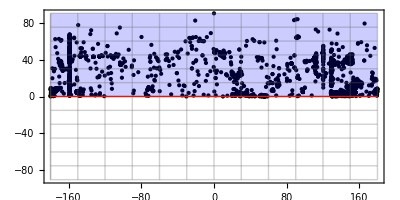

```mathematica
GeoGraphics[{Point[GeoPosition[Reverse[points,2]]],Blue,Polygon[GeoPosition[Reverse[{{-180,0},{180,0},{180,90},{-180,90}},{2}]]],Red,GeoPath["Equator"]},GeoGridLines->Automatic,Frame->True,GeoRange->All,GeoCenter->Automatic,GeoProjection->None,GeoBackground->None]
```

• A box is going to be specified as:

```mathematica
AstroRange->{{ra1,ra2},{dec1,dec2}}
```

#### Errors in the function

• The declination in the edges of the rectangle can not exceed the limits.

### Polygon

In Simbad the POLYGON function is: POLYGON(coord_sys, ra_vertice1, dec_vertice1, ra_vertice2, dec_vertice2, ra_vertice3, dec_vertice3 [, ...]).

This function connects each vertex with the next one following a geodesic.

This functions requires at least 3 vertices, but the three vertices could be in the same line (GeoPolygon can’t).

GeoPolygon supports things like GeoPolygon[GeoPosition[Reverse[{{0,85},{30,85},{180,89},{15,80}},{2}]]] (where segments of the polygon cross), but Simbad POLYGON can’t.

The polygon in the sky is going to be specified in AstroData as:

```mathematica
AstroRange->{{ra1,dec1},{ra2,dec2},{ra3,dec3},...}
```

#### Errors in the function

• The dec of the vertexes must be in the correct range to not getting unexpected positions.

• This function works well as long as it receives at least 3 different vertexes (although the vertexes can lie in the same line).

• The resulting polygon cannot have crossing segments (i.e. GeoPolygon[GeoPosition[Reverse[{{0,85},{30,85},{180,89},{15,80}},{2}]]]).

• A segment in the polygon can not be 180°.

```mathematica
query=URLEncode@"SELECT TOP 3000 oid, main_id, ra, dec
FROM basic WHERE CONTAINS(POINT('ICRS', ra, dec), POLYGON('ICRS', -720,0,-720,20,1981,20,1981,0)) = 1;";
result=Import[root~~query];
points=Rest@result[[All,{3,4}]];
```

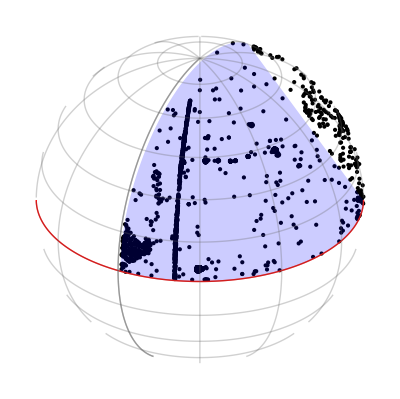

```mathematica
GeoGraphics[{Point[GeoPosition[Reverse[points,2]]],Blue,GeoPolygon[GeoPosition[Reverse[{{0,0},{0,20},{181,20},{181,0}},{2}]]](*,Blue,Polygon[GeoPosition[Reverse[{{0,85},{30,85},{180,89}},{2}]]]*),Red,GeoPath["Equator"]},GeoGridLines->Automatic,Frame->False,GeoCenter->Automatic,GeoProjection->{"Orthographic","Centering"->{30,-150}},GeoBackground->None,GeoRange->"World"]
```

### Drafts testing the sky functions of Simbad

#### Testing a vertex out of range in the declination in POLYGON function

```mathematica
query=URLEncode@"SELECT TOP 5000 oid, main_id, ra, dec
FROM basic WHERE CONTAINS(POINT('ICRS', ra, dec), POLYGON('ICRS', 0,0,90,0,0,181)) = 1;";
result=Import[root~~query];
points=Rest@result[[All,{3,4}]];
```

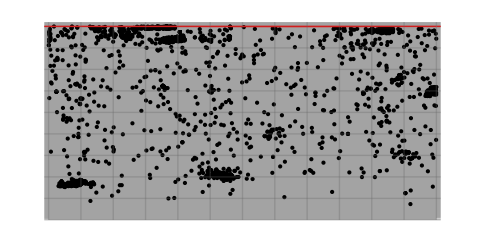

```mathematica
GeoGraphics[{Point[GeoPosition[Reverse[points,2]]],Black,GeoPolygon[GeoPosition[Reverse[{{0,0},{90,0},{180,-1}},{2}]]],Blue,Red,GeoPath["Equator"],Polygon[GeoPosition[Reverse[{{0,0},{90,0},{180,-1}},{2}]]]},GeoGridLines->Automatic,Frame->False,GeoProjection->None,GeoBackground->None,GeoRange->{{2,-90},{-2,182}}]
```

In conclusion, the vertex (0, 181) just is converted to the vertex (180, -1), which is logic but estrange.

#### This is what happen when one of the vertices in a polygon in not in the correct limits of declination.

```mathematica
query=URLEncode@"SELECT TOP 5000 oid, main_id, ra, dec
FROM basic WHERE CONTAINS(POINT('ICRS', ra, dec), POLYGON('ICRS', 0,85,30,85,0,91)) = 1;";
result=Import[root~~query];
points=Rest@result[[All,{3,4}]];
```

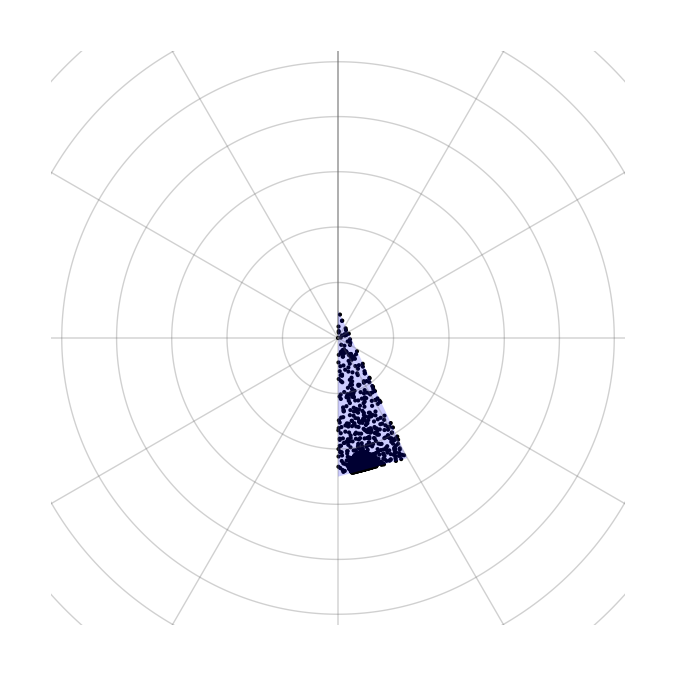

```mathematica
GeoGraphics[{Point[GeoPosition[Reverse[points,2]]],Blue,GeoPolygon[GeoPosition[Reverse[{{0,85},{30,85},{180,89}},{2}]]](*,Blue,Polygon[GeoPosition[Reverse[{{0,85},{30,85},{180,89}},{2}]]]*),Red,GeoPath["Equator"]},GeoGridLines->Automatic,Frame->False,GeoCenter->Automatic,GeoProjection->{"Orthographic","Centering"->{90,0}},GeoBackground->None,GeoRange->{{80., 90.}, {-180., 180.}}]
```

In this case the vertex (0, 91) is translated to (180,89).

#### • POLYGON join the vertices with geodesics.

```mathematica
query=URLEncode@"SELECT TOP 5000 oid, main_id, ra, dec
FROM basic WHERE CONTAINS(POINT('ICRS', ra, dec), POLYGON('ICRS', -80,-50,-80,-20,0,0,80,-20,80,-50)) = 1;";
result=Import[root~~query];
points=Rest@result[[All,{3,4}]];
```

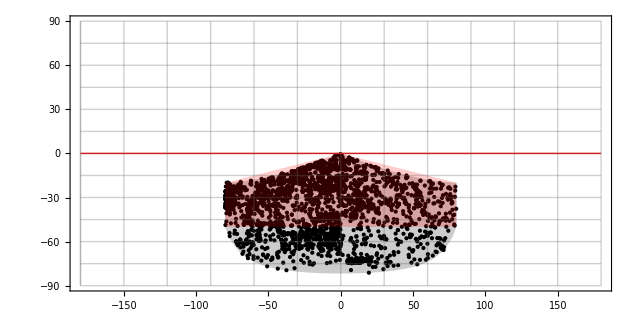

```mathematica
GeoGraphics[{Point[GeoPosition[Reverse[points,2]]],GeoPolygon[Reverse[{{-80,-50},{-80,-20},{0,0},{80,-20},{80,-50}},{2}]],Red,Polygon[GeoPosition[Reverse[{{-80,-50},{-80,-20},{0,0},{80,-20},{80,-50}},{2}]]],Red,GeoPath["Equator"]},GeoGridLines->Automatic,Frame->True,GeoRange->All,GeoCenter->Automatic,GeoProjection->"Equirectangular",GeoBackground->None]
```

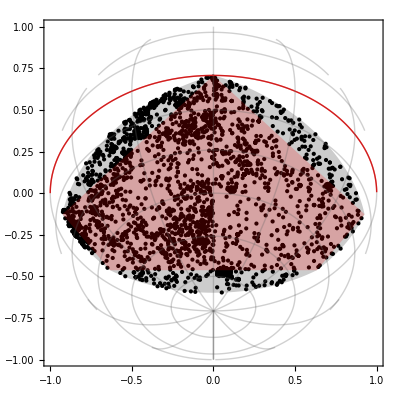

```mathematica
GeoGraphics[{Point[GeoPosition[Reverse[points,2]]],GeoPolygon[GeoPosition[Reverse[{{-80,-50},{-80,-20},{0,0},{80,-20},{80,-50}},{2}]]],Red,Polygon[GeoPosition[Reverse[{{-80,-50},{-80,-20},{0,0},{80,-20},{80,-50}},{2}]]],Red,GeoPath["Equator"]},GeoGridLines->Automatic,Frame->True,GeoRange->All,GeoCenter->Automatic,GeoProjection->{"Orthographic","Centering"->{-45,0}},GeoBackground->None]
```

#### • The box region in Simbad does not join the vertices with geodesics.

```mathematica
query=URLEncode@"SELECT TOP 5000 oid, main_id, ra, dec
FROM basic WHERE CONTAINS(POINT('ICRS', ra, dec), BOX('ICRS', 45, -45, 120, 10)) = 1;";
AbsoluteTiming[result=Import[root~~query];]
points=Rest@result[[All,{3,4}]];
```

{1.97169,Null}

```mathematica
Length[result]
```

5001

```mathematica
ByteCount[result]
```

873320

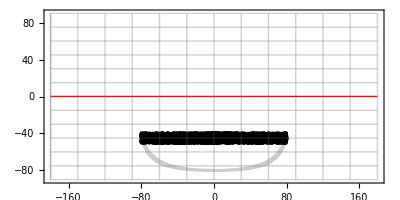

```mathematica
GeoGraphics[{Point[GeoPosition[Reverse[points,2]]],GeoPolygon[Reverse[{{-80,-40},{-80,-50},{80,-50},{80,-40}},{2}]],Polygon[{{-80,-40},{-80,-50},{80,-50},{80,-40}}],Red,GeoPath["Equator"]},GeoGridLines->Automatic,Frame->True,GeoRange->All,GeoCenter->Automatic,GeoProjection->"Equirectangular",GeoBackground->None]
```

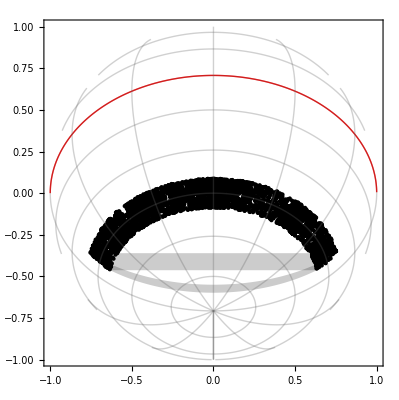

```mathematica
GeoGraphics[{Point[GeoPosition[Reverse[points,2]]],GeoPolygon[Reverse[{{-80,-40},{-80,-50},{80,-50},{80,-40}},{2}]],Polygon[GeoPosition[Reverse[{{-80,-40},{-80,-50},{80,-50},{80,-40}},{2}]]],Red,GeoPath["Equator"]},GeoGridLines->Automatic,Frame->True,GeoRange->All,GeoCenter->Automatic,GeoProjection->{"Orthographic","Centering"->{-45,0}},GeoBackground->None]
```

#### Notes about how Simbad deals with sky regions

• A position in the sky is specified in the range 360°>ra>0° and 90°>de>-90°. But any angle (positive or negative) can be given as argument. Simbad seems to work wrong estrange when the declination is not in the right limits. Right Ascension can be given as a negative angle, and mod 360 is calculated.

• There are 3 functions to specify a region in Simbad circle, box, and polygon.

• The circle is specified by a center and a radius. The radius must be in the range 90°>r>0°.

This function seems to work well when the angles are in the correct range:

```mathematica
query=URLEncode@"SELECT TOP 5000 oid, main_id, ra, dec
FROM basic WHERE CONTAINS(POINT('ICRS', ra, dec), CIRCLE('ICRS', 10, 10, 10)) = 1";
result=Import[rootHarvard~~query];
points=Rest@result[[All,{3,4}]];
```

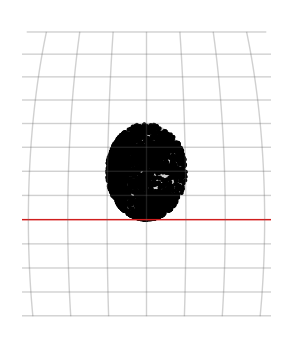

```mathematica
GeoGraphics[{Point[GeoPosition[Reverse[points,2]]],GeoDisk[{10,10},Quantity[10,"AngularDegrees"]],Red,GeoPath["Equator"]},GeoGridLines->Automatic,Frame->False,GeoRange->Quantity[30,"AngularDegrees"],GeoCenter->GeoPosition[{10,10}],GeoProjection->"Mollweide",GeoBackground->None]
```

But fails when the declination angle is not in the correct range:

```mathematica
query=URLEncode@"SELECT TOP 5000 oid, main_id, ra, dec
FROM basic WHERE CONTAINS(POINT('ICRS', ra, dec), CIRCLE('ICRS',180, 100, 10)) = 1";
result=Import[root~~query];
points=Rest@result[[All,{3,4}]];
```

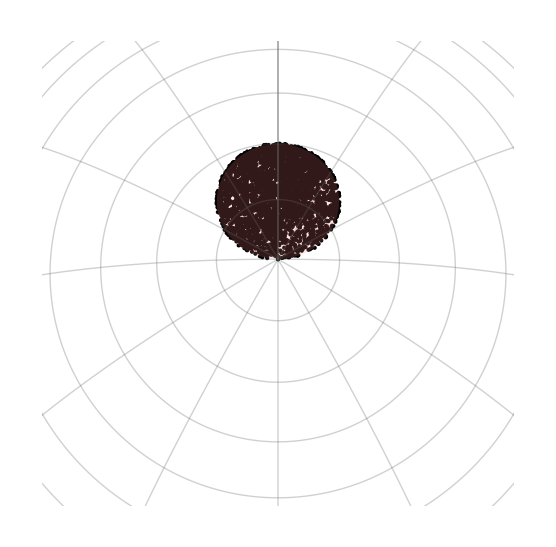

```mathematica
GeoGraphics[{Point[GeoPosition[Reverse[points,2]]],Pink,GeoDisk[{80,0},Quantity[10,"AngularDegrees"]],Red,GeoPath["Equator"]},GeoGridLines->Automatic,Frame->False,GeoRange->Quantity[30,"AngularDegrees"],GeoCenter->GeoPosition[{80,180}],GeoProjection->"Orthographic",GeoBackground->None]
```

• Box seems to work wrong when the center of the box is not in the proper range of the celestial sphere as the circle.

This is a good range:

```mathematica
query=URLEncode@"SELECT TOP 500 oid, main_id, ra, dec
FROM basic WHERE CONTAINS(POINT('ICRS', ra, dec), BOX('ICRS', 270, -45, 5, 5)) = 1;";
result=Import[root~~query];
points=Rest@result[[All,{3,4}]];
```

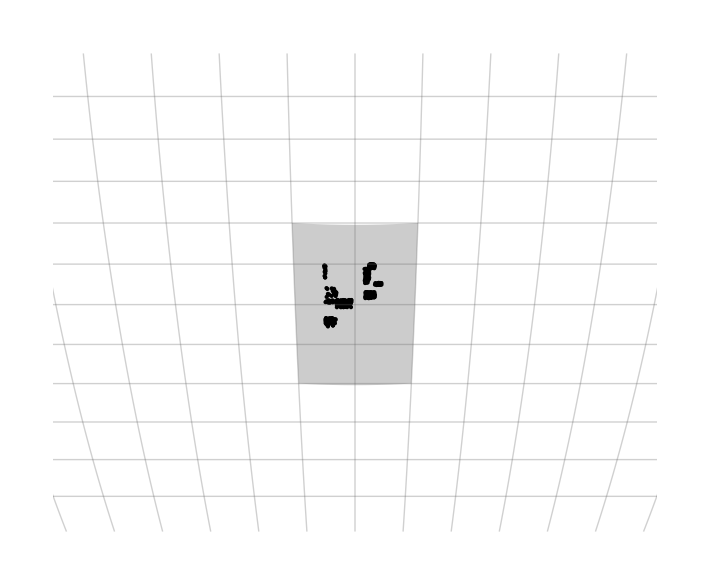

```mathematica
GeoGraphics[{Point[GeoPosition[Reverse[points,2]]],GeoPolygon[{{-50,275},{-50,265},{-40,265},{-40,275}}],Red,GeoPath["Equator"]},GeoGridLines->Automatic,Frame->False,GeoRange->Quantity[15,"AngularDegrees"],GeoCenter->GeoPosition[{-45,270}],GeoProjection->"Mollweide",GeoBackground->None]
```

This example is a bad range:

```mathematica
query=URLEncode@"SELECT TOP 5000 oid, main_id, ra, dec
FROM basic WHERE CONTAINS(POINT('ICRS', ra, dec), BOX('ICRS', 10, -100, 10, 10)) = 1;";
result=Import[root~~query];
points=Rest@result[[All,{3,4}]];
```

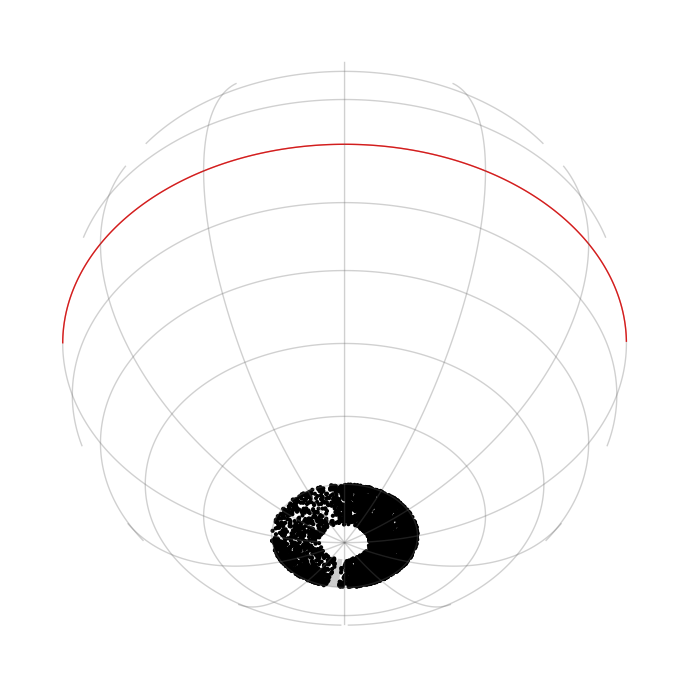

```mathematica
GeoGraphics[{Point[GeoPosition[Reverse[points,2]]],Polygon[GeoPosition[Reverse[{{180+5,-85},{180+5,-75},{180+15,-75},{180+15,-85}},{2}]]],Red,GeoPath["Equator"]},GeoGridLines->Automatic,Frame->False,GeoRange->"World",GeoCenter->GeoPosition[{-80,10}],GeoProjection->{"Orthographic","Centering"->{-45,0}},GeoBackground->None]
```

• Polygon

```mathematica
query=URLEncode@"SELECT TOP 5000 oid, main_id, ra, dec
FROM basic WHERE CONTAINS(POINT('ICRS', ra, dec), POLYGON('ICRS', 10,-50.6,70,0.2,20,30,-30,0,0,0)) = 1;";
result=Import[root~~query];
points=Rest@result[[All,{3,4}]];
```

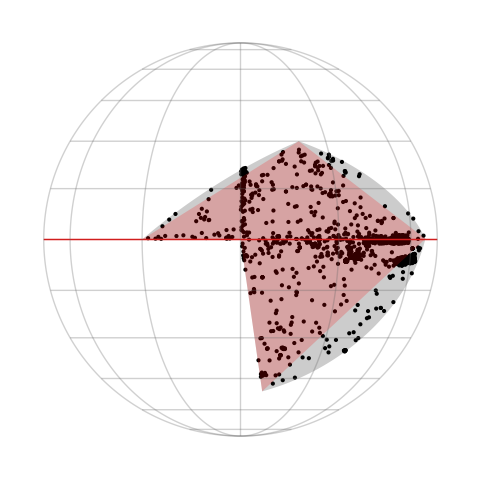

```mathematica
GeoGraphics[{Point[GeoPosition[Reverse[points,2]]],GeoPolygon[GeoPosition[Reverse[{{10,-50.6},{70,0.2},{20,30},{-30,0},{0,0}},{2}]]],Red,Polygon[GeoPosition[Reverse[{{10,-50.6},{70,0.2},{20,30},{-30,0},{0,0}},{2}]]],Red,GeoPath["Equator"]},GeoGridLines->Automatic,Frame->False,GeoRange->"World",GeoCenter->Automatic,GeoProjection->"Orthographic",GeoBackground->None]
```

• Because the sky functions of Simbad does not work properly out of the range, I am going to return a error message if the range in the sky is not respected.

# Information of the properties of AstroData

The following info is what I use to know what columns and tables I have to query from Simbad to construct a given Property.

```mathematica
infoProperties={<|"Property Name"->"Identifiers","Description"->"List of all the identifiers of an astronomical object","Head"->List,"Example"->{"Nenque","HD 6434","..."},"Units"->None,"Simbad Columns Called"->{"ids.ids"},"Comment"->"","Simbad Tables Involved"->{"ids"},"Simbad Columns Returned"->{"ids"}|>,
<|"Property Name"->"MainIdentifier","Description"->"Main identifier used by Simbad","Head"->String,"Example"->"HD 6434","Units"->None,"Simbad Columns Called"->{"basic.main_id"},"Comment"->"","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"main_id"}|>,
<|"Property Name"->"ObjectTypes","Description"->"List of the object types that the astronomical object is","Head"->List,"Example"->{"transient event","Radio-source","..."},"Units"->None,"Simbad Columns Called"->{"alltypes.otypes"},"Comment"->"","Simbad Tables Involved"->{"alltypes"},"Simbad Columns Returned"->{"otypes"}|>,<|"Property Name"->"MainObjectType","Description"->"Main object type","Head"->String,"Example"->"Star","Units"->None,"Simbad Columns Called"->{"basic.otype_txt"},"Comment"->"","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"otype_txt"}|>,<|"Property Name"->"RightAscensionWithUncertainty","Description"->"Right Ascension with uncertainty","Head"->Quantity[Around],"Example"->Quantity[(1.000.10), "AngularDegrees"],"Units"->Quantity[1, "AngularDegrees"],"Simbad Columns Called"->{"basic.ra","basic.dec","basic.coo_err_maj","basic.coo_err_min","basic.coo_err_angle"},"Comment"->"This must be transformed from the ellipse error of Simbad.\nOnly if the error is available the property will exist.","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"ra","dec","coo_err_maj","coo_err_min","coo_err_angle"}|>,<|"Property Name"->"RightAscension","Description"->"Right Ascension","Head"->Quantity,"Example"->Quantity[30, "AngularDegrees"],"Units"->Quantity[1, "AngularDegrees"],"Simbad Columns Called"->{"basic.ra"},"Comment"->"","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"ra"}|>,<|"Property Name"->"DeclinationWithUncertainty","Description"->"Declination with uncertainty","Head"->Quantity[Around],"Example"->Quantity[(1.000.10), "AngularDegrees"],"Units"->Quantity[1, "AngularDegrees"],"Simbad Columns Called"->{"basic.dec","basic.ra","basic.coo_err_maj","basic.coo_err_min","basic.coo_err_angle"},"Comment"->"This must be transformed from the ellipse error of Simbad.\nOnly if the error is available the property will exist.","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"dec","ra","coo_err_maj","coo_err_min","coo_err_angle"}|>,<|"Property Name"->"Declination","Description"->"Declination","Head"->Quantity,"Example"->Quantity[30, "AngularDegrees"],"Units"->Quantity[1, "AngularDegrees"],"Simbad Columns Called"->{"basic.dec"},"Comment"->"","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"dec"}|>,<|"Property Name"->"PositionErrorEllipse","Description"->"Error in position shown as error ellipse","Head"->VectorAround,"Example"->VectorAround[{1.0778195484261666,-0.5117817865411112},{{0.004098748158802123,0.01886916685785904},{0.01886916685785904,0.10778396789058062}}],"Units"->Quantity[1, "AngularDegrees"],"Simbad Columns Called"->{"basic.dec","basic.ra","basic.coo_err_maj","basic.coo_err_min","basic.coo_err_angle"},"Comment"->"This must be transformed from the ellipse error of Simbad.\nThis will exists only if there is error.\nI should check how to return the units.","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"dec","ra","coo_err_maj","coo_err_min","coo_err_angle"}|>,<|"Property Name"->"PositionWavelengthClass","Description"->"Wavelength class for the origin of the coordinates ","Head"->String,"Example"->"IR","Units"->None,"Simbad Columns Called"->{"basic.coo_wavelength"},"Comment"->"","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"coo_wavelength"}|>,<|"Property Name"->"PositionQuality","Description"->"Quality of the position.","Head"->String,"Example"->"A","Units"->None,"Simbad Columns Called"->{"basic.coo_qual"},"Comment"->"","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"coo_qual"}|>,<|"Property Name"->"PositionBibcode","Description"->"Bibcode of the position.","Head"->String,"Example"->"2015ApJS..219...12A","Units"->None,"Simbad Columns Called"->{"basic.coo_bibcode"},"Comment"->"","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"coo_bibcode"}|>,<|"Property Name"->"ProperMotionRightAscensionWithUncertainty","Description"->"Proper motion in right ascension with uncertainty.","Head"->Quantity[Around],"Example"->Quantity[(1.000.10), ("MilliarcSeconds")/("Years")],"Units"->Quantity[1, ("MilliarcSeconds")/("Years")],"Simbad Columns Called"->{"basic.pmra","basic.pm_err_maj","basic.pm_err_min","basic.pm_err_angle"},"Comment"->"This must be transformed from the ellipse error of Simbad.\nOnly if the error is available the property will exist.","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"pmra","pm_err_maj","pm_err_min","pm_err_angle"}|>,<|"Property Name"->"ProperMotionRightAscension","Description"->"Proper motion in right ascension.","Head"->Quantity,"Example"->Quantity[5, ("MilliarcSeconds")/("Years")],"Units"->Quantity[1, ("MilliarcSeconds")/("Years")],"Simbad Columns Called"->{"basic.pmra"},"Comment"->"","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"pmra"}|>,<|"Property Name"->"ProperMotionDeclinationWithUncertainty","Description"->"Proper motion in declination with uncertainty.","Head"->Quantity[Around],"Example"->Quantity[(1.000.10), ("MilliarcSeconds")/("Years")],"Units"->Quantity[1, ("MilliarcSeconds")/("Years")],"Simbad Columns Called"->{"basic.pmdec","basic.pm_err_maj","basic.pm_err_min","basic.pm_err_angle"},"Comment"->"This must be transformed from the ellipse error of Simbad.\nOnly if the error is available the property will exist.","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"pmdec","pm_err_maj","pm_err_min","pm_err_angle"}|>,<|"Property Name"->"ProperMotionDeclination","Description"->"Proper motion in declination.","Head"->Quantity,"Example"->Quantity[5, ("MilliarcSeconds")/("Years")],"Units"->Quantity[1, ("MilliarcSeconds")/("Years")],"Simbad Columns Called"->{"basic.pmdec"},"Comment"->"","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"pmdec"}|>,<|"Property Name"->"ProperMotionErrorEllipse","Description"->"Error in proper motion shown as error ellipse","Head"->VectorAround,"Example"->VectorAround[{1.0778195484261666,-0.5117817865411112},{{0.004098748158802123,0.01886916685785904},{0.01886916685785904,0.10778396789058062}}],"Units"->Quantity[1, degree per year],"Simbad Columns Called"->{"basic.pmra","basic.pmdec","basic.pm_err_maj","basic.pm_err_min","basic.pm_err_angle"},"Comment"->"This must be transformed from the ellipse error of Simbad.\nThis will exists only if there is error.\nI should check how to return the units.","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"pmra","pmdec","pm_err_maj","pm_err_min","pm_err_angle"}|>,<|"Property Name"->"ProperMotionQuality","Description"->"Quality of the proper motion.","Head"->String,"Example"->"A","Units"->None,"Simbad Columns Called"->{"basic.pm_qual"},"Comment"->"","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"pm_qual"}|>,<|"Property Name"->"ProperMotionBibcode","Description"->"Bibcode of the proper motion.","Head"->String,"Example"->"2015ApJS..219...12A","Units"->None,"Simbad Columns Called"->{"basic.pm_bibcode"},"Comment"->"","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"pm_bibcode"}|>,<|"Property Name"->"ParallaxWithUncertainty","Description"->"Parallax with uncertainty","Head"->Quantity[Around],"Example"->Quantity[(1.000.10), "MilliarcSeconds"],"Units"->Quantity[1, "MilliarcSeconds"],"Simbad Columns Called"->{"basic.plx_value","basic.plx_err"},"Comment"->"Only if the error is available the property exist.","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"plx_value","plx_err"}|>,<|"Property Name"->"Parallax","Description"->"Parallax","Head"->Quantity,"Example"->Quantity[10, "MilliarcSeconds"],"Units"->Quantity[1, "MilliarcSeconds"],"Simbad Columns Called"->{"basic.plx_value"},"Comment"->"","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"plx_value"}|>,<|"Property Name"->"ParallaxQuality","Description"->"Quality of the parallax.","Head"->String,"Example"->"A","Units"->None,"Simbad Columns Called"->{"basic.plx_qual"},"Comment"->"","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"plx_qual"}|>,<|"Property Name"->"ParallaxBibcode","Description"->"Bibcode of the parallax.","Head"->String,"Example"->"2015ApJS..219...12A","Units"->None,"Simbad Columns Called"->{"basic.plx_bibcode"},"Comment"->"","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"plx_bibcode"}|>,<|"Property Name"->"RedshiftWithUncertainty","Description"->"Redshift with uncertainty","Head"->Around,"Example"->1.000.10,"Units"->None,"Simbad Columns Called"->{"basic.rvz_type","basic.rvz_redshift","basic.rvz_err"},"Comment"->"Redshift of obejects in Simbad come from measurement or from computation from radial velocity. Computed redshifts are not good at large redshift because Simbad uses special relativistic formula of redshift, for example see the redsift of the object \"[ORN2011] 003.584125-30.483750\" the velocity in this case should be larger than c. I propese making my own computations of redshift or returning just the mesurement not the computation. One knows if the value is measurement or computation seeing the column basic.rvz_type","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"rvz_type","rvz_redshift","rvz_err"}|>,<|"Property Name"->"Redshift","Description"->"Redshift","Head"->Real,"Example"->1.,"Units"->None,"Simbad Columns Called"->{"basic.rvz_type","basic.rvz_redshift"},"Comment"->"Same comment as RedshiftWithUncertainty.","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"rvz_type","rvz_redshift"}|>,
<|"Property Name"->"RedshiftQuality","Description"->"Quality of the redshift.","Head"->String,"Example"->"A","Units"->None,"Simbad Columns Called"->{"basic.rvz_qual","basic.rvz_type"},"Comment"->"","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"rvz_qual","rvz_type"}|>,<|"Property Name"->"RedshiftBibcode","Description"->"Bibcode of the redshift.","Head"->String,"Example"->"2015ApJS..219...12A","Units"->None,"Simbad Columns Called"->{"basic.rvz_bibcode","basic.rvz_type"},"Comment"->"","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"rvz_bibcode","rvz_type"}|>,<|"Property Name"->"RadialVelocityWithUncertainty","Description"->"Radial velocity with uncertainty.","Head"->Quantity[Around],"Example"->Quantity[(1.000.10), ("Kilometers")/("Seconds")],"Units"->Quantity[1, ("Kilometers")/("Seconds")],"Simbad Columns Called"->{"basic.rvz_type","basic.rvz_radvel","basic.rvz_err"},"Comment"->"Radial velocity has the same problem as redshift.","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"rvz_type","rvz_radvel","rvz_err"}|>,<|"Property Name"->"RadialVelocity","Description"->"Radial velocity.","Head"->Quantity,"Example"->Quantity[10, ("Kilometers")/("Seconds")],"Units"->Quantity[1, ("Kilometers")/("Seconds")],"Simbad Columns Called"->{"basic.rvz_type","basic.rvz_radvel"},"Comment"->"Radial velocity has the same problem as redshift.","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"rvz_type","rvz_radvel"}|>,<|"Property Name"->"RadialVelocityQuality","Description"->"Quality of the radial velocity.","Head"->String,"Example"->"A","Units"->None,"Simbad Columns Called"->{"basic.rvz_qual","basic.rvz_type"},"Comment"->"","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"rvz_qual","rvz_type"}|>,<|"Property Name"->"RadialVelocityBibcode","Description"->"Bibcode of the radial velocity.","Head"->String,"Example"->"2015ApJS..219...12A","Units"->None,"Simbad Columns Called"->{"basic.rvz_bibcode","basic.rvz_type"},"Comment"->"","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"rvz_bibcode","rvz_type"}|>,
<|"Property Name"->"LocalStandardOfRestVelocity","Description"->"Velocity in Local Standard of Rest reference frame","Head"->Real,"Example"->221.,"Units"->Undefined,"Simbad Columns Called"->{"basic.vlsr"},"Comment"->"Ask Jeff. I am not sure if include this property because the units are not specified by Simbad.","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"vlsr"}|>,<|"Property Name"->"SpectralClass","Description"->"Code of spectral classification","Head"->String,"Example"->"G2V","Units"->None,"Simbad Columns Called"->{"basic.sp_type"},"Comment"->"I could add properties that extract info from the code.","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"sp_type"}|>,<|"Property Name"->"SpectralClassQuality","Description"->"Quality of the spectral class.","Head"->String,"Example"->"A","Units"->None,"Simbad Columns Called"->{"basic.sp_qual"},"Comment"->"","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"sp_qual"}|>,<|"Property Name"->"SpectralClassBibcode","Description"->"Bibcode of the spectral class.","Head"->String,"Example"->"2015ApJS..219...12A","Units"->None,"Simbad Columns Called"->{"basic.sp_bibcode"},"Comment"->"","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"sp_bibcode"}|>,<|"Property Name"->"MorphologicalClass","Description"->"Code of morphological classification","Head"->String,"Example"->"(R')SB(s)0/a","Units"->None,"Simbad Columns Called"->{"basic.morph_type"},"Comment"->"I could add properties that extract info from the code.","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"morph_type"}|>,<|"Property Name"->"MorphologicalClassQuality","Description"->"Quality of the morphological class.","Head"->String,"Example"->"A","Units"->None,"Simbad Columns Called"->{"basic.morph_qual"},"Comment"->"","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"morph_qual"}|>,<|"Property Name"->"MorphologicalClassBibcode","Description"->"Bibcode of the morphological class.","Head"->String,"Example"->"2015ApJS..219...12A","Units"->None,"Simbad Columns Called"->{"basic.morph_bibcode"},"Comment"->"","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"morph_bibcode"}|>,<|"Property Name"->"GalaxyMajorAxis","Description"->"Angular size major axis","Head"->Quantity,"Example"->Quantity[0.5, "ArcMinutes"],"Units"->Quantity[1, "ArcMinutes"],"Simbad Columns Called"->{"basic.galdim_majaxis"},"Comment"->"","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"galdim_majaxis"}|>,<|"Property Name"->"GalaxyMinorAxis","Description"->"Angular size minor axis","Head"->Quantity,"Example"->Quantity[0.5, "ArcMinutes"],"Units"->Quantity[1, "ArcMinutes"],"Simbad Columns Called"->{"basic.galdim_minaxis"},"Comment"->"","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"galdim_minaxis"}|>,<|"Property Name"->"GalaxyPositionAngle","Description"->"Galaxy ellipse angle","Head"->Quantity,"Example"->Quantity[45, "AngularDegrees"],"Units"->Quantity[1, "AngularDegrees"],"Simbad Columns Called"->{"basic.galdim_angle"},"Comment"->"","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"galdim_angle"}|>,<|"Property Name"->"GalaxySizeQuality","Description"->"Quality of the galaxy size.","Head"->String,"Example"->"A","Units"->None,"Simbad Columns Called"->{"basic.galdim_qual"},"Comment"->"","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"galdim_qual"}|>,<|"Property Name"->"GalaxySizeBibcode","Description"->"Bibcode of the galaxy size.","Head"->String,"Example"->"2015ApJS..219...12A","Units"->None,"Simbad Columns Called"->{"basic.galdim_bibcode"},"Comment"->"","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"galdim_bibcode"}|>,<|"Property Name"->"VMagnitudeWithUncertainty","Description"->"Magnitude in the filter V.","Head"->Around,"Example"->2.250.25,"Units"->None,"Simbad Columns Called"->{"v.flux as \"V\"","v.flux_err as \"V_err\""},"Comment"->"There is going to be similar properties to the 14 filters.","Simbad Tables Involved"->{"flux v"},"Simbad Columns Returned"->{"V","V_err"}|>,<|"Property Name"->"VMagnitude","Description"->"Magnitude in the filter V.","Head"->Real,"Example"->2.25,"Units"->None,"Simbad Columns Called"->{"v.flux as \"V\""},"Comment"->"There is going to be similar properties to the 14 filters.","Simbad Tables Involved"->{"flux v"},"Simbad Columns Returned"->{"V"}|>,<|"Property Name"->"VMagnitudeQuality","Description"->"Quality of the magnitude in the V filter.","Head"->String,"Example"->"A","Units"->None,"Simbad Columns Called"->{"v.qual as \"V_qual\""},"Comment"->"","Simbad Tables Involved"->{"flux v"},"Simbad Columns Returned"->{"V_qual"}|>,<|"Property Name"->"VMagnitudeBibcode","Description"->"Bibcode of the magnitude in the V filter.","Head"->String,"Example"->"2015ApJS..219...12A","Units"->None,"Simbad Columns Called"->{"v.bibcode as \"V_bib\""},"Comment"->"","Simbad Tables Involved"->{"flux v"},"Simbad Columns Returned"->{"V_bib"}|>,(* --U-- *)
<|"Property Name"->"UMagnitudeWithUncertainty","Description"->"Magnitude in the filter U.","Head"->Around,"Example"->2.250.25,"Units"->None,"Simbad Columns Called"->{"u.flux as \"U\"","u.flux_err as \"U_err\""},"Comment"->"There is going to be similar properties to the 14 filters.","Simbad Tables Involved"->{"flux u"},"Simbad Columns Returned"->{"U","U_err"}|>,<|"Property Name"->"UMagnitude","Description"->"Magnitude in the filter U.","Head"->Real,"Example"->2.25,"Units"->None,"Simbad Columns Called"->{"u.flux as \"U\""},"Comment"->"There is going to be similar properties to the 14 filters.","Simbad Tables Involved"->{"flux u"},"Simbad Columns Returned"->{"U"}|>,<|"Property Name"->"UMagnitudeQuality","Description"->"Quality of the magnitude in the U filter.","Head"->String,"Example"->"A","Units"->None,"Simbad Columns Called"->{"u.qual as \"U_qual\""},"Comment"->"","Simbad Tables Involved"->{"flux u"},"Simbad Columns Returned"->{"U_qual"}|>,<|"Property Name"->"UMagnitudeBibcode","Description"->"Bibcode of the magnitude in the U filter.","Head"->String,"Example"->"2015ApJS..219...12A","Units"->None,"Simbad Columns Called"->{"u.bibcode as \"U_bib\""},"Comment"->"","Simbad Tables Involved"->{"flux u"},"Simbad Columns Returned"->{"U_bib"}|>,
(* --B-- *)
<|"Property Name"->"BMagnitudeWithUncertainty","Description"->"Magnitude in the filter B.","Head"->Around,"Example"->2.250.25,"Units"->None,"Simbad Columns Called"->{"b.flux as \"B\"","b.flux_err as \"B_err\""},"Comment"->"There is going to be similar properties to the 14 filters.","Simbad Tables Involved"->{"flux b"},"Simbad Columns Returned"->{"B","B_err"}|>,<|"Property Name"->"BMagnitude","Description"->"Magnitude in the filter B.","Head"->Real,"Example"->2.25,"Units"->None,"Simbad Columns Called"->{"b.flux as \"B\""},"Comment"->"There is going to be similar properties to the 14 filters.","Simbad Tables Involved"->{"flux b"},"Simbad Columns Returned"->{"B"}|>,<|"Property Name"->"BMagnitudeQuality","Description"->"Quality of the magnitude in the B filter.","Head"->String,"Example"->"A","Units"->None,"Simbad Columns Called"->{"b.qual as \"B_qual\""},"Comment"->"","Simbad Tables Involved"->{"flux b"},"Simbad Columns Returned"->{"B_qual"}|>,<|"Property Name"->"BMagnitudeBibcode","Description"->"Bibcode of the magnitude in the B filter.","Head"->String,"Example"->"2015ApJS..219...12A","Units"->None,"Simbad Columns Called"->{"b.bibcode as \"B_bib\""},"Comment"->"","Simbad Tables Involved"->{"flux b"},"Simbad Columns Returned"->{"B_bib"}|>,
(* --R-- *)
<|"Property Name"->"RMagnitudeWithUncertainty","Description"->"Magnitude in the filter R.","Head"->Around,"Example"->2.250.25,"Units"->None,"Simbad Columns Called"->{"r.flux as \"R\"","r.flux_err as \"R_err\""},"Comment"->"There is going to be similar properties to the 14 filters.","Simbad Tables Involved"->{"flux r"},"Simbad Columns Returned"->{"R","R_err"}|>,<|"Property Name"->"RMagnitude","Description"->"Magnitude in the filter R.","Head"->Real,"Example"->2.25,"Units"->None,"Simbad Columns Called"->{"r.flux as \"R\""},"Comment"->"There is going to be similar properties to the 14 filters.","Simbad Tables Involved"->{"flux r"},"Simbad Columns Returned"->{"R"}|>,<|"Property Name"->"RMagnitudeQuality","Description"->"Quality of the magnitude in the R filter.","Head"->String,"Example"->"A","Units"->None,"Simbad Columns Called"->{"r.qual as \"R_qual\""},"Comment"->"","Simbad Tables Involved"->{"flux r"},"Simbad Columns Returned"->{"R_qual"}|>,<|"Property Name"->"RMagnitudeBibcode","Description"->"Bibcode of the magnitude in the R filter.","Head"->String,"Example"->"2015ApJS..219...12A","Units"->None,"Simbad Columns Called"->{"r.bibcode as \"R_bib\""},"Comment"->"","Simbad Tables Involved"->{"flux r"},"Simbad Columns Returned"->{"R_bib"}|>,
(* --I-- *)
<|"Property Name"->"IMagnitudeWithUncertainty","Description"->"Magnitude in the filter I.","Head"->Around,"Example"->2.250.25,"Units"->None,"Simbad Columns Called"->{"i.flux as \"I\"","i.flux_err as \"I_err\""},"Comment"->"There is going to be similar properties to the 14 filters.","Simbad Tables Involved"->{"flux i"},"Simbad Columns Returned"->{"I","I_err"}|>,<|"Property Name"->"IMagnitude","Description"->"Magnitude in the filter I.","Head"->Real,"Example"->2.25,"Units"->None,"Simbad Columns Called"->{"i.flux as \"I\""},"Comment"->"There is going to be similar properties to the 14 filters.","Simbad Tables Involved"->{"flux i"},"Simbad Columns Returned"->{"I"}|>,<|"Property Name"->"IMagnitudeQuality","Description"->"Quality of the magnitude in the I filter.","Head"->String,"Example"->"A","Units"->None,"Simbad Columns Called"->{"i.qual as \"I_qual\""},"Comment"->"","Simbad Tables Involved"->{"flux i"},"Simbad Columns Returned"->{"I_qual"}|>,<|"Property Name"->"IMagnitudeBibcode","Description"->"Bibcode of the magnitude in the I filter.","Head"->String,"Example"->"2015ApJS..219...12A","Units"->None,"Simbad Columns Called"->{"i.bibcode as \"I_bib\""},"Comment"->"","Simbad Tables Involved"->{"flux i"},"Simbad Columns Returned"->{"I_bib"}|>,
(* --J--*)
<|"Property Name"->"JMagnitudeWithUncertainty","Description"->"Magnitude in the filter J.","Head"->Around,"Example"->2.250.25,"Units"->None,"Simbad Columns Called"->{"j.flux as \"J\"","j.flux_err as \"J_err\""},"Comment"->"There is going to be similar properties to the 14 filters.","Simbad Tables Involved"->{"flux j"},"Simbad Columns Returned"->{"J","J_err"}|>,<|"Property Name"->"JMagnitude","Description"->"Magnitude in the filter J.","Head"->Real,"Example"->2.25,"Units"->None,"Simbad Columns Called"->{"j.flux as \"J\""},"Comment"->"There is going to be similar properties to the 14 filters.","Simbad Tables Involved"->{"flux j"},"Simbad Columns Returned"->{"J"}|>,<|"Property Name"->"JMagnitudeQuality","Description"->"Quality of the magnitude in the J filter.","Head"->String,"Example"->"A","Units"->None,"Simbad Columns Called"->{"j.qual as \"J_qual\""},"Comment"->"","Simbad Tables Involved"->{"flux j"},"Simbad Columns Returned"->{"J_qual"}|>,<|"Property Name"->"JMagnitudeBibcode","Description"->"Bibcode of the magnitude in the J filter.","Head"->String,"Example"->"2015ApJS..219...12A","Units"->None,"Simbad Columns Called"->{"j.bibcode as \"J_bib\""},"Comment"->"","Simbad Tables Involved"->{"flux j"},"Simbad Columns Returned"->{"J_bib"}|>,
(* --H-- *)
<|"Property Name"->"HMagnitudeWithUncertainty","Description"->"Magnitude in the filter H.","Head"->Around,"Example"->2.250.25,"Units"->None,"Simbad Columns Called"->{"h.flux as \"H\"","h.flux_err as \"H_err\""},"Comment"->"There is going to be similar properties to the 14 filters.","Simbad Tables Involved"->{"flux h"},"Simbad Columns Returned"->{"H","H_err"}|>,<|"Property Name"->"HMagnitude","Description"->"Magnitude in the filter H.","Head"->Real,"Example"->2.25,"Units"->None,"Simbad Columns Called"->{"h.flux as \"H\""},"Comment"->"There is going to be similar properties to the 14 filters.","Simbad Tables Involved"->{"flux h"},"Simbad Columns Returned"->{"H"}|>,<|"Property Name"->"HMagnitudeQuality","Description"->"Quality of the magnitude in the H filter.","Head"->String,"Example"->"A","Units"->None,"Simbad Columns Called"->{"h.qual as \"H_qual\""},"Comment"->"","Simbad Tables Involved"->{"flux h"},"Simbad Columns Returned"->{"H_qual"}|>,<|"Property Name"->"HMagnitudeBibcode","Description"->"Bibcode of the magnitude in the H filter.","Head"->String,"Example"->"2015ApJS..219...12A","Units"->None,"Simbad Columns Called"->{"h.bibcode as \"H_bib\""},"Comment"->"","Simbad Tables Involved"->{"flux h"},"Simbad Columns Returned"->{"H_bib"}|>,
(* --K-- *)
<|"Property Name"->"KMagnitudeWithUncertainty","Description"->"Magnitude in the filter K.","Head"->Around,"Example"->2.250.25,"Units"->None,"Simbad Columns Called"->{"k.flux as \"K\"","k.flux_err as \"K_err\""},"Comment"->"There is going to be similar properties to the 14 filters.","Simbad Tables Involved"->{"flux k"},"Simbad Columns Returned"->{"K","K_err"}|>,<|"Property Name"->"KMagnitude","Description"->"Magnitude in the filter K.","Head"->Real,"Example"->2.25,"Units"->None,"Simbad Columns Called"->{"k.flux as \"K\""},"Comment"->"There is going to be similar properties to the 14 filters.","Simbad Tables Involved"->{"flux k"},"Simbad Columns Returned"->{"K"}|>,<|"Property Name"->"KMagnitudeQuality","Description"->"Quality of the magnitude in the K filter.","Head"->String,"Example"->"A","Units"->None,"Simbad Columns Called"->{"k.qual as \"K_qual\""},"Comment"->"","Simbad Tables Involved"->{"flux k"},"Simbad Columns Returned"->{"K_qual"}|>,<|"Property Name"->"KMagnitudeBibcode","Description"->"Bibcode of the magnitude in the K filter.","Head"->String,"Example"->"2015ApJS..219...12A","Units"->None,"Simbad Columns Called"->{"k.bibcode as \"K_bib\""},"Comment"->"","Simbad Tables Involved"->{"flux k"},"Simbad Columns Returned"->{"K_bib"}|>,
(* --G-- *)
<|"Property Name"->"GMagnitudeWithUncertainty","Description"->"Magnitude in the filter G.","Head"->Around,"Example"->2.250.25,"Units"->None,"Simbad Columns Called"->{"g.flux as \"G\"","g.flux_err as \"G_err\""},"Comment"->"There is going to be similar properties to the 14 filters.","Simbad Tables Involved"->{"flux g"},"Simbad Columns Returned"->{"G","G_err"}|>,<|"Property Name"->"GMagnitude","Description"->"Magnitude in the filter G.","Head"->Real,"Example"->2.25,"Units"->None,"Simbad Columns Called"->{"g.flux as \"G\""},"Comment"->"There is going to be similar properties to the 14 filters.","Simbad Tables Involved"->{"flux g"},"Simbad Columns Returned"->{"G"}|>,<|"Property Name"->"GMagnitudeQuality","Description"->"Quality of the magnitude in the G filter.","Head"->String,"Example"->"A","Units"->None,"Simbad Columns Called"->{"g.qual as \"G_qual\""},"Comment"->"","Simbad Tables Involved"->{"flux g"},"Simbad Columns Returned"->{"G_qual"}|>,<|"Property Name"->"GMagnitudeBibcode","Description"->"Bibcode of the magnitude in the G filter.","Head"->String,"Example"->"2015ApJS..219...12A","Units"->None,"Simbad Columns Called"->{"g.bibcode as \"G_bib\""},"Comment"->"","Simbad Tables Involved"->{"flux g"},"Simbad Columns Returned"->{"G_bib"}|>,
(* --u-- *)
<|"Property Name"->"SDSSUMagnitudeWithUncertainty","Description"->"Magnitude in the filter u.","Head"->Around,"Example"->2.250.25,"Units"->None,"Simbad Columns Called"->{"sdssu.flux as u","sdssu.flux_err as u_err"},"Comment"->"There is going to be similar properties to the 14 filters.","Simbad Tables Involved"->{"flux sdssu"},"Simbad Columns Returned"->{"u","u_err"}|>,<|"Property Name"->"SDSSUMagnitude","Description"->"Magnitude in the filter u.","Head"->Real,"Example"->2.25,"Units"->None,"Simbad Columns Called"->{"sdssu.flux as u"},"Comment"->"There is going to be similar properties to the 14 filters.","Simbad Tables Involved"->{"flux sdssu"},"Simbad Columns Returned"->{"u"}|>,<|"Property Name"->"SDSSUMagnitudeQuality","Description"->"Quality of the magnitude in the u filter.","Head"->String,"Example"->"A","Units"->None,"Simbad Columns Called"->{"sdssu.qual as u_qual"},"Comment"->"","Simbad Tables Involved"->{"flux sdssu"},"Simbad Columns Returned"->{"u_qual"}|>,<|"Property Name"->"SDSSUMagnitudeBibcode","Description"->"Bibcode of the magnitude in the u filter.","Head"->String,"Example"->"2015ApJS..219...12A","Units"->None,"Simbad Columns Called"->{"sdssu.bibcode as u_bib"},"Comment"->"","Simbad Tables Involved"->{"flux sdssu"},"Simbad Columns Returned"->{"u_bib"}|>,
(* --g-- *)
<|"Property Name"->"SDSSGMagnitudeWithUncertainty","Description"->"Magnitude in the filter g.","Head"->Around,"Example"->2.250.25,"Units"->None,"Simbad Columns Called"->{"sdssg.flux as g","sdssg.flux_err as g_err"},"Comment"->"There is going to be similar properties to the 14 filters.","Simbad Tables Involved"->{"flux sdssg"},"Simbad Columns Returned"->{"g","g_err"}|>,<|"Property Name"->"SDSSGMagnitude","Description"->"Magnitude in the filter g.","Head"->Real,"Example"->2.25,"Units"->None,"Simbad Columns Called"->{"sdssg.flux as g"},"Comment"->"There is going to be similar properties to the 14 filters.","Simbad Tables Involved"->{"flux sdssg"},"Simbad Columns Returned"->{"g"}|>,<|"Property Name"->"SDSSGMagnitudeQuality","Description"->"Quality of the magnitude in the g filter.","Head"->String,"Example"->"A","Units"->None,"Simbad Columns Called"->{"sdssg.qual as g_qual"},"Comment"->"","Simbad Tables Involved"->{"flux sdssg"},"Simbad Columns Returned"->{"g_qual"}|>,<|"Property Name"->"SDSSGMagnitudeBibcode","Description"->"Bibcode of the magnitude in the g filter.","Head"->String,"Example"->"2015ApJS..219...12A","Units"->None,"Simbad Columns Called"->{"sdssg.bibcode as g_bib"},"Comment"->"","Simbad Tables Involved"->{"flux sdssg"},"Simbad Columns Returned"->{"g_bib"}|>,
(* --r-- *)
<|"Property Name"->"SDSSRMagnitudeWithUncertainty","Description"->"Magnitude in the filter r.","Head"->Around,"Example"->2.250.25,"Units"->None,"Simbad Columns Called"->{"sdssr.flux as r","sdssr.flux_err as r_err"},"Comment"->"There is going to be similar properties to the 14 filters.","Simbad Tables Involved"->{"flux sdssr"},"Simbad Columns Returned"->{"r","r_err"}|>,<|"Property Name"->"SDSSRMagnitude","Description"->"Magnitude in the filter r.","Head"->Real,"Example"->2.25,"Units"->None,"Simbad Columns Called"->{"sdssr.flux as r"},"Comment"->"There is going to be similar properties to the 14 filters.","Simbad Tables Involved"->{"flux sdssr"},"Simbad Columns Returned"->{"r"}|>,<|"Property Name"->"SDSSRMagnitudeQuality","Description"->"Quality of the magnitude in the r filter.","Head"->String,"Example"->"A","Units"->None,"Simbad Columns Called"->{"sdssr.qual as r_qual"},"Comment"->"","Simbad Tables Involved"->{"flux sdssr"},"Simbad Columns Returned"->{"r_qual"}|>,<|"Property Name"->"SDSSRMagnitudeBibcode","Description"->"Bibcode of the magnitude in the r filter.","Head"->String,"Example"->"2015ApJS..219...12A","Units"->None,"Simbad Columns Called"->{"sdssr.bibcode as r_bib"},"Comment"->"","Simbad Tables Involved"->{"flux sdssr"},"Simbad Columns Returned"->{"r_bib"}|>,
(* --i-- *)
<|"Property Name"->"SDSSIMagnitudeWithUncertainty","Description"->"Magnitude in the filter i.","Head"->Around,"Example"->2.250.25,"Units"->None,"Simbad Columns Called"->{"sdssi.flux as i","sdssi.flux_err as i_err"},"Comment"->"There is going to be similar properties to the 14 filters.","Simbad Tables Involved"->{"flux sdssi"},"Simbad Columns Returned"->{"i","i_err"}|>,<|"Property Name"->"SDSSIMagnitude","Description"->"Magnitude in the filter i.","Head"->Real,"Example"->2.25,"Units"->None,"Simbad Columns Called"->{"sdssi.flux as i"},"Comment"->"There is going to be similar properties to the 14 filters.","Simbad Tables Involved"->{"flux sdssi"},"Simbad Columns Returned"->{"i"}|>,<|"Property Name"->"SDSSIMagnitudeQuality","Description"->"Quality of the magnitude in the i filter.","Head"->String,"Example"->"A","Units"->None,"Simbad Columns Called"->{"sdssi.qual as i_qual"},"Comment"->"","Simbad Tables Involved"->{"flux sdssi"},"Simbad Columns Returned"->{"i_qual"}|>,<|"Property Name"->"SDSSIMagnitudeBibcode","Description"->"Bibcode of the magnitude in the i filter.","Head"->String,"Example"->"2015ApJS..219...12A","Units"->None,"Simbad Columns Called"->{"sdssi.bibcode as i_bib"},"Comment"->"","Simbad Tables Involved"->{"flux sdssi"},"Simbad Columns Returned"->{"i_bib"}|>,
(* --z-- *)
<|"Property Name"->"SDSSZMagnitudeWithUncertainty","Description"->"Magnitude in the filter z.","Head"->Around,"Example"->2.250.25,"Units"->None,"Simbad Columns Called"->{"sdssz.flux as z","sdssz.flux_err as z_err"},"Comment"->"There is going to be similar properties to the 14 filters.","Simbad Tables Involved"->{"flux sdssz"},"Simbad Columns Returned"->{"z","z_err"}|>,<|"Property Name"->"SDSSZMagnitude","Description"->"Magnitude in the filter z.","Head"->Real,"Example"->2.25,"Units"->None,"Simbad Columns Called"->{"sdssz.flux as z"},"Comment"->"There is going to be similar properties to the 14 filters.","Simbad Tables Involved"->{"flux sdssz"},"Simbad Columns Returned"->{"z"}|>,<|"Property Name"->"SDSSZMagnitudeQuality","Description"->"Quality of the magnitude in the z filter.","Head"->String,"Example"->"A","Units"->None,"Simbad Columns Called"->{"sdssz.qual as z_qual"},"Comment"->"","Simbad Tables Involved"->{"flux sdssz"},"Simbad Columns Returned"->{"z_qual"}|>,<|"Property Name"->"SDSSZMagnitudeBibcode","Description"->"Bibcode of the magnitude in the z filter.","Head"->String,"Example"->"2015ApJS..219...12A","Units"->None,"Simbad Columns Called"->{"sdssz.bibcode as z_bib"},"Comment"->"","Simbad Tables Involved"->{"flux sdssz"},"Simbad Columns Returned"->{"z_bib"}|>,
<|"Property Name"->"Distance","Description"->"Distance to the object.","Head"->Quantity[Around],"Example"->Quantity[(42.410.080.08), "Parsecs"],"Units"->Quantity[1, "Parsecs"],"Simbad Columns Called"->{"mesdistance.dist","mesdistance.unit as dist_unit","mesdistance.plus_err","mesdistance.minus_err"},"Comment"->"I suppose that this is the distance from Earth, but I did not find it explicitly. The unit of the distance varies between pc, kpc, and Mpc.","Simbad Tables Involved"->{"mesdistance"},"Simbad Columns Returned"->{"dist","dist_unit","plus_err","minus_err"}|>,<|"Property Name"->"Diameter","Description"->"Diameter of the object.","Head"->Quantity[Around],"Example"->Quantity[8.100.2910^5, "Kilometers"],"Units"->Quantity[1, "Kilometers"]||Quantity[1, "MilliarcSeconds"],"Simbad Columns Called"->{"mesdiameter.diameter","mesdiameter.error","mesdiameter.unit"},"Comment"->"Simbad report the diameter of an object in km or mas, which is not a direct conversion.","Simbad Tables Involved"->{"mesdiameter"},"Simbad Columns Returned"->{"diameter","error","unit"}|>,<|"Property Name"->"EffectiveTemperature","Description"->"Effective Temperature.","Head"->Quantity,"Example"->Quantity[10000, "Kelvins"],"Units"->Quantity[1, "Kelvins"],"Simbad Columns Called"->{"mesFe_h.teff"},"Comment"->"","Simbad Tables Involved"->{"mesFe_h"},"Simbad Columns Returned"->{"teff"}|>,<|"Property Name"->"SurfaceGravity","Description"->"Surface gravity.","Head"->Quantity,"Example"->Quantity[9.8, ("Meters")/("Seconds")^2],"Units"->Quantity[1, ("Meters")/("Seconds")^2],"Simbad Columns Called"->{"mesFe_h.log_g"},"Comment"->"","Simbad Tables Involved"->{"mesFe_h"},"Simbad Columns Returned"->{"log_g"}|>,<|"Property Name"->"Metalicity","Description"->"Metallicity index relative to the Sun.","Head"->Real,"Example"->-0.53,"Units"->None,"Simbad Columns Called"->{"mesFe_h.fe_h","mesFe_h.compstar"},"Comment"->"Sometimes the metalicity given by Simbad is not relative to the Sun. In this case I am going to return nothing.","Simbad Tables Involved"->{"mesFe_h"},"Simbad Columns Returned"->{"fe_h","compstar"}|>,<|"Property Name"->"ProjectedRotationalVelocity","Description"->"Projected rotational velocity vsini.","Head"->Quantity[Around],"Example"->Quantity[(413.20.), ("Kilometers")/("Seconds")],"Units"->Quantity[1, ("Kilometers")/("Seconds")],"Simbad Columns Called"->{"mesrot.vsini","mesrot.vsini_err"},"Comment"->"","Simbad Tables Involved"->{"mesrot"},"Simbad Columns Returned"->{"vsini","vsini_err"}|>,<|"Property Name"->"VariablePeriod","Description"->"Period of variability","Head"->Quantity,"Example"->Quantity[0.5, "Days"],"Units"->Quantity[1, "Days"],"Simbad Columns Called"->{"mesvar.period"},"Comment"->"Maybe consider uncertainty flag of this field.","Simbad Tables Involved"->{"mesvar"},"Simbad Columns Returned"->{"period"}|>,<|"Property Name"->"VariableStarType","Description"->"Type of variability","Head"->String,"Example"->"α2 CVn","Units"->None,"Simbad Columns Called"->{"mesvar.vartyp"},"Comment"->"To transform simbad codes to more usual types see http://simbad.u-strasbg.fr/guide/chG.htx#v.","Simbad Tables Involved"->{"mesvar"},"Simbad Columns Returned"->{"vartyp"}|>,<|"Property Name"->"MaximumAbsoluteMagnitude","Description"->"Maximum of brightness","Head"->Real,"Example"->10.78,"Units"->None,"Simbad Columns Called"->{"mesvar.vmax"},"Comment"->"I am not sure what this data is, I should ask Jeff","Simbad Tables Involved"->{"mesvar"},"Simbad Columns Returned"->{"vmax"}|>,<|"Property Name"->"MinimunAbsoluteMagnitude","Description"->"Minimum of brightness","Head"->Real,"Example"->10.84,"Units"->None,"Simbad Columns Called"->{"mesvar.vmin"},"Comment"->"I am not sure what this data is, I should ask Jeff","Simbad Tables Involved"->{"mesvar"},"Simbad Columns Returned"->{"vmin"}|>,<|"Property Name"->"VariabilityEpoch","Description"->"Epoch of maximum or minimum","Head"->Real,"Example"->2.4569036621*^6,"Units"->JulianDate,"Simbad Columns Called"->{"mesvar.epoch"},"Comment"->"I am not sure what this data is, I should ask Jeff","Simbad Tables Involved"->{"mesvar"},"Simbad Columns Returned"->{"epoch"}|>};
```

Quantity::unkunit: Unable to interpret unit specification Around.

General::stop: Further output of Quantity::unkunit will be suppressed during this calculation.

Dataset of the above info, to visualize it easier:

```mathematica
propertiesInformation=Dataset[infoProperties]
```

```mathematica
LinguisticAssistant["AbsoluteMagnitude"]
```

4.69

```mathematica
LinguisticAssistant["ApparentMagnitude"]
```

7.71

```mathematica
AstroData["1",{"UMagnitude","BMagnitude"}]
```

ResourceFunction::usermessage: AstroData

Missing[NotAvailable]

## Information of the Simbad columns involved in my function

This info is mainly to know easily the units of the Simbad columns.

```mathematica
root="http://simbad.u-strasbg.fr/simbad/sim-tap/sync?request=doQuery&lang=adql&format=tsv&query=";
```

```mathematica
query=URLEncode["SELECT table_name, column_name, description, unit FROM tap_schema.columns WHERE table_name IN('basic', 'mesFe_h', 'mesRot', 'mesVar') AND column_name IN('ra','coo_err_maj', 'coo_err_min', 'coo_err_angle', 'dec', 'pmra', 'pmdec', 'pm_err_maj', 'pm_err_min', 'pm_err_angle', 'plx_value', 'plx_err', 'rvz_radvel', 'rvz_err', 'galdim_angle', 'galdim_majaxis', 'galdim_minaxis', 'teff', 'log_g', 'vsini', 'period')"];
query=Import[root~~query];
generalUnits=Dataset[AssociationThread[First[query]->#]&/@Rest[query]]
```

Units that are not directly in the metadata

```mathematica
query=URLEncode["SELECT table_name, column_name, description, unit FROM tap_schema.columns 
WHERE table_name IN('mesDistance', 'mesDiameter') AND column_name IN('unit')"];
query=Import[root~~query];
Dataset[AssociationThread[First[query]->#]&/@Rest[query]]
```

# The function

### Roots

```mathematica
rootFrance="http://simbad.u-strasbg.fr/simbad/sim-tap/sync?request=doQuery&lang=adql&format=tsv&query=";
rootUS="http://simbad.cfa.harvard.edu/simbad/sim-tap/sync?request=doQuery&lang=adql&format=tsv&query=";
```

### Options

```mathematica
Options[AstroData]={
"Mirror"->"France"
};
```

### Error Messages

```mathematica
AstroData::wrongprop:="Invalid property."
AstroData::queryfail:="The SIMBAD query failed."
AstroData::noinfofound:="No data found."
AstroData::wrongmaxitems:="MaxItems value must be an integer."
AstroData::wrongradius:="Wrong radius specification."
AstroData::bigradius:="The radius must be in the range 0°≤r≤90°."
AstroData::wrongcenter:="Wrong center specification."
AstroData::wrongdec:="Declination must be in the range -90°≤de≤90°."
AstroData::wrongbox:="Wrong rectangle specification."
AstroData::wrongpoly:="Wrong polygon specification."
AstroData::wrongpolysegment:="A segment of the polygon cannot be 180° length."
AstroData::wrongmirror:="Mirror not available."
```

### Functions that arrange the properties

This functions take the Simbad columns and arrange them into the AstroData properties.

#### Quantity properties

```mathematica
rightascensionCompose[asso_Association]:=(If[First[asso["ra"]]=="",Return[Rule["RightAscension",Missing["NotAvailable"]]]];
Rule["RightAscension",UnitConvert[Quantity[First@asso["ra"],"AngularDegrees"],
MixedUnit[{"HoursOfRightAscension","MinutesOfRightAscension","SecondsOfRightAscension"}]]]
)

declinationCompose[asso_Association]:=(If[First[asso["dec"]]=="",Return[Rule["Declination",Missing["NotAvailable"]]]];
Rule["Declination",UnitConvert[Quantity[First@asso["dec"],"AngularDegrees"],
MixedUnit[{"AngularDegrees","ArcMinutes","ArcSeconds"}]]]
)

propermotionrightascensionCompose[asso_Association]:=(If[First[asso["pmra"]]=="",
Return[Rule["ProperMotionRightAscension",Missing["NotAvailable"]]]];
Rule["ProperMotionRightAscension",Quantity[First@asso["pmra"],"MilliarcSeconds"/"Years"]]
)

propermotiondeclinationCompose[asso_Association]:=(If[First[asso["pmdec"]]=="",
Return[Rule["ProperMotionDeclination",Missing["NotAvailable"]]]];
Rule["ProperMotionDeclination",Quantity[First@asso["pmdec"],"MilliarcSeconds"/"Years"]]
)

parallaxCompose[asso_Association]:=(If[First[asso["plx_value"]]=="",Return[Rule["Parallax",Missing["NotAvailable"]]]];
Rule["Parallax",Quantity[First@asso["plx_value"],"MilliarcSeconds"]]
)

radialvelocityCompose[asso_Association]:=(If[First[asso["rvz_radvel"]]==""||First[asso["rvz_type"]]≠"v",
Return[Rule["RadialVelocity",Missing["NotAvailable"]]]];
Rule["RadialVelocity",Quantity[First@asso["rvz_radvel"],"Kilometers"/"Seconds"]]
)

redshiftCompose[asso_Association]:=(If[First[asso["rvz_redshift"]]==""||First[asso["rvz_type"]]=="v",
Return[Rule["Redshift",Missing["NotAvailable"]]]];
Rule["Redshift",First@asso["rvz_redshift"]]
)

umagnitudeCompose[asso_Association]:=(If[First[asso["U"]]=="",Return[Rule["UMagnitude",Missing["NotAvailable"]]]];
Rule["UMagnitude",First@asso["U"]]
)

bmagnitudeCompose[asso_Association]:=(If[First[asso["B"]]=="",Return[Rule["BMagnitude",Missing["NotAvailable"]]]];
Rule["BMagnitude",First@asso["B"]]
)

vmagnitudeCompose[asso_Association]:=(If[First[asso["V"]]=="",Return[Rule["VMagnitude",Missing["NotAvailable"]]]];
Rule["VMagnitude",First@asso["V"]]
)

rmagnitudeCompose[asso_Association]:=(If[First[asso["R"]]=="",Return[Rule["RMagnitude",Missing["NotAvailable"]]]];
Rule["RMagnitude",First@asso["R"]]
)

imagnitudeCompose[asso_Association]:=(If[First[asso["I"]]=="",Return[Rule["IMagnitude",Missing["NotAvailable"]]]];
Rule["IMagnitude",First@asso["I"]]
)

jmagnitudeCompose[asso_Association]:=(If[First[asso["J"]]=="",Return[Rule["JMagnitude",Missing["NotAvailable"]]]];
Rule["JMagnitude",First@asso["J"]]
)

hmagnitudeCompose[asso_Association]:=(If[First[asso["H"]]=="",Return[Rule["HMagnitude",Missing["NotAvailable"]]]];
Rule["HMagnitude",First@asso["H"]]
)

kmagnitudeCompose[asso_Association]:=(If[First[asso["K"]]=="",Return[Rule["KMagnitude",Missing["NotAvailable"]]]];
Rule["KMagnitude",First@asso["K"]]
)

gmagnitudeCompose[asso_Association]:=(If[First[asso["G"]]=="",Return[Rule["GMagnitude",Missing["NotAvailable"]]]];
Rule["GMagnitude",First@asso["G"]]
)

sdssumagnitudeCompose[asso_Association]:=(If[First[asso["u"]]=="",Return[Rule["SDSSUMagnitude",Missing["NotAvailable"]]]];
Rule["SDSSUMagnitude",First@asso["u"]]
)

sdssgmagnitudeCompose[asso_Association]:=(If[First[asso["g"]]=="",Return[Rule["SDSSGMagnitude",Missing["NotAvailable"]]]];
Rule["SDSSGMagnitude",First@asso["g"]]
)

sdssrmagnitudeCompose[asso_Association]:=(If[First[asso["r"]]=="",Return[Rule["SDSSRMagnitude",Missing["NotAvailable"]]]];
Rule["SDSSRMagnitude",First@asso["r"]]
)

sdssimagnitudeCompose[asso_Association]:=(If[First[asso["i"]]=="",Return[Rule["SDSSIMagnitude",Missing["NotAvailable"]]]];
Rule["SDSSIMagnitude",First@asso["i"]]
)

sdsszmagnitudeCompose[asso_Association]:=(If[First[asso["z"]]=="",Return[Rule["SDSSZMagnitude",Missing["NotAvailable"]]]];
Rule["SDSSZMagnitude",First@asso["z"]]
)

galaxypositionangleCompose[asso_Association]:=(If[First[asso["galdim_angle"]]=="",
Return[Rule["GalaxyPositionAngle",Missing["NotAvailable"]]]];
Rule["GalaxyPositionAngle",Quantity[First@asso["galdim_angle"],"AngularDegrees"]]
)

galaxymajoraxisCompose[asso_Association]:=(If[First[asso["galdim_majaxis"]]=="",
Return[Rule["GalaxyMajorAxis",Missing["NotAvailable"]]]];
Rule["GalaxyMajorAxis",Quantity[First@asso["galdim_majaxis"],"ArcMinutes"]]
)

galaxyminoraxisCompose[asso_Association]:=(If[First[asso["galdim_minaxis"]]=="",
Return[Rule["GalaxyMinorAxis",Missing["NotAvailable"]]]];
Rule["GalaxyMinorAxis",Quantity[First@asso["galdim_minaxis"],"ArcMinutes"]]
)
```

#### Properties with uncertainty

```mathematica
property="ProperMotionDeclinationWithUncertainty";
generalUnits[Select[Slot["column_name"]=="pm_err_maj"||Slot["column_name"]=="pm_err_min"||Slot["column_name"]=="pmra"||Slot["column_name"]=="pmdec"||Slot["column_name"]=="pm_err_angle"&],{"column_name","unit"}]
AstroData["Nenque",property]
```

Values::invrl: The argument {propermotiondeclinationwithuncertaintyCompose[<|pmdec→{-527.851},pm_err_maj→{0.106},pm_err_min→{0.078},pm_err_angle→{90}|>]} is not a valid Association or a list of rules.

{propermotiondeclinationwithuncertaintyCompose[<|pmdec→{-527.851},pm_err_maj→{0.106},pm_err_min→{0.078},pm_err_angle→{90}|>]}

```mathematica
AstroData["Nenque","ProperMotionRightAscension"]
```

-170.124 mas/yr

```mathematica
propermotiondeclinationwithuncertaintyCompose[asso_Association]:=(
If[First[asso["ra"]]==""||First[asso["dec"]]==""||First[asso["coo_err_maj"]]==""||First[asso["coo_err_min"]]==""
||First[asso["coo_err_angle"]]=="",Return[Rule["ProperMotionDeclinationWithUncertainty",Missing["NotAvailable"]]]];
Rule["ProperMotionDeclinationWithUncertainty",First@Around@Values[propermotionerrorellipseCompose[asso]]]
)

propermotionrightascensionwithuncertaintyCompose[asso_Association]:=(
If[First[asso["ra"]]==""||First[asso["dec"]]==""||First[asso["coo_err_maj"]]==""||First[asso["coo_err_min"]]==""
||First[asso["coo_err_angle"]]=="",Return[Rule["ProperMotionRightAscensionWithUncertainty",Missing["NotAvailable"]]]];
Rule["ProperMotionRightAscensionWithUncertainty",First@Around@Values[propermotionerrorellipseCompose[asso]]]
)

propermotionerrorellipseCompose[asso_Association]:=(
If[First[asso["pmra"]]==""||First[asso["pmdec"]]==""||First[asso["pm_err_maj"]]==""||First[asso["pm_err_min"]]==""
||First[asso["pm_err_angle"]]=="",Return[Rule["ProperMotionErrorEllipse",Missing["NotAvailable"]]]];
(* The following units is based on the metada that reports Simbad (see generalUnits) *)
Rule["ProperMotionErrorEllipse",makeVectorAround[{Quantity[First@asso["pmra"],"MilliarcSeconds"/"Years"],Quantity[First@asso["pmdec"],"MilliarcSeconds"/"Years"]},
{Quantity[First[asso["pm_err_maj"]]/(3600*1000),"MilliarcSeconds"/"Years"],Quantity[First[asso["pm_err_min"]]/(3600*1000),"MilliarcSeconds"/"Years"],
Quantity[First@asso["pm_err_angle"],"AngularDegrees"]}]]
)

declinationwithuncertaintyCompose[asso_Association]:=(
If[First[asso["ra"]]==""||First[asso["dec"]]==""||First[asso["coo_err_maj"]]==""||First[asso["coo_err_min"]]==""
||First[asso["coo_err_angle"]]=="",Return[Rule["DeclinationWithUncertainty",Missing["NotAvailable"]]]];
Rule["DeclinationWithUncertainty",UnitConvert[Last@Around@Values[positionerrorellipseCompose[asso]],MixedUnit[{"AngularDegrees","ArcMinutes","ArcSeconds"}]]]
)

rightascensionwithuncertaintyCompose[asso_Association]:=(
If[First[asso["ra"]]==""||First[asso["dec"]]==""||First[asso["coo_err_maj"]]==""||First[asso["coo_err_min"]]==""
||First[asso["coo_err_angle"]]=="",Return[Rule["RightAscensionWithUncertainty",Missing["NotAvailable"]]]];
Rule["RightAscensionWithUncertainty",UnitConvert[First@Around@Values[positionerrorellipseCompose[asso]],MixedUnit[{"HoursOfRightAscension","MinutesOfRightAscension","SecondsOfRightAscension"}]]]
)



positionerrorellipseCompose[asso_Association]:=(
If[First[asso["ra"]]==""||First[asso["dec"]]==""||First[asso["coo_err_maj"]]==""||First[asso["coo_err_min"]]==""
||First[asso["coo_err_angle"]]=="",Return[Rule["PositionErrorEllipse",Missing["NotAvailable"]]]];
(* The following units is based on the metada that reports Simbad (see generalUnits) *)
Rule["PositionErrorEllipse",makeVectorAround[{Quantity[First@asso["ra"],"AngularDegrees"],Quantity[First@asso["dec"],"AngularDegrees"]},
{Quantity[First[asso["coo_err_maj"]]/(3600*1000),"AngularDegrees"],Quantity[First[asso["coo_err_min"]]/(3600*1000),"AngularDegrees"],
Quantity[First@asso["coo_err_angle"],"AngularDegrees"]}]]
)

radialvelocitywithuncertaintyCompose[asso_Association]:=(
If[First[asso["rvz_radvel"]]==""||First[asso["rvz_err"]]==""||First[asso["rvz_type"]]≠"v",
Return[Rule["RadialVelocityWithUncertainty",Missing["NotAvailable"]]]];
Rule["RadialVelocityWithUncertainty",Quantity[Around[First@asso["rvz_radvel"],First@asso["rvz_err"]],"Kilometers"/"Seconds"]]
)

redshiftwithuncertaintyCompose[asso_Association]:=(
If[First[asso["rvz_redshift"]]==""||First[asso["rvz_err"]]==""||First[asso["rvz_type"]]=="v",
Return[Rule["RedshiftWithUncertainty",Missing["NotAvailable"]]]];
Rule["RedshiftWithUncertainty",Around[First@asso["rvz_redshift"],First@asso["rvz_err"]]]
)

umagnitudewithuncertaintyCompose[asso_Association]:=(
If[First[asso["U"]]==""||First[asso["U_err"]]=="",Return[Rule["UMagnitudeWithUncertainty",Missing["NotAvailable"]]]];
Rule["UMagnitudeWithUncertainty",Around[First@asso["U"],First@asso["U_err"]]]
)

bmagnitudewithuncertaintyCompose[asso_Association]:=(
If[First[asso["B"]]==""||First[asso["B_err"]]=="",Return[Rule["BMagnitudeWithUncertainty",Missing["NotAvailable"]]]];
Rule["BMagnitudeWithUncertainty",Around[First@asso["B"],First@asso["B_err"]]]
)

vmagnitudewithuncertaintyCompose[asso_Association]:=(
If[First[asso["V"]]==""||First[asso["V_err"]]=="",Return[Rule["VMagnitudeWithUncertainty",Missing["NotAvailable"]]]];
Rule["VMagnitudeWithUncertainty",Around[First@asso["V"],First@asso["V_err"]]]
)

rmagnitudewithuncertaintyCompose[asso_Association]:=(
If[First[asso["R"]]==""||First[asso["R_err"]]=="",Return[Rule["RMagnitudeWithUncertainty",Missing["NotAvailable"]]]];
Rule["RMagnitudeWithUncertainty",Around[First@asso["R"],First@asso["R_err"]]]
)

imagnitudewithuncertaintyCompose[asso_Association]:=(
If[First[asso["I"]]==""||First[asso["I_err"]]=="",Return[Rule["IMagnitudeWithUncertainty",Missing["NotAvailable"]]]];
Rule["IMagnitudeWithUncertainty",Around[First@asso["I"],First@asso["I_err"]]]
)

jmagnitudewithuncertaintyCompose[asso_Association]:=(
If[First[asso["J"]]==""||First[asso["J_err"]]=="",Return[Rule["JMagnitudeWithUncertainty",Missing["NotAvailable"]]]];
Rule["JMagnitudeWithUncertainty",Around[First@asso["J"],First@asso["J_err"]]]
)

hmagnitudewithuncertaintyCompose[asso_Association]:=(
If[First[asso["H"]]==""||First[asso["H_err"]]=="",Return[Rule["HMagnitudeWithUncertainty",Missing["NotAvailable"]]]];
Rule["HMagnitudeWithUncertainty",Around[First@asso["H"],First@asso["H_err"]]]
)

kmagnitudewithuncertaintyCompose[asso_Association]:=(
If[First[asso["K"]]==""||First[asso["K_err"]]=="",Return[Rule["KMagnitudeWithUncertainty",Missing["NotAvailable"]]]];
Rule["KMagnitudeWithUncertainty",Around[First@asso["K"],First@asso["K_err"]]]
)

gmagnitudewithuncertaintyCompose[asso_Association]:=(
If[First[asso["G"]]==""||First[asso["G_err"]]=="",Return[Rule["GMagnitudeWithUncertainty",Missing["NotAvailable"]]]];
Rule["GMagnitudeWithUncertainty",Around[First@asso["G"],First@asso["G_err"]]]
)

sdssumagnitudewithuncertaintyCompose[asso_Association]:=(
If[First[asso["u"]]==""||First[asso["u_err"]]=="",Return[Rule["SDSSUMagnitudeWithUncertainty",Missing["NotAvailable"]]]];
Rule["SDSSUMagnitudeWithUncertainty",Around[First@asso["u"],First@asso["u_err"]]]
)

sdssgmagnitudewithuncertaintyCompose[asso_Association]:=(
If[First[asso["g"]]==""||First[asso["g_err"]]=="",Return[Rule["SDSSGMagnitudeWithUncertainty",Missing["NotAvailable"]]]];
Rule["SDSSGMagnitudeWithUncertainty",Around[First@asso["g"],First@asso["g_err"]]]
)

sdssrmagnitudewithuncertaintyCompose[asso_Association]:=(
If[First[asso["r"]]==""||First[asso["r_err"]]=="",Return[Rule["SDSSRMagnitudeWithUncertainty",Missing["NotAvailable"]]]];
Rule["SDSSRMagnitudeWithUncertainty",Around[First@asso["r"],First@asso["r_err"]]]
)

sdssimagnitudewithuncertaintyCompose[asso_Association]:=(
If[First[asso["i"]]==""||First[asso["i_err"]]=="",Return[Rule["SDSSIMagnitudeWithUncertainty",Missing["NotAvailable"]]]];
Rule["SDSSIMagnitudeWithUncertainty",Around[First@asso["i"],First@asso["i_err"]]]
)

sdsszmagnitudewithuncertaintyCompose[asso_Association]:=(
If[First[asso["z"]]==""||First[asso["z_err"]]=="",Return[Rule["SDSSZMagnitudeWithUncertainty",Missing["NotAvailable"]]]];
Rule["SDSSZMagnitudeWithUncertainty",Around[First@asso["z"],First@asso["z_err"]]]
)

parallaxwithuncertaintyCompose[asso_Association]:=(
If[First[asso["plx_value"]]==""||First[asso["plx_err"]]=="",Return[Rule["ParallaxWithUncertainty",Missing["NotAvailable"]]]];
Rule["ParallaxWithUncertainty",Quantity[Around[First@asso["plx_value"],First@asso["plx_err"]],"MilliarcSeconds"]]
)
```

#### List properties

```mathematica
identifiersCompose[asso_Association]:=(If[First[asso["ids"]]=="",Return[Rule["Identifiers",Missing["NotAvailable"]]]];
Rule["Identifiers",Union@First[StringExtract[StringReplace[asso["ids"]," "->""],"|"->All]]]
)

objecttypesCompose[asso_Association]:=Module[
{otypes=Union@First[StringExtract[StringReplace[asso["otypes"]," "->""],"|"->All]],otype,value},
If[First[asso["otypes"]]=="",value=Missing["NotAvailable"],
value=((If[!MissingQ[otype=(otypeDescription[#])],otype,#])&/@otypes)];
Rule["ObjectTypes",value]
]
```

#### One string properties

```mathematica
mainidentifierCompose[asso_Association]:=(If[First[asso["main_id"]]=="",Return[Rule["MainIdentifier",Missing["NotAvailable"]]]];
Rule["MainIdentifier",StringTrim@StringReplace[First@asso["main_id"],{Whitespace->" "}]]
)

positionwavelengthclassCompose[asso_Association]:=Module[
{wl=StringTrim[First@asso["coo_wavelength"]],translatedwl,value},
If[First[asso["coo_wavelength"]]=="",value=Missing["NotAvailable"],
value=If[!MissingQ[translatedwl=wavelengthDescription[wl]],translatedwl,wl]];
Rule["PositionWavelengthClass",value]
]

mainobjecttypeCompose[asso_Association]:=Module[
{otype=StringTrim[First@asso["otype_txt"]],translatedotype,value},
If[First[asso["otype_txt"]]=="",value=Missing["NotAvailable"],
value=If[!MissingQ[translatedotype=otypeDescription[otype]],translatedotype,otype]];
Rule["MainObjectType",value]
]

morphologicalclassCompose[asso_Association]:=(If[First[asso["morph_type"]]=="",Return[Rule["MorphologicalClass",Missing["NotAvailable"]]]];
Rule["MorphologicalClass",StringReplace[ToString[First@asso["morph_type"]],{Whitespace->""}]]
)

spectralclassCompose[asso_Association]:=(If[First[asso["sp_type"]]=="",Return[Rule["SpectralClass",Missing["NotAvailable"]]]];
Rule["SpectralClass",StringReplace[First@asso["sp_type"],{Whitespace->""}]]
)
```

```mathematica
property="SpectralClass";
AstroData["Nenque",property]
```

G2/3V

#### Quality Properties

```mathematica
positionqualityCompose[asso_Association]:=(If[First[asso["coo_qual"]]=="",
Return[Rule["PositionQuality",Missing["NotAvailable"]]]];
Rule["PositionQuality",StringReplace[First@asso["coo_qual"],{" "->""}]]
)

propermotionqualityCompose[asso_Association]:=(If[First[asso["pm_qual"]]=="",
Return[Rule["ProperMotionQuality",Missing["NotAvailable"]]]];
Rule["ProperMotionQuality",StringReplace[First@asso["pm_qual"],{" "->""}]]
)

parallaxqualityCompose[asso_Association]:=(If[First[asso["plx_qual"]]=="",
Return[Rule["ParallaxQuality",Missing["NotAvailable"]]]];
Rule["ParallaxQuality",StringReplace[First@asso["plx_qual"],{" "->""}]]
)

spectralclassqualityCompose[asso_Association]:=(If[First[asso["sp_qual"]]=="",
Return[Rule["SpectralClassQuality",Missing["NotAvailable"]]]];
Rule["SpectralClassQuality",StringReplace[First@asso["sp_qual"],{" "->""}]]
)

morphologicalclassqualityCompose[asso_Association]:=(If[First[asso["morph_qual"]]=="",
Return[Rule["MorphologicalClassQuality",Missing["NotAvailable"]]]];
Rule["MorphologicalClassQuality",StringReplace[First@asso["morph_qual"],{" "->""}]]
)

galaxysizequalityCompose[asso_Association]:=(If[First[asso["galdim_qual"]]=="",
Return[Rule["GalaxySizeQuality",Missing["NotAvailable"]]]];
Rule["GalaxySizeQuality",StringReplace[First@asso["galdim_qual"],{" "->""}]]
)

redshiftqualityCompose[asso_Association]:=(If[First[asso["rvz_qual"]]==""||First[asso["rvz_type"]]=="v",
Return[Rule["RedshiftQuality",Missing["NotAvailable"]]]];
Rule["RedshiftQuality",StringReplace[First@asso["rvz_qual"],{" "->""}]]
)

radialvelocityqualityCompose[asso_Association]:=(If[First[asso["rvz_qual"]]==""||First[asso["rvz_type"]]≠"v",
Return[Rule["RadialVelocityQuality",Missing["NotAvailable"]]]];
Rule["RadialVelocityQuality",StringReplace[First@asso["rvz_qual"],{" "->""}]]
)

umagnitudequalityCompose[asso_Association]:=(If[First[asso["U_qual"]]=="",
Return[Rule["UMagnitudeQuality",Missing["NotAvailable"]]]];
Rule["UMagnitudeQuality",StringReplace[First@asso["U_qual"],{" "->""}]]
)

bmagnitudequalityCompose[asso_Association]:=(If[First[asso["B_qual"]]=="",
Return[Rule["BMagnitudeQuality",Missing["NotAvailable"]]]];
Rule["BMagnitudeQuality",StringReplace[First@asso["B_qual"],{" "->""}]]
)

vmagnitudequalityCompose[asso_Association]:=(If[First[asso["V_qual"]]=="",
Return[Rule["VMagnitudeQuality",Missing["NotAvailable"]]]];
Rule["VMagnitudeQuality",StringReplace[First@asso["V_qual"],{" "->""}]]
)

rmagnitudequalityCompose[asso_Association]:=(If[First[asso["R_qual"]]=="",
Return[Rule["RMagnitudeQuality",Missing["NotAvailable"]]]];
Rule["RMagnitudeQuality",StringReplace[First@asso["R_qual"],{" "->""}]]
)

imagnitudequalityCompose[asso_Association]:=(If[First[asso["I_qual"]]=="",
Return[Rule["IMagnitudeQuality",Missing["NotAvailable"]]]];
Rule["IMagnitudeQuality",StringReplace[First@asso["I_qual"],{" "->""}]]
)

jmagnitudequalityCompose[asso_Association]:=(If[First[asso["J_qual"]]=="",
Return[Rule["JMagnitudeQuality",Missing["NotAvailable"]]]];
Rule["JMagnitudeQuality",StringReplace[First@asso["J_qual"],{" "->""}]]
)

hmagnitudequalityCompose[asso_Association]:=(If[First[asso["H_qual"]]=="",
Return[Rule["HMagnitudeQuality",Missing["NotAvailable"]]]];
Rule["HMagnitudeQuality",StringReplace[First@asso["H_qual"],{" "->""}]]
)

kmagnitudequalityCompose[asso_Association]:=(If[First[asso["K_qual"]]=="",
Return[Rule["KMagnitudeQuality",Missing["NotAvailable"]]]];
Rule["KMagnitudeQuality",StringReplace[First@asso["K_qual"],{" "->""}]]
)

gmagnitudequalityCompose[asso_Association]:=(If[First[asso["G_qual"]]=="",
Return[Rule["GMagnitudeQuality",Missing["NotAvailable"]]]];
Rule["GMagnitudeQuality",StringReplace[First@asso["G_qual"],{" "->""}]]
)

sdssumagnitudequalityCompose[asso_Association]:=(If[First[asso["u_qual"]]=="",
Return[Rule["SDSSUMagnitudeQuality",Missing["NotAvailable"]]]];
Rule["SDSSUMagnitudeQuality",StringReplace[First@asso["u_qual"],{" "->""}]]
)

sdssgmagnitudequalityCompose[asso_Association]:=(If[First[asso["g_qual"]]=="",
Return[Rule["SDSSGMagnitudeQuality",Missing["NotAvailable"]]]];
Rule["SDSSGMagnitudeQuality",StringReplace[First@asso["g_qual"],{" "->""}]]
)

sdssrmagnitudequalityCompose[asso_Association]:=(If[First[asso["r_qual"]]=="",
Return[Rule["SDSSRMagnitudeQuality",Missing["NotAvailable"]]]];
Rule["SDSSRMagnitudeQuality",StringReplace[First@asso["r_qual"],{" "->""}]]
)

sdssimagnitudequalityCompose[asso_Association]:=(If[First[asso["i_qual"]]=="",
Return[Rule["SDSSIMagnitudeQuality",Missing["NotAvailable"]]]];
Rule["SDSSIMagnitudeQuality",StringReplace[First@asso["i_qual"],{" "->""}]]
)

sdsszmagnitudequalityCompose[asso_Association]:=(If[First[asso["z_qual"]]=="",
Return[Rule["SDSSZMagnitudeQuality",Missing["NotAvailable"]]]];
Rule["SDSSZMagnitudeQuality",StringReplace[First@asso["z_qual"],{" "->""}]]
)
```

```mathematica
property="SDSSZMagnitudeQuality";
AstroData["UGC  2035",property]
```

{SDSSZMagnitudeQuality→C}

```mathematica
propertiesInformation
```

#### Bibcode Properties

```mathematica
redshiftbibcodeCompose[asso_Association]:=(
If[First[asso["rvz_bibcode"]]==""||First[asso["rvz_type"]]=="v",
Return[Rule["RedshiftBibcode",Missing["NotAvailable"]]]];
Rule["RedshiftBibcode",StringReplace[First@asso["rvz_bibcode"],{" "->""}]]
)

radialvelocitybibcodeCompose[asso_Association]:=(
If[First[asso["rvz_bibcode"]]==""||First[asso["rvz_type"]]≠"v",
Return[Rule["RadialVelocityBibcode",Missing["NotAvailable"]]]];
Rule["RadialVelocityBibcode",StringReplace[First@asso["rvz_bibcode"],{" "->""}]]
)

positionbibcodeCompose[asso_Association]:=(If[First[asso["coo_bibcode"]]=="",
Return[Rule["PositionBibcode",Missing["NotAvailable"]]]];
Rule["PositionBibcode",StringReplace[First@asso["coo_bibcode"],{" "->""}]]
)

propermotionbibcodeCompose[asso_Association]:=(If[First[asso["pm_bibcode"]]=="",
Return[Rule["ProperMotionBibcode",Missing["NotAvailable"]]]];
Rule["ProperMotionBibcode",StringReplace[First@asso["pm_bibcode"],{" "->""}]]
)

parallaxbibcodeCompose[asso_Association]:=(If[First[asso["plx_bibcode"]]=="",
Return[Rule["ParallaxBibcode",Missing["NotAvailable"]]]];
Rule["ParallaxBibcode",StringReplace[First@asso["plx_bibcode"],{" "->""}]]
)

spectralclassbibcodeCompose[asso_Association]:=(If[First[asso["sp_bibcode"]]=="",
Return[Rule["SpectralClassBibcode",Missing["NotAvailable"]]]];
Rule["SpectralClassBibcode",StringReplace[First@asso["sp_bibcode"],{" "->""}]]
)

galaxysizebibcodeCompose[asso_Association]:=(If[First[asso["galdim_bibcode"]]=="",
Return[Rule["GalaxySizeBibcode",Missing["NotAvailable"]]]];
Rule["GalaxySizeBibcode",StringReplace[First@asso["galdim_bibcode"],{" "->""}]]
)

morphologicalclassbibcodeCompose[asso_Association]:=(If[First[asso["morph_bibcode"]]=="",
Return[Rule["MorphologicalClassBibcode",Missing["NotAvailable"]]]];
Rule["MorphologicalClassBibcode",StringReplace[First@asso["morph_bibcode"],{" "->""}]]
)

umagnitudebibcodeCompose[asso_Association]:=(If[First[asso["U_bib"]]=="",
Return[Rule["UMagnitudeBibcode",Missing["NotAvailable"]]]];
Rule["UMagnitudeBibcode",StringReplace[First@asso["U_bib"],{" "->""}]]
)

bmagnitudebibcodeCompose[asso_Association]:=(If[First[asso["B_bib"]]=="",
Return[Rule["BMagnitudeBibcode",Missing["NotAvailable"]]]];
Rule["BMagnitudeBibcode",StringReplace[First@asso["B_bib"],{" "->""}]]
)

vmagnitudebibcodeCompose[asso_Association]:=(If[First[asso["V_bib"]]=="",
Return[Rule["VMagnitudeBibcode",Missing["NotAvailable"]]]];
Rule["VMagnitudeBibcode",StringReplace[First@asso["V_bib"],{" "->""}]]
)

rmagnitudebibcodeCompose[asso_Association]:=(If[First[asso["R_bib"]]=="",
Return[Rule["RMagnitudeBibcode",Missing["NotAvailable"]]]];
Rule["RMagnitudeBibcode",StringReplace[First@asso["R_bib"],{" "->""}]]
)

imagnitudebibcodeCompose[asso_Association]:=(If[First[asso["I_bib"]]=="",
Return[Rule["IMagnitudeBibcode",Missing["NotAvailable"]]]];
Rule["IMagnitudeBibcode",StringReplace[First@asso["I_bib"],{" "->""}]]
)

jmagnitudebibcodeCompose[asso_Association]:=(If[First[asso["J_bib"]]=="",
Return[Rule["JMagnitudeBibcode",Missing["NotAvailable"]]]];
Rule["JMagnitudeBibcode",StringReplace[First@asso["J_bib"],{" "->""}]]
)

hmagnitudebibcodeCompose[asso_Association]:=(If[First[asso["H_bib"]]=="",
Return[Rule["HMagnitudeBibcode",Missing["NotAvailable"]]]];
Rule["HMagnitudeBibcode",StringReplace[First@asso["H_bib"],{" "->""}]]
)

kmagnitudebibcodeCompose[asso_Association]:=(If[First[asso["K_bib"]]=="",
Return[Rule["KMagnitudeBibcode",Missing["NotAvailable"]]]];
Rule["KMagnitudeBibcode",StringReplace[First@asso["K_bib"],{" "->""}]]
)

gmagnitudebibcodeCompose[asso_Association]:=(If[First[asso["G_bib"]]=="",
Return[Rule["GMagnitudeBibcode",Missing["NotAvailable"]]]];
Rule["GMagnitudeBibcode",StringReplace[First@asso["G_bib"],{" "->""}]]
)

sdssumagnitudebibcodeCompose[asso_Association]:=(If[First[asso["u_bib"]]=="",
Return[Rule["SDSSUMagnitudeBibcode",Missing["NotAvailable"]]]];
Rule["SDSSUMagnitudeBibcode",StringReplace[First@asso["u_bib"],{" "->""}]]
)

sdssgmagnitudebibcodeCompose[asso_Association]:=(If[First[asso["g_bib"]]=="",
Return[Rule["SDSSGMagnitudeBibcode",Missing["NotAvailable"]]]];
Rule["SDSSGMagnitudeBibcode",StringReplace[First@asso["g_bib"],{" "->""}]]
)

sdssrmagnitudebibcodeCompose[asso_Association]:=(If[First[asso["r_bib"]]=="",
Return[Rule["SDSSRMagnitudeBibcode",Missing["NotAvailable"]]]];
Rule["SDSSRMagnitudeBibcode",StringReplace[First@asso["r_bib"],{" "->""}]]
)

sdssimagnitudebibcodeCompose[asso_Association]:=(If[First[asso["i_bib"]]=="",
Return[Rule["SDSSIMagnitudeBibcode",Missing["NotAvailable"]]]];
Rule["SDSSIMagnitudeBibcode",StringReplace[First@asso["i_bib"],{" "->""}]]
)

sdsszmagnitudebibcodeCompose[asso_Association]:=(If[First[asso["z_bib"]]=="",
Return[Rule["SDSSZMagnitudeBibcode",Missing["NotAvailable"]]]];
Rule["SDSSZMagnitudeBibcode",StringReplace[First@asso["z_bib"],{" "->""}]]
)
```

```mathematica
property="SDSSZMagnitudeBibcode";
ll=Query[Select[Slot["Property Name"]==property&],"Simbad Columns Returned"]@infoProperties
AstroData["UGC  2035",property]
```

{{z_bib}}

{SDSSZMagnitudeBibcode→2011yCat.2306....0A}

```mathematica
(((□_□)_□)_□)_□
```

### Simbad Information

#### Greek letters coding

```mathematica
simbadGreekCoding={"α"->"alf","β"->"bet","γ"->"gam","δ"->"del","ϵ"->"eps","ζ"->"zet","η"->"eta","θ"->"tet",
"ι"->"iot","κ"->"kap","λ"->"lam","μ"->"mu.","ν"->"nu.","ξ"->"ksi","ο"->"omi","π"->"pi.",
"ρ"->"rho","σ"->"sig","τ"->"tau","υ"->"ups","ϕ"->"phi","χ"->"khi","ψ"->"psi","ω"->"ome"};
```

#### Get the meaning of each object type of Simbad

```mathematica
otypequery=URLEncode["select otype_shortname, otype_longname from otypedef"];
otypeDescription=Association[Rule@@@Rest[Import[root~~otypequery]]];
```

#### Get the Simbad columns returned that are measurement

This is useful to DeleteDuplicates of the non measurement columns.

```mathematica
measurementColumns=Flatten@Normal@propertiesInformation[Select[StringMatchQ[First@
Slot["Simbad Tables Involved"],"mes"~~__]&],"Simbad Columns Returned"];
```

#### Get more info about position wavelength

```mathematica
wavelengthDescription=<|"R"->"Radio","I"->"Infrared","O"->"Optical","U"->"Ultraviolet","X"->"X-ray","G"->"Gamma-ray",
"N"->"Near-IR","F"->"Far-IR","Y"->"Middle-IR","M"->"mm","S"->"smm"|>;
```

### Utility functions

```mathematica
(* This is based on the Jose's function to transform error ellipse to a VectorAround.
The variable angle must be always in AngularDegrees. *)
makeVectorAround[{ra_,dec_},{maj_,min_,angle_}]:=N@VectorAround[{ra,dec},Module[{rot=RotationMatrix[(90-QuantityMagnitude@angle) Degree],mat},
mat=rot.{{maj^2,0},{0,min^2}}.Inverse[rot];(mat+Transpose[mat])/2]]
```

```mathematica
joinTable[table_String]:=If[table≠"basic",StringTemplate["left join `tb` on(ident.oidref=`tb`.oidref)"][<|"tb"->table|>],Nothing]
```

```mathematica
(* The filter alias selection is going to be based on the lenght of the alias. All filters except SDSS filters are lenght 1. (The filter alias is the name of the columns asociated with a filter.) *)
joinFlux[flux_String]:=Module[{filterAlias=First@StringCases[flux,"flux "~~a__:>a],filter},
filter=If[StringLength[filterAlias]==1,ToUpperCase[filterAlias],First@StringCases[filterAlias,"sdss"~~a_:>a]];
StringTemplate["left join flux as `falias` on(ident.oidref=`falias`.oidref and `falias`.filter='`f`')"][<|"falias"->filterAlias,"f"->filter|>]]
```

```mathematica
(* Get the full name of an astronomical object, using the simbad greek letters coding *)
fullName[object_]:=Module[{string},Which[Head[object]===Entity,string=object["Name"],
Head[object]===ExternalIdentifier&&object["Type"]=="SIMBADID",string=object["ExternalID"],
StringQ[object],string=object,
True,ResourceFunction["ResourceFunctionMessage"][AstroData::wrongobject];Return[$Failed]];
If[!StringQ[string],ResourceFunction["ResourceFunctionMessage"][AstroData::wrongobject];Return[$Failed]];
StringReplace[string,simbadGreekCoding]
]
```

### Sky Region Functions

```mathematica
(* ----------Circle sky region function---------- *)

(* This function should be called just internally. *)
astroDataCircle[x_Association,prop_,mirror_]:=Module[
{
root=Values[mirror],
centerRA,centerDE,radius,maxitems,properties,columns,tables,import,headers,rawdata,basicHeaders,output,query
},
(* Read mirror option *)
Which[root=="France",root=rootFrance,root=="US",root=rootUS,
True,ResourceFunction["ResourceFunctionMessage"][AstroData::wrongmirror];Return[$Failed]];
(* Putting single property in a list *)
properties=If[ListQ[prop],prop,List[prop]];
(* Check that the input properties are the supported*)
If[!SubsetQ[Query[All,"Property Name"]@infoProperties,properties],
ResourceFunction["ResourceFunctionMessage"][AstroData::wrongprop];Return[$Failed]];
(* Searching what columns and tables are going to be queried from Simbad *)
{columns,tables}=Union@Flatten[#]&/@Transpose@(Function[item,Values@First@Query[
Select[Slot["Property Name"]==item&],{"Simbad Columns Called","Simbad Tables Involved"}]@infoProperties]
/@properties);
(* Arranging the list of tables and columns to their form in the SQL query *)
columns=StringReplace[ToString[columns],{"{"->"","}"->""}];
tables=StringReplace[ToString[(If[!StringMatchQ[#,"flux"~~__],joinTable[#],joinFlux[#]]&/@tables)],
{"{"->"","}"->"",","->" "}];

(* Default radius if it does not exist. *)
If[KeyExistsQ[x,AstroRange],radius=x[AstroRange],radius=Quantity[10,"ArcMinutes"]];
(* Setting the radius, including units *)
If[NumericQ[radius],radius=Quantity[radius,"AngularDegrees"],
If[QuantityQ[radius],radius=UnitConvert[radius,"AngularDegrees"],
ResourceFunction["ResourceFunctionMessage"][AstroData::wrongradius];Return[$Failed]]];
(* Check correct radius *)
If[FailureQ[radius],ResourceFunction["ResourceFunctionMessage"][AstroData::wrongradius];Return[$Failed]];
If[radius>Quantity[90,"AngularDegrees"]||radius<Quantity[0,"AngularDegrees"],ResourceFunction["ResourceFunctionMessage"][AstroData::bigradius];Return[$Failed]];
(* Check the correctness of the center and transform to the proper units *)
{centerRA,centerDE}=Map[If[NumericQ[#],Quantity[#,"AngularDegrees"],If[QuantityQ[#],UnitConvert[#,"AngularDegrees"],
$Failed]]&,x[AstroCenter]];
If[FailureQ[centerRA]||FailureQ[centerDE],ResourceFunction["ResourceFunctionMessage"][AstroData::wrongcenter];Return[$Failed]];
(* Check the correct range in the declination of the center *)
If[centerDE>Quantity[90,"AngularDegrees"]||centerDE<Quantity[-90,"AngularDegrees"],
ResourceFunction["ResourceFunctionMessage"][AstroData::wrongdec];Return[$Failed]];
(* Get the values that will appear in the query *)
radius=ToString@N[QuantityMagnitude[radius]];
centerRA=ToString@N[QuantityMagnitude[centerRA]];
centerDE=ToString@N[QuantityMagnitude[centerDE]];
(* Get MaxItems *)
If[KeyExistsQ[x,MaxItems],maxitems=x[MaxItems],maxitems=50];
If[!IntegerQ[maxitems],ResourceFunction["ResourceFunctionMessage"][AstroData::wrongmaxitems];Return[$Failed]];

(* Building the SQL query *)
query=URLEncode[StringTemplate[
"select top `maxrows` basic.main_id, `headers` from ident left join basic on(ident.oidref=basic.oid) `tb`
where CONTAINS(POINT('ICRS', ra, dec), CIRCLE('ICRS', `ra`, `de`, `r`)) = 1;"
][<|"headers"->columns,"tb"->tables,"maxrows"->ToString[maxitems],"ra"->centerRA,"de"->centerDE,"r"->radius|>]];
(* Importing data from Simbad *)
import=Import[root~~query];
(* Checking that the query was correct *)
Which[FailureQ[import],ResourceFunction["ResourceFunctionMessage"][AstroData::queryfail];Return[import],
!MatrixQ[import],ResourceFunction["ResourceFunctionMessage"][AstroData::queryfail];Return[$Failed],
Length[import]<2,ResourceFunction["ResourceFunctionMessage"][AstroData::noinfofound];Return[<||>]];
(* Get the headers *)
headers=First@import;
(* Groping the data according to the main identifier of each object *)
import=GroupBy[Rest@import,First];
(* Arranging the import as an assosiation of lists. 
Duplicate elements are deleted from all non measurement tables *)
rawdata=AssociationThread[headers->(Transpose[#])]&/@import;
basicHeaders=Complement[headers,measurementColumns];
rawdata=MapAt[DeleteDuplicates,rawdata,{All,#}&/@basicHeaders];
(* Setting the properties *)
output=Function[object,((Function[item,ToExpression[ToLowerCase[item]~~"Compose"]@KeyTake[object,
First@Query[Select[Slot["Property Name"]==item&],"Simbad Columns Returned"]@infoProperties]])/@properties)]/@rawdata;
(* Cleaning and arraging the object keys *)
output=KeyMap[ExternalIdentifier["SIMBADID",StringTrim@StringReplace[#,{Whitespace->" "}]]&,output];
(*Getting just the values of the properties *)
output=Values/@output;
If[Length[#]==1,First[#],#]&/@output
]
```

```mathematica
(* ----------Rectangle sky region function---------- *)

(* This function should be called just internally. *)
astroDataRectangle[x_Association,prop_,mirror_]:=Module[
{
ra1,ra2,dec1,dec2,properties,columns,tables,maxitems,headers,rawdata,basicHeaders,output,
box,centerRA,centerDE,boxWidth,boxHeigth,import,query,root=Values[mirror]
},
(* Read mirror option *)
Which[root=="France",root=rootFrance,root=="US",root=rootUS,
True,ResourceFunction["ResourceFunctionMessage"][AstroData::wrongmirror];Return[$Failed]];
(* Putting single property in a list *)
properties=If[ListQ[prop],prop,List[prop]];
(* Check that the input properties are the supported *)
If[!SubsetQ[Query[All,"Property Name"]@infoProperties,properties],
ResourceFunction["ResourceFunctionMessage"][AstroData::wrongprop];Return[$Failed]];
(* Searching what columns and tables are going to be queried from Simbad *)
{columns,tables}=Union@Flatten[#]&/@Transpose@(Function[item,Values@First@Query[
Select[Slot["Property Name"]==item&],{"Simbad Columns Called","Simbad Tables Involved"}]@infoProperties]
/@properties);
(* Arranging the list of tables and columns to their form in the SQL query *)
columns=StringReplace[ToString[columns],{"{"->"","}"->""}];
tables=StringReplace[ToString[(If[!StringMatchQ[#,"flux"~~__],joinTable[#],joinFlux[#]]&/@tables)],
{"{"->"","}"->"",","->" "}];

(* Checking the correctness of the angles and moving the angles to the right units *)
box=Map[If[NumericQ[#],Quantity[#,"AngularDegrees"],If[QuantityQ[#],UnitConvert[#,"AngularDegrees"],
$Failed]]&,x[AstroRange],{2}];
If[AnyTrue[Flatten[box],FailureQ],ResourceFunction["ResourceFunctionMessage"][AstroData::wrongbox];Return[$Failed]];
(* Checking the correct declination range *)
If[#>Quantity[90,"AngularDegrees"]||#<Quantity[-90,"AngularDegrees"],
ResourceFunction["ResourceFunctionMessage"][AstroData::wrongdec];Return[$Failed]]&/@Last[box];
(* Check the correctness of the box *)
box=Rectangle[{box⟦1,1⟧,box⟦2,1⟧},{box⟦1,2⟧,box⟦2,2⟧}];
If[Area[box]===Undefined,ResourceFunction["ResourceFunctionMessage"][AstroData::wrongbox];Return[$Failed]];
(* Get the parameters for the query *)
{centerRA,centerDE}=RegionCentroid[box];
centerRA=ToString@N@QuantityMagnitude[centerRA];
centerDE=ToString@N@QuantityMagnitude[centerDE];
boxWidth=ToString@N@Abs[QuantityMagnitude[box⟦1,1⟧]-QuantityMagnitude[box⟦2,1⟧]];
boxHeigth=ToString@N@Abs[QuantityMagnitude[box⟦1,2⟧]-QuantityMagnitude[box⟦2,2⟧]];

(* Get MaxItems *)
If[KeyExistsQ[x,MaxItems],maxitems=x[MaxItems],maxitems=50];
If[!IntegerQ[maxitems],ResourceFunction["ResourceFunctionMessage"][AstroData::wrongmaxitems];Return[$Failed]];

(* Building the SQL query *)
query=URLEncode[StringTemplate[
"select top `maxrows` basic.main_id, `headers` from ident left join basic on(ident.oidref=basic.oid) `tb`
where CONTAINS(POINT('ICRS', ra, dec), BOX('ICRS', `ra`, `de`, `w`, `h`)) = 1;"
][<|"headers"->columns,"tb"->tables,"maxrows"->ToString[maxitems],"ra"->centerRA,"de"->centerDE,"w"->boxWidth,"h"->boxHeigth|>]];
(* Importing data from Simbad *)
import=Import[root~~query];
(* Checking that the query was correct *)
Which[FailureQ[import],ResourceFunction["ResourceFunctionMessage"][AstroData::queryfail];Return[import],
!MatrixQ[import],ResourceFunction["ResourceFunctionMessage"][AstroData::queryfail];Return[$Failed],
Length[import]<2,ResourceFunction["ResourceFunctionMessage"][AstroData::noinfofound];Return[<||>]];
(* Extract the headers *)
headers=First@import;
(* Grouping the data according to the main identifier of each object *)
import=GroupBy[Rest@import,First];
(* Arranging the import as an assosiation of lists. 
Duplicate elements are deleted from all non measurement tables *)
rawdata=AssociationThread[headers->(Transpose[#])]&/@import;
basicHeaders=Complement[headers,measurementColumns];
rawdata=MapAt[DeleteDuplicates,rawdata,{All,#}&/@basicHeaders];
(* Setting the properties *)
output=Function[object,((Function[item,ToExpression[ToLowerCase[item]~~"Compose"]@KeyTake[object,
First@Query[Select[Slot["Property Name"]==item&],"Simbad Columns Returned"]@infoProperties]])/@properties)]/@rawdata;
(* Cleaning and arraging the object keys *)
output=KeyMap[ExternalIdentifier["SIMBADID",StringTrim@StringReplace[#,{Whitespace->" "}]]&,output];
(*Getting just the values of the properties *)
output=Values/@output;
If[Length[#]==1,First[#],#]&/@output
]
```

```mathematica
(* ----------Polygon sky region function---------- *)

(* This function should be called just internally. *)
astroDataPolygon[x_Association,prop_,mirror_]:=Module[
{
root=Values[mirror],
query,properties,columns,tables,maxitems,boxWidth,boxHeigth,polygon,import,headers,rawdata,basicHeaders,output
},
(* Read mirror option *)
Which[root=="France",root=rootFrance,root=="US",root=rootUS,
True,ResourceFunction["ResourceFunctionMessage"][AstroData::wrongmirror];Return[$Failed]];
(* Putting single property in a list *)
properties=If[ListQ[prop],prop,List[prop]];
(* Check that the input properties are the supported*)
If[!SubsetQ[Query[All,"Property Name"]@infoProperties,properties],
ResourceFunction["ResourceFunctionMessage"][AstroData::wrongprop];Return[$Failed]];
(* Searching what columns and tables are going to be queried from Simbad *)
{columns,tables}=Union@Flatten[#]&/@Transpose@(Function[item,Values@First@Query[
Select[Slot["Property Name"]==item&],{"Simbad Columns Called","Simbad Tables Involved"}]@infoProperties]
/@properties);
(* Arranging the list of tables and columns to their form in the SQL query *)
columns=StringReplace[ToString[columns],{"{"->"","}"->""}];
tables=StringReplace[ToString[(If[!StringMatchQ[#,"flux"~~__],joinTable[#],joinFlux[#]]&/@tables)],
{"{"->"","}"->"",","->" "}];

(* Checking the correctness of the angles and moving the angles to the right units *)
polygon=Map[If[NumericQ[#],Quantity[#,"AngularDegrees"],If[QuantityQ[#],UnitConvert[#,"AngularDegrees"],
$Failed]]&,x[AstroRange],{2}];
If[AnyTrue[Flatten[polygon],FailureQ],ResourceFunction["ResourceFunctionMessage"][AstroData::wrongpoly];Return[$Failed]];
(* Check that the vertexes are different *)
If[Length[Union[polygon]]<3,ResourceFunction["ResourceFunctionMessage"][AstroData::wrongpoly];Return[$Failed]];
(* Checking the correct declination range *)
If[AnyTrue[polygon⟦All,2⟧,#>Quantity[90,"AngularDegrees"]||#<Quantity[-90,"AngularDegrees"]&],
ResourceFunction["ResourceFunctionMessage"][AstroData::wrongdec];Return[$Failed]];
(* Check that any segment is not 180° *)
If[AnyTrue[ArcLength/@Line/@Partition[polygon,2,1],#==Quantity[180,"AngularDegrees"]&],
ResourceFunction["ResourceFunctionMessage"][AstroData::wrongpolysegment];Return[$Failed]];
(* I should add a segment crossing check *)
(* Get the parameters that appear in the query *)
polygon=StringReplace[ToString[QuantityMagnitude[Flatten[polygon]]],{"{","}"}->""];
(* Get MaxItems *)
If[KeyExistsQ[x,MaxItems],maxitems=x[MaxItems],maxitems=50];
If[!IntegerQ[maxitems],ResourceFunction["ResourceFunctionMessage"][AstroData::wrongmaxitems];Return[$Failed]];

(* Building the SQL query *)
query=URLEncode[StringTemplate[
"select top `maxrows` basic.main_id, `headers` from ident left join basic on(ident.oidref=basic.oid) `tb`
where CONTAINS(POINT('ICRS', ra, dec), POLYGON('ICRS', `poly`)) = 1;"
][<|"headers"->columns,"tb"->tables,"maxrows"->ToString[maxitems],"poly"->polygon|>]];
(* Importing data from Simbad *)
import=Import[root~~query];
(* Checking that the query was correct *)
Which[FailureQ[import],ResourceFunction["ResourceFunctionMessage"][AstroData::queryfail];Return[import],
!MatrixQ[import],ResourceFunction["ResourceFunctionMessage"][AstroData::queryfail];Return[$Failed],
Length[import]<2,ResourceFunction["ResourceFunctionMessage"][AstroData::noinfofound];Return[<||>]];
(* Extract the headers *)
headers=First@import;
(* Groping the data according to the main identifier of each object *)
import=GroupBy[Rest@import,First];
(* Arranging the import as an assosiation of lists. 
Duplicate elements are deleted from all non measurement tables *)
rawdata=AssociationThread[headers->(Transpose[#])]&/@import;
basicHeaders=Complement[headers,measurementColumns];
rawdata=MapAt[DeleteDuplicates,rawdata,{All,#}&/@basicHeaders];
(* Setting the properties *)
output=Function[object,((Function[item,ToExpression[ToLowerCase[item]~~"Compose"]@KeyTake[object,
First@Query[Select[Slot["Property Name"]==item&],"Simbad Columns Returned"]@infoProperties]])/@properties)]/@rawdata;
(* Cleaning and arraging the object keys *)
output=KeyMap[ExternalIdentifier["SIMBADID",StringTrim@StringReplace[#,{Whitespace->" "}]]&,output];
(*Getting just the values of the properties *)
output=Values/@output;
If[Length[#]==1,First[#],#]&/@output
]
```

### Main

```mathematica
(* ----------Function with an association as an argument---------- *)

AstroData[x_Association,prop_,OptionsPattern[]]:=Module[
{
mirror=OptionValue["Mirror"]
},
(* Calling the proper function *)
Which[
(* Query by object *)
KeyExistsQ[x,"Object"],AstroData[x["Object"],prop,"Mirror"->mirror],
(* Circle *)
KeyExistsQ[x,AstroCenter]&&ListQ[x[AstroCenter]]&&Dimensions[x[AstroCenter]]=={2},
astroDataCircle[x,prop,"Mirror"->mirror],
(* Rectangle *)
KeyExistsQ[x,AstroRange]&&ListQ[x[AstroRange]]&&Dimensions[x[AstroRange]]=={2,2},
astroDataRectangle[x,prop,"Mirror"->mirror],
(* Polygon *)
KeyExistsQ[x,AstroRange]&&ListQ[x[AstroRange]]&&Length[x[AstroRange]]>2&&Dimensions[x[AstroRange]]=={Length[x[AstroRange]],2},
astroDataPolygon[x,prop,"Mirror"->mirror],
(* No right query *)
True,Message[AstroData::invalidquery];Return[$Failed]
]
]
```

```mathematica
(* ----------One object function---------- *)
AstroData[obj_,prop_,OptionsPattern[]]/;(Head[obj]===Entity||Head[obj]===ExternalIdentifier||StringQ[obj]):=Module[
{
root=OptionValue["Mirror"],query,properties,columns,tables,import,rawdata,output,object
},
(* Read mirror option *)
Which[root=="France",root=rootFrance,root=="US",root=rootUS,
True,ResourceFunction["ResourceFunctionMessage"][AstroData::wrongmirror];Return[$Failed]];
(* Getting the name of the object, while checking errors *)
object=fullName[obj];
If[FailureQ[object],Return[object]];
(* Putting single property in a list *)
properties=If[ListQ[prop],prop,List[prop]];
(* Check that the input properties are the supported*)
If[!SubsetQ[Query[All,"Property Name"]@infoProperties,properties],
ResourceFunction["ResourceFunctionMessage"][AstroData::wrongprop];Return[$Failed]];
(* Searching what columns and tables are going to be queried from Simbad *)
{columns,tables}=Union@Flatten[#]&/@Transpose@(Function[item,Values@First@Query[
Select[Slot["Property Name"]==item&],{"Simbad Columns Called","Simbad Tables Involved"}]@infoProperties]
/@properties);
(* Arranging the list of tables and columns to their form in the SQL query *)
columns=StringReplace[ToString[columns],{"{"->"","}"->""}];
tables=StringReplace[ToString[(If[!StringMatchQ[#,"flux"~~__],joinTable[#],joinFlux[#]]&/@tables)],
{"{"->"","}"->"",","->" "}];

(* Making the SQL query *)
query=URLEncode[StringTemplate[
"select basic.main_id, `headers` from ident left join basic on(ident.oidref=basic.oid) `tb`
where ident.id='`obj`';"
][<|"headers"->columns,"tb"->tables,"obj"->object|>]];
(* Importing data from Simbad *)
import=Import[root~~query];
(* Checking that the query was correct *)
Which[FailureQ[import],Message[AstroData::queryfail];Return[import],
!MatrixQ[import],ResourceFunction["ResourceFunctionMessage"][AstroData::queryfail];Return[$Failed],
Length[import]<2,ResourceFunction["ResourceFunctionMessage"][AstroData::noinfofound];Return[Missing["NotAvailable"]]];
(* Arranging the import as an assosiation of lists. 
Duplicate elements are deleted from all non measurement tables *)
rawdata=AssociationThread[First[import]->(Transpose@Rest[import])];
(rawdata[#]=DeleteDuplicates[rawdata[#]])&/@Complement[Keys[rawdata],measurementColumns];
(* Setting the properties *)
output=(Function[item,ToExpression[ToLowerCase[item]~~"Compose"]@KeyTake[rawdata,
First@Query[Select[Slot["Property Name"]==item&],"Simbad Columns Returned"]@infoProperties]])/@properties;
(* Getting just the values of the output *)
output=Values[output];
If[Length[output]==1,First[output],output]
]
```

```mathematica
(* ----------Multi object function---------- *)

AstroData[objs_List,prop_,OptionsPattern[]]/;(Length[objs]>0 && 
AllTrue[objs,(Head[#]===Entity||Head[#]===ExternalIdentifier||StringQ[#])&]):=Module[
{
(* this is the root of the database. I should test how the other roots work. *)
root=OptionValue["Mirror"],query,properties,columns,tables,import,rawdata,headers,basicHeaders,output,objects
},
(* Read mirror option *)
Which[root=="France",root=rootFrance,root=="US",root=rootUS,
True,ResourceFunction["ResourceFunctionMessage"][AstroData::wrongmirror];Return[$Failed]];
(* Check the name of the objects, while checking errors *)
objects=fullName/@objs;
If[AnyTrue[objects,FailureQ],Return[$Failed]];
(* Putting single property in a list *)
properties=If[ListQ[prop],prop,List[prop]];
(* Check that the input properties are the supported*)
If[!SubsetQ[Query[All,"Property Name"]@infoProperties,properties],
ResourceFunction["ResourceFunctionMessage"][AstroData::wrongprop];Return[$Failed]];
(* Searching what columns and tables are going to be queried from Simbad *)
{columns,tables}=Union@Flatten[#]&/@Transpose@(Function[item,Values@First@Query[
Select[Slot["Property Name"]==item&],{"Simbad Columns Called","Simbad Tables Involved"}]@infoProperties]
/@properties);
(* Arranging the list of tables and columns to their form in the SQL query *)
columns=StringReplace[ToString[columns],{"{"->"","}"->""}];
tables=StringReplace[ToString[(If[!StringMatchQ[#,"flux"~~__],joinTable[#],joinFlux[#]]&/@tables)],
{"{"->"","}"->"",","->" "}];

(* Building the SQL query *)
query=URLEncode[StringTemplate[
"select basic.main_id, `headers` from ident left join basic on(ident.oidref=basic.oid) `tb`
where ident.id IN ('`obj`');"
][<|"headers"->columns,"tb"->tables,"obj"->StringRiffle[objects,"','"]|>]];
(* Importing data from Simbad *)
import=Import[root~~query];
(* Checking that the query was correct *)
Which[FailureQ[import],ResourceFunction["ResourceFunctionMessage"][AstroData::queryfail];Return[import],
!MatrixQ[import],ResourceFunction["ResourceFunctionMessage"][AstroData::queryfail];Return[$Failed],
Length[import]<2,ResourceFunction["ResourceFunctionMessage"][AstroData::noinfofound];Return[<||>]];
(* Extract the headers *)
headers=First@import;
(* Groping the data according to the main identifier of each object *)
import=GroupBy[Rest@import,First];
(* Arranging the import as an assosiation of lists. 
Duplicate elements are deleted from all non measurement tables *)
rawdata=AssociationThread[headers->(Transpose[#])]&/@import;
basicHeaders=Complement[headers,measurementColumns];
rawdata=MapAt[DeleteDuplicates,rawdata,{All,#}&/@basicHeaders];
(* Setting the properties *)
output=Function[object,((Function[item,ToExpression[ToLowerCase[item]~~"Compose"]@KeyTake[object,
First@Query[Select[Slot["Property Name"]==item&],"Simbad Columns Returned"]@infoProperties]])/@properties)]/@rawdata;
(* Cleaning and arraging the object keys *)
output=KeyMap[ExternalIdentifier["SIMBADID",StringTrim@StringReplace[#,{Whitespace->" "}]]&,output];
(*Getting just the values of the properties *)
output=Values/@output;
If[Length[#]==1,First[#],#]&/@output
]
```

```mathematica
AstroData[{"Eyeke"},"ObjectTypes"]
```

<|ExternalIdentifier[SIMBADID,HD 6434b]SIMBADIDHD 6434b→{Star,Extra-solar Confirmed Planet,Extra-solar Planet Candidate}|>

```mathematica
AstroData["Eyeke","ObjectTypes"]
```

France

{Star,Extra-solar Confirmed Planet,Extra-solar Planet Candidate}

```mathematica
AstroData[<|"Object"->"[L89b]  42.431-00.264"|>,"Distance"]
```

Values::invrl: The argument {distanceCompose[<|dist→{8.,7.66},dist_unit→{kpc ,kpc },plus_err→{,},minus_err→{,}|>]} is not a valid Association or a list of rules.

{distanceCompose[<|dist→{8.,7.66},dist_unit→{kpc ,kpc },plus_err→{,},minus_err→{,}|>]}

```mathematica
l=AstroData[<|AstroRange->{{0,0},{1,1},{1,0}},MaxItems->100|>,{"RightAscension","Declination"},"Mirror"->"Ec"]
```

ResourceFunction::usermessage: AstroData

$Failed

# Examples

```mathematica
AstroData["Nenque","MainIdentifier"]
```

HD 6434

```mathematica
(**)
```

```mathematica
AstroData["Nenque","MainIdentifier"]
```

HD 6434

Query by object:

```mathematica
AstroData["Nenque",{"RightAscension","Declination"}]
```

{1 4,-39 -29}

```mathematica
%//InputForm
```

{Quantity[MixedMagnitude[{1, 4, 40.15037433420043}], MixedUnit[{"HoursOfRightAscension", "MinutesOfRightAscension", 
    "SecondsOfRightAscension"}]], Quantity[MixedMagnitude[{-39, -29, -17.58556845198939}], 
  MixedUnit[{"AngularDegrees", "ArcMinutes", "ArcSeconds"}]]}

```mathematica
AstroData[{ExternalIdentifier["SIMBADID","hd6434"]},{"RightAscension","Declination"}]
```

<|ExternalIdentifier[SIMBADID,HD 6434]SIMBADIDHD 6434→{1 4,-39 -29}|>

```mathematica
ExternalIdentifier["SIMBADID","HD 6434"]"SIMBADID""HD 6434"//InputForm
```

ExternalIdentifier["SIMBADID", "HD 6434"]

```mathematica
AstroData[LinguisticAssistant,{"RightAscension","Declination"}]
```

ResourceFunction::usermessage: AstroData

Missing[NotAvailable]

Query by list of objects:

```mathematica
AstroData[{"Nenque",LinguisticAssistant,ExternalIdentifier["SIMBADID","3C 273"]},{"RightAscension","Declination","MainObjectType"}]
```

<|ExternalIdentifier[SIMBADID,3C 273]SIMBADID3C 273→{12 29,2 3,BL Lac - type object},ExternalIdentifier[SIMBADID,HD 6434b]SIMBADIDHD 6434b→{1 4,-39 -29,Extra-solar Confirmed Planet},ExternalIdentifier[SIMBADID,HD 6434]SIMBADIDHD 6434→{1 4,-39 -29,High proper-motion Star}|>

Query by circle region:

```mathematica
AstroData[<|AstroCenter->{Quantity[10,"HoursOfRightAscension"],10},AstroRange->Quantity[20,"ArcMinutes"],MaxItems->25|>,{"RightAscension","Declination","MainObjectType"}]
```

<|ExternalIdentifier[SIMBADID,DES J095914.07+100143.8]SIMBADIDDES J095914.07+100143.8→{9 59,10 1,Galaxy in Cluster of Galaxies},ExternalIdentifier[SIMBADID,DES J095906.46+095818.9]SIMBADIDDES J095906.46+095818.9→{9 59,9 58,Galaxy in Cluster of Galaxies},ExternalIdentifier[SIMBADID,DES J095859.34+100001.4]SIMBADIDDES J095859.34+100001.4→{9 58,10 0,Galaxy in Cluster of Galaxies},ExternalIdentifier[SIMBADID,DES J095914.94+100307.3]SIMBADIDDES J095914.94+100307.3→{9 59,10 3,Galaxy in Cluster of Galaxies},ExternalIdentifier[SIMBADID,SDSS J095927.91+094642.9]SIMBADIDSDSS J095927.91+094642.9→{9 59,9 46,Brightest galaxy in a Cluster (BCG)},ExternalIdentifier[SIMBADID,SDSS J095856.70+095908.1]SIMBADIDSDSS J095856.70+095908.1→{9 58,9 59,Brightest galaxy in a Cluster (BCG)},ExternalIdentifier[SIMBADID,LEDA 1375135]SIMBADIDLEDA 1375135→{9 59,10 8,Galaxy},ExternalIdentifier[SIMBADID,DES J095921.33+100238.9]SIMBADIDDES J095921.33+100238.9→{9 59,10 2,Galaxy in Cluster of Galaxies},ExternalIdentifier[SIMBADID,SDSSCGB 9569]SIMBADIDSDSSCGB 9569→{9 58,10 1,Compact Group of Galaxies},ExternalIdentifier[SIMBADID,NVSS J095903+100848]SIMBADIDNVSS J095903+100848→{9 59,10 8,Radio-source},ExternalIdentifier[SIMBADID,DES J095905.56+100032.9]SIMBADIDDES J095905.56+100032.9→{9 59,10 0,Galaxy in Cluster of Galaxies},ExternalIdentifier[SIMBADID,SDSSCGB 9569.3]SIMBADIDSDSSCGB 9569.3→{9 58,10 1,Galaxy},ExternalIdentifier[SIMBADID,TYC 832-949-1]SIMBADIDTYC 832-949-1→{9 59,10 4,Star},ExternalIdentifier[SIMBADID,[RRB2014] RM J095913.9+100227.9]SIMBADID[RRB2014] RM J095913.9+100227.9→{9 59,10 2,Cluster of Galaxies},ExternalIdentifier[SIMBADID,DES J095910.12+100220.1]SIMBADIDDES J095910.12+100220.1→{9 59,10 2,Galaxy in Cluster of Galaxies},ExternalIdentifier[SIMBADID,2MASS J09585780+1004554]SIMBADID2MASS J09585780+1004554→{9 58,10 4,Seyfert 1 Galaxy}|>

Query by rectangle:

```mathematica
AstroData[<|AstroRange->{{Quantity[40,"MinutesOfRightAscension"],Quantity[50,"MinutesOfRightAscension"]},{Quantity[0,"AngularDegrees"],20}}|>,{"RightAscension","Declination","MainObjectType"}]
```

<|ExternalIdentifier[SIMBADID,2MASS J00461651+1419298]SIMBADID2MASS J00461651+1419298→{0 46,14 19,Infra-Red source},ExternalIdentifier[SIMBADID,SDSS J004403.23+143415.5]SIMBADIDSDSS J004403.23+143415.5→{0 44,14 34,Galaxy},ExternalIdentifier[SIMBADID,SDSSCGB 36281.1]SIMBADIDSDSSCGB 36281.1→{0 46,14 10,Galaxy},ExternalIdentifier[SIMBADID,AGC 748797]SIMBADIDAGC 748797→{0 44,14 24,Galaxy},ExternalIdentifier[SIMBADID,SDSS J004554.36+142251.4]SIMBADIDSDSS J004554.36+142251.4→{0 45,14 22,Galaxy},ExternalIdentifier[SIMBADID,CRTS J004612.7+141542]SIMBADIDCRTS J004612.7+141542→{0 46,14 15,Eclipsing binary},ExternalIdentifier[SIMBADID,2MASX J00453296+1346526]SIMBADID2MASX J00453296+1346526→{0 45,13 46,Galaxy},ExternalIdentifier[SIMBADID,2MASX J00455626+1348438]SIMBADID2MASX J00455626+1348438→{0 45,13 48,Galaxy},ExternalIdentifier[SIMBADID,SDSS J004630.42+142944.4]SIMBADIDSDSS J004630.42+142944.4→{0 46,14 29,Galaxy},ExternalIdentifier[SIMBADID,AGC 749138]SIMBADIDAGC 749138→{0 44,14 11,Galaxy},ExternalIdentifier[SIMBADID,2MASX J00450028+1413560]SIMBADID2MASX J00450028+1413560→{0 45,14 13,Galaxy},ExternalIdentifier[SIMBADID,2MASX J00451510+1351515]SIMBADID2MASX J00451510+1351515→{0 45,13 51,Galaxy},ExternalIdentifier[SIMBADID,SDSS J004351.70+143838.0]SIMBADIDSDSS J004351.70+143838.0→{0 43,14 38,Quasar},ExternalIdentifier[SIMBADID,SDSS J004425.05+140735.7]SIMBADIDSDSS J004425.05+140735.7→{0 44,14 7,Quasar},ExternalIdentifier[SIMBADID,SDSS J004435.03+142232.6]SIMBADIDSDSS J004435.03+142232.6→{0 44,14 22,Quasar},ExternalIdentifier[SIMBADID,SDSS J004437.41+141546.3]SIMBADIDSDSS J004437.41+141546.3→{0 44,14 15,Quasar},ExternalIdentifier[SIMBADID,SDSS J004508.17+143933.4]SIMBADIDSDSS J004508.17+143933.4→{0 45,14 39,Quasar},ExternalIdentifier[SIMBADID,[VV2006] J004516.6+141811]SIMBADID[VV2006] J004516.6+141811→{0 45,14 18,Quasar},ExternalIdentifier[SIMBADID,SDSS J004548.20+140503.7]SIMBADIDSDSS J004548.20+140503.7→{0 45,14 5,Quasar},ExternalIdentifier[SIMBADID,SDSS J004327.68+143818.2]SIMBADIDSDSS J004327.68+143818.2→{0 43,14 38,Star},ExternalIdentifier[SIMBADID,SDSS J004331.57+143500.1]SIMBADIDSDSS J004331.57+143500.1→{0 43,14 35,Star}|>

Query by polygon:

```mathematica
AstroData[<|AstroRange->{{0,0},{1,1},{0,2}},MaxItems->25|>,{"RightAscension","Declination","MainObjectType"},"Mirror"->"US"]
```

<|ExternalIdentifier[SIMBADID,2MASX J00013053+0039301]SIMBADID2MASX J00013053+0039301→{0 1,0 39,Galaxy},ExternalIdentifier[SIMBADID,SDSSCGB 64626]SIMBADIDSDSSCGB 64626→{0 2,0 32,Compact Group of Galaxies},ExternalIdentifier[SIMBADID,SDSS J000143.93+005831.4]SIMBADIDSDSS J000143.93+005831.4→{0 1,0 58,Quasar},ExternalIdentifier[SIMBADID,SDSSCGB 14363]SIMBADIDSDSSCGB 14363→{0 1,0 52,Compact Group of Galaxies},ExternalIdentifier[SIMBADID,LEDA 1168848]SIMBADIDLEDA 1168848→{0 1,0 32,Galaxy},ExternalIdentifier[SIMBADID,SDSSCGB 49570]SIMBADIDSDSSCGB 49570→{0 2,0 37,Compact Group of Galaxies},ExternalIdentifier[SIMBADID,SDSS-II SN 20896]SIMBADIDSDSS-II SN 20896→{0 2,0 56,SuperNova},ExternalIdentifier[SIMBADID,SOGRAS J0001+0047]SIMBADIDSOGRAS J0001+0047→{0 1,0 47,Cluster of Galaxies},ExternalIdentifier[SIMBADID,PB 5688]SIMBADIDPB 5688→{0 1,0 54,Star},ExternalIdentifier[SIMBADID,Zel 2359+002]SIMBADIDZel 2359+002→{0 1,0 33,Radio-source},ExternalIdentifier[SIMBADID,NVSS J000223+005229]SIMBADIDNVSS J000223+005229→{0 2,0 52,Radio-source},ExternalIdentifier[SIMBADID,[RRB2014] RM J000128.2+005702.8]SIMBADID[RRB2014] RM J000128.2+005702.8→{0 1,0 57,Cluster of Galaxies},ExternalIdentifier[SIMBADID,SDSS J000215.20+005433.9]SIMBADIDSDSS J000215.20+005433.9→{0 2,0 54,Quasar},ExternalIdentifier[SIMBADID,SDSS J000254.37+005623.2]SIMBADIDSDSS J000254.37+005623.2→{0 2,0 56,Galaxy},ExternalIdentifier[SIMBADID,[GMB2011] 1778]SIMBADID[GMB2011] 1778→{0 1,0 54,Cluster of Galaxies},ExternalIdentifier[SIMBADID,2MASX J00014953+0034011]SIMBADID2MASX J00014953+0034011→{0 1,0 34,Galaxy}|>

```mathematica
infoProperties[All,"Property Name"]
```

{<|Property Name→Identifiers,Description→List of all the identifiers of an astronomical object,Head→List,Example→{Nenque,HD 6434,...},Units→None,Simbad Columns Called→{ids.ids},Comment→,Simbad Tables Involved→{ids},Simbad Columns Returned→{ids}|>,<|Property Name→MainIdentifier,Description→Main identifier used by Simbad,Head→String,Example→HD 6434,Units→None,Simbad Columns Called→{basic.main_id},Comment→,Simbad Tables Involved→{basic},Simbad Columns Returned→{main_id}|>,<|Property Name→ObjectTypes,Description→List of the object types that the astronomical object is,Head→List,Example→{transient event,Radio-source,...},Units→None,Simbad Columns Called→{alltypes.otypes},Comment→,Simbad Tables Involved→{alltypes},Simbad Columns Returned→{otypes}|>,<|Property Name→MainObjectType,Description→Main object type,Head→String,Example→Star,Units→None,Simbad Columns Called→{basic.otype_txt},Comment→,Simbad Tables Involved→{basic},Simbad Columns Returned→{otype_txt}|>,<|Property Name→RightAscensionWithUncertainty,Description→Right Ascension with uncertainty,Head→Quantity[Around],Example→(1.000.10) °,Units→1 °,Simbad Columns Called→{basic.ra,basic.dec,basic.coo_err_maj,basic.coo_err_min,basic.coo_err_angle},Comment→This must be transformed from the ellipse error of Simbad.
Only if the error is available the property will exist.,Simbad Tables Involved→{basic},Simbad Columns Returned→{ra,dec,coo_err_maj,coo_err_min,coo_err_angle}|>,<|Property Name→RightAscension,Description→Right Ascension,Head→Quantity,Example→30 °,Units→1 °,Simbad Columns Called→{basic.ra},Comment→,Simbad Tables Involved→{basic},Simbad Columns Returned→{ra}|>,<|Property Name→DeclinationWithUncertainty,Description→Declination with uncertainty,Head→Quantity[Around],Example→(1.000.10) °,Units→1 °,Simbad Columns Called→{basic.dec,basic.ra,basic.coo_err_maj,basic.coo_err_min,basic.coo_err_angle},Comment→This must be transformed from the ellipse error of Simbad.
Only if the error is available the property will exist.,Simbad Tables Involved→{basic},Simbad Columns Returned→{dec,ra,coo_err_maj,coo_err_min,coo_err_angle}|>,<|Property Name→Declination,Description→Declination,Head→Quantity,Example→30 °,Units→1 °,Simbad Columns Called→{basic.dec},Comment→,Simbad Tables Involved→{basic},Simbad Columns Returned→{dec}|>,<|Property Name→PositionErrorEllipse,Description→Error in position shown as error ellipse,Head→VectorAround,Example→VectorAround[{1.07782,-0.511782},{{0.00409875,0.0188692},{0.0188692,0.107784}}],Units→1 °,Simbad Columns Called→{basic.dec,basic.ra,basic.coo_err_maj,basic.coo_err_min,basic.coo_err_angle},Comment→This must be transformed from the ellipse error of Simbad.
This will exists only if there is error.
I should check how to return the units.,Simbad Tables Involved→{basic},Simbad Columns Returned→{dec,ra,coo_err_maj,coo_err_min,coo_err_angle}|>,<|Property Name→PositionWavelengthClass,Description→Wavelength class for the origin of the coordinates ,Head→String,Example→IR,Units→None,Simbad Columns Called→{basic.coo_wavelength},Comment→,Simbad Tables Involved→{basic},Simbad Columns Returned→{coo_wavelength}|>,<|Property Name→PositionQuality,Description→Quality of the position.,Head→String,Example→A,Units→None,Simbad Columns Called→{basic.coo_qual},Comment→,Simbad Tables Involved→{basic},Simbad Columns Returned→{coo_qual}|>,<|Property Name→PositionBibcode,Description→Bibcode of the position.,Head→String,Example→2015ApJS..219...12A,Units→None,Simbad Columns Called→{basic.coo_bibcode},Comment→,Simbad Tables Involved→{basic},Simbad Columns Returned→{coo_bibcode}|>,<|Property Name→ProperMotionRightAscensionWithUncertainty,Description→Proper motion in right ascension with uncertainty.,Head→Quantity[Around],Example→(1.000.10) mas/yr,Units→1 mas/yr,Simbad Columns Called→{basic.pmra,basic.pm_err_maj,basic.pm_err_min,basic.pm_err_angle},Comment→This must be transformed from the ellipse error of Simbad.
Only if the error is available the property will exist.,Simbad Tables Involved→{basic},Simbad Columns Returned→{pmra,pm_err_maj,pm_err_min,pm_err_angle}|>,<|Property Name→ProperMotionRightAscension,Description→Proper motion in right ascension.,Head→Quantity,Example→5 mas/yr,Units→1 mas/yr,Simbad Columns Called→{basic.pmra},Comment→,Simbad Tables Involved→{basic},Simbad Columns Returned→{pmra}|>,<|Property Name→ProperMotionDeclinationWithUncertainty,Description→Proper motion in declination with uncertainty.,Head→Quantity[Around],Example→(1.000.10) mas/yr,Units→1 mas/yr,Simbad Columns Called→{basic.pmdec,basic.pm_err_maj,basic.pm_err_min,basic.pm_err_angle},Comment→This must be transformed from the ellipse error of Simbad.
Only if the error is available the property will exist.,Simbad Tables Involved→{basic},Simbad Columns Returned→{pmdec,pm_err_maj,pm_err_min,pm_err_angle}|>,<|Property Name→ProperMotionDeclination,Description→Proper motion in declination.,Head→Quantity,Example→5 mas/yr,Units→1 mas/yr,Simbad Columns Called→{basic.pmdec},Comment→,Simbad Tables Involved→{basic},Simbad Columns Returned→{pmdec}|>,<|Property Name→ProperMotionErrorEllipse,Description→Error in proper motion shown as error ellipse,Head→VectorAround,Example→VectorAround[{1.07782,-0.511782},{{0.00409875,0.0188692},{0.0188692,0.107784}}],Units→1 °,Simbad Columns Called→{basic.pmra,basic.pmdec,basic.pm_err_maj,basic.pm_err_min,basic.pm_err_angle},Comment→This must be transformed from the ellipse error of Simbad.
This will exists only if there is error.
I should check how to return the units.,Simbad Tables Involved→{basic},Simbad Columns Returned→{pmra,pmdec,pm_err_maj,pm_err_min,pm_err_angle}|>,<|Property Name→ProperMotionQuality,Description→Quality of the proper motion.,Head→String,Example→A,Units→None,Simbad Columns Called→{basic.pm_qual},Comment→,Simbad Tables Involved→{basic},Simbad Columns Returned→{pm_qual}|>,<|Property Name→ProperMotionBibcode,Description→Bibcode of the proper motion.,Head→String,Example→2015ApJS..219...12A,Units→None,Simbad Columns Called→{basic.pm_bibcode},Comment→,Simbad Tables Involved→{basic},Simbad Columns Returned→{pm_bibcode}|>,<|Property Name→ParallaxWithUncertainty,Description→Parallax with uncertainty,Head→Quantity[Around],Example→(1.000.10) mas,Units→1 mas,Simbad Columns Called→{basic.plx_value,basic.plx_err},Comment→Only if the error is available the property exist.,Simbad Tables Involved→{basic},Simbad Columns Returned→{plx_value,plx_err}|>,<|Property Name→Parallax,Description→Parallax,Head→Quantity,Example→10 mas,Units→1 mas,Simbad Columns Called→{basic.plx_value},Comment→,Simbad Tables Involved→{basic},Simbad Columns Returned→{plx_value}|>,<|Property Name→ParallaxQuality,Description→Quality of the parallax.,Head→String,Example→A,Units→None,Simbad Columns Called→{basic.plx_qual},Comment→,Simbad Tables Involved→{basic},Simbad Columns Returned→{plx_qual}|>,<|Property Name→ParallaxBibcode,Description→Bibcode of the parallax.,Head→String,Example→2015ApJS..219...12A,Units→None,Simbad Columns Called→{basic.plx_bibcode},Comment→,Simbad Tables Involved→{basic},Simbad Columns Returned→{plx_bibcode}|>,<|Property Name→RedshiftWithUncertainty,Description→Redshift with uncertainty,Head→Around,Example→1.000.10,Units→None,Simbad Columns Called→{basic.rvz_type,basic.rvz_redshift,basic.rvz_err},Comment→Redshift of obejects in Simbad come from measurement or from computation from radial velocity. Computed redshifts are not good at large redshift because Simbad uses special relativistic formula of redshift, for example see the redsift of the object "[ORN2011] 003.584125-30.483750" the velocity in this case should be larger than c. I propese making my own computations of redshift or returning just the mesurement not the computation. One knows if the value is measurement or computation seeing the column basic.rvz_type,Simbad Tables Involved→{basic},Simbad Columns Returned→{rvz_type,rvz_redshift,rvz_err}|>,<|Property Name→Redshift,Description→Redshift,Head→Real,Example→1.,Units→None,Simbad Columns Called→{basic.rvz_type,basic.rvz_redshift},Comment→Same comment as RedshiftWithUncertainty.,Simbad Tables Involved→{basic},Simbad Columns Returned→{rvz_type,rvz_redshift}|>,<|Property Name→RedshiftQuality,Description→Quality of the redshift.,Head→String,Example→A,Units→None,Simbad Columns Called→{basic.rvz_qual,basic.rvz_type},Comment→,Simbad Tables Involved→{basic},Simbad Columns Returned→{rvz_qual,rvz_type}|>,<|Property Name→RedshiftBibcode,Description→Bibcode of the redshift.,Head→String,Example→2015ApJS..219...12A,Units→None,Simbad Columns Called→{basic.rvz_bibcode,basic.rvz_type},Comment→,Simbad Tables Involved→{basic},Simbad Columns Returned→{rvz_bibcode,rvz_type}|>,<|Property Name→RadialVelocityWithUncertainty,Description→Radial velocity with uncertainty.,Head→Quantity[Around],Example→(1.000.10) km/s,Units→1 km/s,Simbad Columns Called→{basic.rvz_type,basic.rvz_radvel,basic.rvz_err},Comment→Radial velocity has the same problem as redshift.,Simbad Tables Involved→{basic},Simbad Columns Returned→{rvz_type,rvz_radvel,rvz_err}|>,<|Property Name→RadialVelocity,Description→Radial velocity.,Head→Quantity,Example→10 km/s,Units→1 km/s,Simbad Columns Called→{basic.rvz_type,basic.rvz_radvel},Comment→Radial velocity has the same problem as redshift.,Simbad Tables Involved→{basic},Simbad Columns Returned→{rvz_type,rvz_radvel}|>,<|Property Name→RadialVelocityQuality,Description→Quality of the radial velocity.,Head→String,Example→A,Units→None,Simbad Columns Called→{basic.rvz_qual,basic.rvz_type},Comment→,Simbad Tables Involved→{basic},Simbad Columns Returned→{rvz_qual,rvz_type}|>,<|Property Name→RadialVelocityBibcode,Description→Bibcode of the radial velocity.,Head→String,Example→2015ApJS..219...12A,Units→None,Simbad Columns Called→{basic.rvz_bibcode,basic.rvz_type},Comment→,Simbad Tables Involved→{basic},Simbad Columns Returned→{rvz_bibcode,rvz_type}|>,<|Property Name→LocalStandardOfRestVelocity,Description→Velocity in Local Standard of Rest reference frame,Head→Real,Example→221.,Units→Undefined,Simbad Columns Called→{basic.vlsr},Comment→Ask Jeff. I am not sure if include this property because the units are not specified by Simbad.,Simbad Tables Involved→{basic},Simbad Columns Returned→{vlsr}|>,<|Property Name→SpectralClass,Description→Code of spectral classification,Head→String,Example→G2V,Units→None,Simbad Columns Called→{basic.sp_type},Comment→I could add properties that extract info from the code.,Simbad Tables Involved→{basic},Simbad Columns Returned→{sp_type}|>,<|Property Name→SpectralClassQuality,Description→Quality of the spectral class.,Head→String,Example→A,Units→None,Simbad Columns Called→{basic.sp_qual},Comment→,Simbad Tables Involved→{basic},Simbad Columns Returned→{sp_qual}|>,<|Property Name→SpectralClassBibcode,Description→Bibcode of the spectral class.,Head→String,Example→2015ApJS..219...12A,Units→None,Simbad Columns Called→{basic.sp_bibcode},Comment→,Simbad Tables Involved→{basic},Simbad Columns Returned→{sp_bibcode}|>,<|Property Name→MorphologicalClass,Description→Code of morphological classification,Head→String,Example→(R')SB(s)0/a,Units→None,Simbad Columns Called→{basic.morph_type},Comment→I could add properties that extract info from the code.,Simbad Tables Involved→{basic},Simbad Columns Returned→{morph_type}|>,<|Property Name→MorphologicalClassQuality,Description→Quality of the morphological class.,Head→String,Example→A,Units→None,Simbad Columns Called→{basic.morph_qual},Comment→,Simbad Tables Involved→{basic},Simbad Columns Returned→{morph_qual}|>,<|Property Name→MorphologicalClassBibcode,Description→Bibcode of the morphological class.,Head→String,Example→2015ApJS..219...12A,Units→None,Simbad Columns Called→{basic.morph_bibcode},Comment→,Simbad Tables Involved→{basic},Simbad Columns Returned→{morph_bibcode}|>,<|Property Name→GalaxyMajorAxis,Description→Angular size major axis,Head→Quantity,Example→0.5 ',Units→1 ',Simbad Columns Called→{basic.galdim_majaxis},Comment→,Simbad Tables Involved→{basic},Simbad Columns Returned→{galdim_majaxis}|>,<|Property Name→GalaxyMinorAxis,Description→Angular size minor axis,Head→Quantity,Example→0.5 ',Units→1 ',Simbad Columns Called→{basic.galdim_minaxis},Comment→,Simbad Tables Involved→{basic},Simbad Columns Returned→{galdim_minaxis}|>,<|Property Name→GalaxyPositionAngle,Description→Galaxy ellipse angle,Head→Quantity,Example→45 °,Units→1 °,Simbad Columns Called→{basic.galdim_angle},Comment→,Simbad Tables Involved→{basic},Simbad Columns Returned→{galdim_angle}|>,<|Property Name→GalaxySizeQuality,Description→Quality of the galaxy size.,Head→String,Example→A,Units→None,Simbad Columns Called→{basic.galdim_qual},Comment→,Simbad Tables Involved→{basic},Simbad Columns Returned→{galdim_qual}|>,<|Property Name→GalaxySizeBibcode,Description→Bibcode of the galaxy size.,Head→String,Example→2015ApJS..219...12A,Units→None,Simbad Columns Called→{basic.galdim_bibcode},Comment→,Simbad Tables Involved→{basic},Simbad Columns Returned→{galdim_bibcode}|>,<|Property Name→VMagnitudeWithUncertainty,Description→Magnitude in the filter V.,Head→Around,Example→2.250.25,Units→None,Simbad Columns Called→{v.flux as "V",v.flux_err as "V_err"},Comment→There is going to be similar properties to the 14 filters.,Simbad Tables Involved→{flux v},Simbad Columns Returned→{V,V_err}|>,<|Property Name→VMagnitude,Description→Magnitude in the filter V.,Head→Real,Example→2.25,Units→None,Simbad Columns Called→{v.flux as "V"},Comment→There is going to be similar properties to the 14 filters.,Simbad Tables Involved→{flux v},Simbad Columns Returned→{V}|>,<|Property Name→VMagnitudeQuality,Description→Quality of the magnitude in the V filter.,Head→String,Example→A,Units→None,Simbad Columns Called→{v.qual as "V_qual"},Comment→,Simbad Tables Involved→{flux v},Simbad Columns Returned→{V_qual}|>,<|Property Name→VMagnitudeBibcode,Description→Bibcode of the magnitude in the V filter.,Head→String,Example→2015ApJS..219...12A,Units→None,Simbad Columns Called→{v.bibcode as "V_bib"},Comment→,Simbad Tables Involved→{flux v},Simbad Columns Returned→{V_bib}|>,<|Property Name→UMagnitudeWithUncertainty,Description→Magnitude in the filter U.,Head→Around,Example→2.250.25,Units→None,Simbad Columns Called→{u.flux as "U",u.flux_err as "U_err"},Comment→There is going to be similar properties to the 14 filters.,Simbad Tables Involved→{flux u},Simbad Columns Returned→{U,U_err}|>,<|Property Name→UMagnitude,Description→Magnitude in the filter U.,Head→Real,Example→2.25,Units→None,Simbad Columns Called→{u.flux as "U"},Comment→There is going to be similar properties to the 14 filters.,Simbad Tables Involved→{flux u},Simbad Columns Returned→{U}|>,<|Property Name→UMagnitudeQuality,Description→Quality of the magnitude in the U filter.,Head→String,Example→A,Units→None,Simbad Columns Called→{u.qual as "U_qual"},Comment→,Simbad Tables Involved→{flux u},Simbad Columns Returned→{U_qual}|>,<|Property Name→UMagnitudeBibcode,Description→Bibcode of the magnitude in the U filter.,Head→String,Example→2015ApJS..219...12A,Units→None,Simbad Columns Called→{u.bibcode as "U_bib"},Comment→,Simbad Tables Involved→{flux u},Simbad Columns Returned→{U_bib}|>,<|Property Name→BMagnitudeWithUncertainty,Description→Magnitude in the filter B.,Head→Around,Example→2.250.25,Units→None,Simbad Columns Called→{b.flux as "B",b.flux_err as "B_err"},Comment→There is going to be similar properties to the 14 filters.,Simbad Tables Involved→{flux b},Simbad Columns Returned→{B,B_err}|>,<|Property Name→BMagnitude,Description→Magnitude in the filter B.,Head→Real,Example→2.25,Units→None,Simbad Columns Called→{b.flux as "B"},Comment→There is going to be similar properties to the 14 filters.,Simbad Tables Involved→{flux b},Simbad Columns Returned→{B}|>,<|Property Name→BMagnitudeQuality,Description→Quality of the magnitude in the B filter.,Head→String,Example→A,Units→None,Simbad Columns Called→{b.qual as "B_qual"},Comment→,Simbad Tables Involved→{flux b},Simbad Columns Returned→{B_qual}|>,<|Property Name→BMagnitudeBibcode,Description→Bibcode of the magnitude in the B filter.,Head→String,Example→2015ApJS..219...12A,Units→None,Simbad Columns Called→{b.bibcode as "B_bib"},Comment→,Simbad Tables Involved→{flux b},Simbad Columns Returned→{B_bib}|>,<|Property Name→RMagnitudeWithUncertainty,Description→Magnitude in the filter R.,Head→Around,Example→2.250.25,Units→None,Simbad Columns Called→{r.flux as "R",r.flux_err as "R_err"},Comment→There is going to be similar properties to the 14 filters.,Simbad Tables Involved→{flux r},Simbad Columns Returned→{R,R_err}|>,<|Property Name→RMagnitude,Description→Magnitude in the filter R.,Head→Real,Example→2.25,Units→None,Simbad Columns Called→{r.flux as "R"},Comment→There is going to be similar properties to the 14 filters.,Simbad Tables Involved→{flux r},Simbad Columns Returned→{R}|>,<|Property Name→RMagnitudeQuality,Description→Quality of the magnitude in the R filter.,Head→String,Example→A,Units→None,Simbad Columns Called→{r.qual as "R_qual"},Comment→,Simbad Tables Involved→{flux r},Simbad Columns Returned→{R_qual}|>,<|Property Name→RMagnitudeBibcode,Description→Bibcode of the magnitude in the R filter.,Head→String,Example→2015ApJS..219...12A,Units→None,Simbad Columns Called→{r.bibcode as "R_bib"},Comment→,Simbad Tables Involved→{flux r},Simbad Columns Returned→{R_bib}|>,<|Property Name→IMagnitudeWithUncertainty,Description→Magnitude in the filter I.,Head→Around,Example→2.250.25,Units→None,Simbad Columns Called→{i.flux as "I",i.flux_err as "I_err"},Comment→There is going to be similar properties to the 14 filters.,Simbad Tables Involved→{flux i},Simbad Columns Returned→{I,I_err}|>,<|Property Name→IMagnitude,Description→Magnitude in the filter I.,Head→Real,Example→2.25,Units→None,Simbad Columns Called→{i.flux as "I"},Comment→There is going to be similar properties to the 14 filters.,Simbad Tables Involved→{flux i},Simbad Columns Returned→{I}|>,<|Property Name→IMagnitudeQuality,Description→Quality of the magnitude in the I filter.,Head→String,Example→A,Units→None,Simbad Columns Called→{i.qual as "I_qual"},Comment→,Simbad Tables Involved→{flux i},Simbad Columns Returned→{I_qual}|>,<|Property Name→IMagnitudeBibcode,Description→Bibcode of the magnitude in the I filter.,Head→String,Example→2015ApJS..219...12A,Units→None,Simbad Columns Called→{i.bibcode as "I_bib"},Comment→,Simbad Tables Involved→{flux i},Simbad Columns Returned→{I_bib}|>,<|Property Name→JMagnitudeWithUncertainty,Description→Magnitude in the filter J.,Head→Around,Example→2.250.25,Units→None,Simbad Columns Called→{j.flux as "J",j.flux_err as "J_err"},Comment→There is going to be similar properties to the 14 filters.,Simbad Tables Involved→{flux j},Simbad Columns Returned→{J,J_err}|>,<|Property Name→JMagnitude,Description→Magnitude in the filter J.,Head→Real,Example→2.25,Units→None,Simbad Columns Called→{j.flux as "J"},Comment→There is going to be similar properties to the 14 filters.,Simbad Tables Involved→{flux j},Simbad Columns Returned→{J}|>,<|Property Name→JMagnitudeQuality,Description→Quality of the magnitude in the J filter.,Head→String,Example→A,Units→None,Simbad Columns Called→{j.qual as "J_qual"},Comment→,Simbad Tables Involved→{flux j},Simbad Columns Returned→{J_qual}|>,<|Property Name→JMagnitudeBibcode,Description→Bibcode of the magnitude in the J filter.,Head→String,Example→2015ApJS..219...12A,Units→None,Simbad Columns Called→{j.bibcode as "J_bib"},Comment→,Simbad Tables Involved→{flux j},Simbad Columns Returned→{J_bib}|>,<|Property Name→HMagnitudeWithUncertainty,Description→Magnitude in the filter H.,Head→Around,Example→2.250.25,Units→None,Simbad Columns Called→{h.flux as "H",h.flux_err as "H_err"},Comment→There is going to be similar properties to the 14 filters.,Simbad Tables Involved→{flux h},Simbad Columns Returned→{H,H_err}|>,<|Property Name→HMagnitude,Description→Magnitude in the filter H.,Head→Real,Example→2.25,Units→None,Simbad Columns Called→{h.flux as "H"},Comment→There is going to be similar properties to the 14 filters.,Simbad Tables Involved→{flux h},Simbad Columns Returned→{H}|>,<|Property Name→HMagnitudeQuality,Description→Quality of the magnitude in the H filter.,Head→String,Example→A,Units→None,Simbad Columns Called→{h.qual as "H_qual"},Comment→,Simbad Tables Involved→{flux h},Simbad Columns Returned→{H_qual}|>,<|Property Name→HMagnitudeBibcode,Description→Bibcode of the magnitude in the H filter.,Head→String,Example→2015ApJS..219...12A,Units→None,Simbad Columns Called→{h.bibcode as "H_bib"},Comment→,Simbad Tables Involved→{flux h},Simbad Columns Returned→{H_bib}|>,<|Property Name→KMagnitudeWithUncertainty,Description→Magnitude in the filter K.,Head→Around,Example→2.250.25,Units→None,Simbad Columns Called→{k.flux as "K",k.flux_err as "K_err"},Comment→There is going to be similar properties to the 14 filters.,Simbad Tables Involved→{flux k},Simbad Columns Returned→{K,K_err}|>,<|Property Name→KMagnitude,Description→Magnitude in the filter K.,Head→Real,Example→2.25,Units→None,Simbad Columns Called→{k.flux as "K"},Comment→There is going to be similar properties to the 14 filters.,Simbad Tables Involved→{flux k},Simbad Columns Returned→{K}|>,<|Property Name→KMagnitudeQuality,Description→Quality of the magnitude in the K filter.,Head→String,Example→A,Units→None,Simbad Columns Called→{k.qual as "K_qual"},Comment→,Simbad Tables Involved→{flux k},Simbad Columns Returned→{K_qual}|>,<|Property Name→KMagnitudeBibcode,Description→Bibcode of the magnitude in the K filter.,Head→String,Example→2015ApJS..219...12A,Units→None,Simbad Columns Called→{k.bibcode as "K_bib"},Comment→,Simbad Tables Involved→{flux k},Simbad Columns Returned→{K_bib}|>,<|Property Name→GMagnitudeWithUncertainty,Description→Magnitude in the filter G.,Head→Around,Example→2.250.25,Units→None,Simbad Columns Called→{g.flux as "G",g.flux_err as "G_err"},Comment→There is going to be similar properties to the 14 filters.,Simbad Tables Involved→{flux g},Simbad Columns Returned→{G,G_err}|>,<|Property Name→GMagnitude,Description→Magnitude in the filter G.,Head→Real,Example→2.25,Units→None,Simbad Columns Called→{g.flux as "G"},Comment→There is going to be similar properties to the 14 filters.,Simbad Tables Involved→{flux g},Simbad Columns Returned→{G}|>,<|Property Name→GMagnitudeQuality,Description→Quality of the magnitude in the G filter.,Head→String,Example→A,Units→None,Simbad Columns Called→{g.qual as "G_qual"},Comment→,Simbad Tables Involved→{flux g},Simbad Columns Returned→{G_qual}|>,<|Property Name→GMagnitudeBibcode,Description→Bibcode of the magnitude in the G filter.,Head→String,Example→2015ApJS..219...12A,Units→None,Simbad Columns Called→{g.bibcode as "G_bib"},Comment→,Simbad Tables Involved→{flux g},Simbad Columns Returned→{G_bib}|>,<|Property Name→SDSSUMagnitudeWithUncertainty,Description→Magnitude in the filter u.,Head→Around,Example→2.250.25,Units→None,Simbad Columns Called→{sdssu.flux as u,sdssu.flux_err as u_err},Comment→There is going to be similar properties to the 14 filters.,Simbad Tables Involved→{flux sdssu},Simbad Columns Returned→{u,u_err}|>,<|Property Name→SDSSUMagnitude,Description→Magnitude in the filter u.,Head→Real,Example→2.25,Units→None,Simbad Columns Called→{sdssu.flux as u},Comment→There is going to be similar properties to the 14 filters.,Simbad Tables Involved→{flux sdssu},Simbad Columns Returned→{u}|>,<|Property Name→SDSSUMagnitudeQuality,Description→Quality of the magnitude in the u filter.,Head→String,Example→A,Units→None,Simbad Columns Called→{sdssu.qual as u_qual},Comment→,Simbad Tables Involved→{flux sdssu},Simbad Columns Returned→{u_qual}|>,<|Property Name→SDSSUMagnitudeBibcode,Description→Bibcode of the magnitude in the u filter.,Head→String,Example→2015ApJS..219...12A,Units→None,Simbad Columns Called→{sdssu.bibcode as u_bib},Comment→,Simbad Tables Involved→{flux sdssu},Simbad Columns Returned→{u_bib}|>,<|Property Name→SDSSGMagnitudeWithUncertainty,Description→Magnitude in the filter g.,Head→Around,Example→2.250.25,Units→None,Simbad Columns Called→{sdssg.flux as g,sdssg.flux_err as g_err},Comment→There is going to be similar properties to the 14 filters.,Simbad Tables Involved→{flux sdssg},Simbad Columns Returned→{g,g_err}|>,<|Property Name→SDSSGMagnitude,Description→Magnitude in the filter g.,Head→Real,Example→2.25,Units→None,Simbad Columns Called→{sdssg.flux as g},Comment→There is going to be similar properties to the 14 filters.,Simbad Tables Involved→{flux sdssg},Simbad Columns Returned→{g}|>,<|Property Name→SDSSGMagnitudeQuality,Description→Quality of the magnitude in the g filter.,Head→String,Example→A,Units→None,Simbad Columns Called→{sdssg.qual as g_qual},Comment→,Simbad Tables Involved→{flux sdssg},Simbad Columns Returned→{g_qual}|>,<|Property Name→SDSSGMagnitudeBibcode,Description→Bibcode of the magnitude in the g filter.,Head→String,Example→2015ApJS..219...12A,Units→None,Simbad Columns Called→{sdssg.bibcode as g_bib},Comment→,Simbad Tables Involved→{flux sdssg},Simbad Columns Returned→{g_bib}|>,<|Property Name→SDSSRMagnitudeWithUncertainty,Description→Magnitude in the filter r.,Head→Around,Example→2.250.25,Units→None,Simbad Columns Called→{sdssr.flux as r,sdssr.flux_err as r_err},Comment→There is going to be similar properties to the 14 filters.,Simbad Tables Involved→{flux sdssr},Simbad Columns Returned→{r,r_err}|>,<|Property Name→SDSSRMagnitude,Description→Magnitude in the filter r.,Head→Real,Example→2.25,Units→None,Simbad Columns Called→{sdssr.flux as r},Comment→There is going to be similar properties to the 14 filters.,Simbad Tables Involved→{flux sdssr},Simbad Columns Returned→{r}|>,<|Property Name→SDSSRMagnitudeQuality,Description→Quality of the magnitude in the r filter.,Head→String,Example→A,Units→None,Simbad Columns Called→{sdssr.qual as r_qual},Comment→,Simbad Tables Involved→{flux sdssr},Simbad Columns Returned→{r_qual}|>,<|Property Name→SDSSRMagnitudeBibcode,Description→Bibcode of the magnitude in the r filter.,Head→String,Example→2015ApJS..219...12A,Units→None,Simbad Columns Called→{sdssr.bibcode as r_bib},Comment→,Simbad Tables Involved→{flux sdssr},Simbad Columns Returned→{r_bib}|>,<|Property Name→SDSSIMagnitudeWithUncertainty,Description→Magnitude in the filter i.,Head→Around,Example→2.250.25,Units→None,Simbad Columns Called→{sdssi.flux as i,sdssi.flux_err as i_err},Comment→There is going to be similar properties to the 14 filters.,Simbad Tables Involved→{flux sdssi},Simbad Columns Returned→{i,i_err}|>,<|Property Name→SDSSIMagnitude,Description→Magnitude in the filter i.,Head→Real,Example→2.25,Units→None,Simbad Columns Called→{sdssi.flux as i},Comment→There is going to be similar properties to the 14 filters.,Simbad Tables Involved→{flux sdssi},Simbad Columns Returned→{i}|>,<|Property Name→SDSSIMagnitudeQuality,Description→Quality of the magnitude in the i filter.,Head→String,Example→A,Units→None,Simbad Columns Called→{sdssi.qual as i_qual},Comment→,Simbad Tables Involved→{flux sdssi},Simbad Columns Returned→{i_qual}|>,<|Property Name→SDSSIMagnitudeBibcode,Description→Bibcode of the magnitude in the i filter.,Head→String,Example→2015ApJS..219...12A,Units→None,Simbad Columns Called→{sdssi.bibcode as i_bib},Comment→,Simbad Tables Involved→{flux sdssi},Simbad Columns Returned→{i_bib}|>,<|Property Name→SDSSZMagnitudeWithUncertainty,Description→Magnitude in the filter z.,Head→Around,Example→2.250.25,Units→None,Simbad Columns Called→{sdssz.flux as z,sdssz.flux_err as z_err},Comment→There is going to be similar properties to the 14 filters.,Simbad Tables Involved→{flux sdssz},Simbad Columns Returned→{z,z_err}|>,<|Property Name→SDSSZMagnitude,Description→Magnitude in the filter z.,Head→Real,Example→2.25,Units→None,Simbad Columns Called→{sdssz.flux as z},Comment→There is going to be similar properties to the 14 filters.,Simbad Tables Involved→{flux sdssz},Simbad Columns Returned→{z}|>,<|Property Name→SDSSZMagnitudeQuality,Description→Quality of the magnitude in the z filter.,Head→String,Example→A,Units→None,Simbad Columns Called→{sdssz.qual as z_qual},Comment→,Simbad Tables Involved→{flux sdssz},Simbad Columns Returned→{z_qual}|>,<|Property Name→SDSSZMagnitudeBibcode,Description→Bibcode of the magnitude in the z filter.,Head→String,Example→2015ApJS..219...12A,Units→None,Simbad Columns Called→{sdssz.bibcode as z_bib},Comment→,Simbad Tables Involved→{flux sdssz},Simbad Columns Returned→{z_bib}|>,<|Property Name→Distance,Description→Distance to the object.,Head→Quantity[Around],Example→(42.410.080.08) pc,Units→1 pc,Simbad Columns Called→{mesdistance.dist,mesdistance.unit as dist_unit,mesdistance.plus_err,mesdistance.minus_err},Comment→I suppose that this is the distance from Earth, but I did not find it explicitly. The unit of the distance varies between pc, kpc, and Mpc.,Simbad Tables Involved→{mesdistance},Simbad Columns Returned→{dist,dist_unit,plus_err,minus_err}|>,<|Property Name→Diameter,Description→Diameter of the object.,Head→Quantity[Around],Example→8.100.2910^5 km,Units→1 km||1 mas,Simbad Columns Called→{mesdiameter.diameter,mesdiameter.error,mesdiameter.unit},Comment→Simbad report the diameter of an object in km or mas, which is not a direct conversion.,Simbad Tables Involved→{mesdiameter},Simbad Columns Returned→{diameter,error,unit}|>,<|Property Name→EffectiveTemperature,Description→Effective Temperature.,Head→Quantity,Example→10000 K,Units→1 K,Simbad Columns Called→{mesFe_h.teff},Comment→,Simbad Tables Involved→{mesFe_h},Simbad Columns Returned→{teff}|>,<|Property Name→SurfaceGravity,Description→Surface gravity.,Head→Quantity,Example→9.8 m/s^2,Units→1 m/s^2,Simbad Columns Called→{mesFe_h.log_g},Comment→,Simbad Tables Involved→{mesFe_h},Simbad Columns Returned→{log_g}|>,<|Property Name→Metalicity,Description→Metallicity index relative to the Sun.,Head→Real,Example→-0.53,Units→None,Simbad Columns Called→{mesFe_h.fe_h,mesFe_h.compstar},Comment→Sometimes the metalicity given by Simbad is not relative to the Sun. In this case I am going to return nothing.,Simbad Tables Involved→{mesFe_h},Simbad Columns Returned→{fe_h,compstar}|>,<|Property Name→ProjectedRotationalVelocity,Description→Projected rotational velocity vsini.,Head→Quantity[Around],Example→(413.20.) km/s,Units→1 km/s,Simbad Columns Called→{mesrot.vsini,mesrot.vsini_err},Comment→,Simbad Tables Involved→{mesrot},Simbad Columns Returned→{vsini,vsini_err}|>,<|Property Name→VariablePeriod,Description→Period of variability,Head→Quantity,Example→0.5 days,Units→1 day,Simbad Columns Called→{mesvar.period},Comment→Maybe consider uncertainty flag of this field.,Simbad Tables Involved→{mesvar},Simbad Columns Returned→{period}|>,<|Property Name→VariableStarType,Description→Type of variability,Head→String,Example→α2 CVn,Units→None,Simbad Columns Called→{mesvar.vartyp},Comment→To transform simbad codes to more usual types see http://simbad.u-strasbg.fr/guide/chG.htx#v.,Simbad Tables Involved→{mesvar},Simbad Columns Returned→{vartyp}|>,<|Property Name→MaximumAbsoluteMagnitude,Description→Maximum of brightness,Head→Real,Example→10.78,Units→None,Simbad Columns Called→{mesvar.vmax},Comment→I am not sure what this data is, I should ask Jeff,Simbad Tables Involved→{mesvar},Simbad Columns Returned→{vmax}|>,<|Property Name→MinimunAbsoluteMagnitude,Description→Minimum of brightness,Head→Real,Example→10.84,Units→None,Simbad Columns Called→{mesvar.vmin},Comment→I am not sure what this data is, I should ask Jeff,Simbad Tables Involved→{mesvar},Simbad Columns Returned→{vmin}|>,<|Property Name→VariabilityEpoch,Description→Epoch of maximum or minimum,Head→Real,Example→2.4569×10^6,Units→JulianDate,Simbad Columns Called→{mesvar.epoch},Comment→I am not sure what this data is, I should ask Jeff,Simbad Tables Involved→{mesvar},Simbad Columns Returned→{epoch}|>}[All,Property Name]

Values::invrl: The argument {<|\"\<Property Name\>\" → \"\<Identifiers\>\", \"\<Description\>\" → \"\<List of all the identifiers of an astronomical object\>\", \"\<Head\>\" → List, \"\<Example\>\" → {\"\<Nenque\>\", \"\<HD 6434\>\", \"\<...\>\"}, \"\<Units\>\" → None, \"\<Simbad Columns Called\>\" → {\"\<ids.ids\>\"}, \"\<Comment\>\" → \"\<\>\", \"\<Simbad Tables Involved\>\" → {\"\<ids\>\"}, \"\<Simbad Columns Returned\>\" → {\"\<ids\>\"}|>, «9», «100»}[All, \"\<Property Name\>\"] is not a valid Association or a list of rules.

Values[{<|Property Name→Identifiers,Description→List of all the identifiers of an astronomical object,Head→List,Example→{Nenque,HD 6434,...},Units→None,Simbad Columns Called→{ids.ids},Comment→,Simbad Tables Involved→{ids},Simbad Columns Returned→{ids}|>,<|Property Name→MainIdentifier,Description→Main identifier used by Simbad,Head→String,Example→HD 6434,Units→None,Simbad Columns Called→{basic.main_id},Comment→,Simbad Tables Involved→{basic},Simbad Columns Returned→{main_id}|>,<|Property Name→ObjectTypes,Description→List of the object types that the astronomical object is,Head→List,Example→{transient event,Radio-source,...},Units→None,Simbad Columns Called→{alltypes.otypes},Comment→,Simbad Tables Involved→{alltypes},Simbad Columns Returned→{otypes}|>,<|Property Name→MainObjectType,Description→Main object type,Head→String,Example→Star,Units→None,Simbad Columns Called→{basic.otype_txt},Comment→,Simbad Tables Involved→{basic},Simbad Columns Returned→{otype_txt}|>,<|Property Name→RightAscensionWithUncertainty,Description→Right Ascension with uncertainty,Head→Quantity[Around],Example→(1.000.10) °,Units→1 °,Simbad Columns Called→{basic.ra,basic.dec,basic.coo_err_maj,basic.coo_err_min,basic.coo_err_angle},Comment→This must be transformed from the ellipse error of Simbad.
Only if the error is available the property will exist.,Simbad Tables Involved→{basic},Simbad Columns Returned→{ra,dec,coo_err_maj,coo_err_min,coo_err_angle}|>,<|Property Name→RightAscension,Description→Right Ascension,Head→Quantity,Example→30 °,Units→1 °,Simbad Columns Called→{basic.ra},Comment→,Simbad Tables Involved→{basic},Simbad Columns Returned→{ra}|>,<|Property Name→DeclinationWithUncertainty,Description→Declination with uncertainty,Head→Quantity[Around],Example→(1.000.10) °,Units→1 °,Simbad Columns Called→{basic.dec,basic.ra,basic.coo_err_maj,basic.coo_err_min,basic.coo_err_angle},Comment→This must be transformed from the ellipse error of Simbad.
Only if the error is available the property will exist.,Simbad Tables Involved→{basic},Simbad Columns Returned→{dec,ra,coo_err_maj,coo_err_min,coo_err_angle}|>,<|Property Name→Declination,Description→Declination,Head→Quantity,Example→30 °,Units→1 °,Simbad Columns Called→{basic.dec},Comment→,Simbad Tables Involved→{basic},Simbad Columns Returned→{dec}|>,<|Property Name→PositionErrorEllipse,Description→Error in position shown as error ellipse,Head→VectorAround,Example→VectorAround[{1.07782,-0.511782},{{0.00409875,0.0188692},{0.0188692,0.107784}}],Units→1 °,Simbad Columns Called→{basic.dec,basic.ra,basic.coo_err_maj,basic.coo_err_min,basic.coo_err_angle},Comment→This must be transformed from the ellipse error of Simbad.
This will exists only if there is error.
I should check how to return the units.,Simbad Tables Involved→{basic},Simbad Columns Returned→{dec,ra,coo_err_maj,coo_err_min,coo_err_angle}|>,<|Property Name→PositionWavelengthClass,Description→Wavelength class for the origin of the coordinates ,Head→String,Example→IR,Units→None,Simbad Columns Called→{basic.coo_wavelength},Comment→,Simbad Tables Involved→{basic},Simbad Columns Returned→{coo_wavelength}|>,<|Property Name→PositionQuality,Description→Quality of the position.,Head→String,Example→A,Units→None,Simbad Columns Called→{basic.coo_qual},Comment→,Simbad Tables Involved→{basic},Simbad Columns Returned→{coo_qual}|>,<|Property Name→PositionBibcode,Description→Bibcode of the position.,Head→String,Example→2015ApJS..219...12A,Units→None,Simbad Columns Called→{basic.coo_bibcode},Comment→,Simbad Tables Involved→{basic},Simbad Columns Returned→{coo_bibcode}|>,<|Property Name→ProperMotionRightAscensionWithUncertainty,Description→Proper motion in right ascension with uncertainty.,Head→Quantity[Around],Example→(1.000.10) mas/yr,Units→1 mas/yr,Simbad Columns Called→{basic.pmra,basic.pm_err_maj,basic.pm_err_min,basic.pm_err_angle},Comment→This must be transformed from the ellipse error of Simbad.
Only if the error is available the property will exist.,Simbad Tables Involved→{basic},Simbad Columns Returned→{pmra,pm_err_maj,pm_err_min,pm_err_angle}|>,<|Property Name→ProperMotionRightAscension,Description→Proper motion in right ascension.,Head→Quantity,Example→5 mas/yr,Units→1 mas/yr,Simbad Columns Called→{basic.pmra},Comment→,Simbad Tables Involved→{basic},Simbad Columns Returned→{pmra}|>,<|Property Name→ProperMotionDeclinationWithUncertainty,Description→Proper motion in declination with uncertainty.,Head→Quantity[Around],Example→(1.000.10) mas/yr,Units→1 mas/yr,Simbad Columns Called→{basic.pmdec,basic.pm_err_maj,basic.pm_err_min,basic.pm_err_angle},Comment→This must be transformed from the ellipse error of Simbad.
Only if the error is available the property will exist.,Simbad Tables Involved→{basic},Simbad Columns Returned→{pmdec,pm_err_maj,pm_err_min,pm_err_angle}|>,<|Property Name→ProperMotionDeclination,Description→Proper motion in declination.,Head→Quantity,Example→5 mas/yr,Units→1 mas/yr,Simbad Columns Called→{basic.pmdec},Comment→,Simbad Tables Involved→{basic},Simbad Columns Returned→{pmdec}|>,<|Property Name→ProperMotionErrorEllipse,Description→Error in proper motion shown as error ellipse,Head→VectorAround,Example→VectorAround[{1.07782,-0.511782},{{0.00409875,0.0188692},{0.0188692,0.107784}}],Units→1 °,Simbad Columns Called→{basic.pmra,basic.pmdec,basic.pm_err_maj,basic.pm_err_min,basic.pm_err_angle},Comment→This must be transformed from the ellipse error of Simbad.
This will exists only if there is error.
I should check how to return the units.,Simbad Tables Involved→{basic},Simbad Columns Returned→{pmra,pmdec,pm_err_maj,pm_err_min,pm_err_angle}|>,<|Property Name→ProperMotionQuality,Description→Quality of the proper motion.,Head→String,Example→A,Units→None,Simbad Columns Called→{basic.pm_qual},Comment→,Simbad Tables Involved→{basic},Simbad Columns Returned→{pm_qual}|>,<|Property Name→ProperMotionBibcode,Description→Bibcode of the proper motion.,Head→String,Example→2015ApJS..219...12A,Units→None,Simbad Columns Called→{basic.pm_bibcode},Comment→,Simbad Tables Involved→{basic},Simbad Columns Returned→{pm_bibcode}|>,<|Property Name→ParallaxWithUncertainty,Description→Parallax with uncertainty,Head→Quantity[Around],Example→(1.000.10) mas,Units→1 mas,Simbad Columns Called→{basic.plx_value,basic.plx_err},Comment→Only if the error is available the property exist.,Simbad Tables Involved→{basic},Simbad Columns Returned→{plx_value,plx_err}|>,<|Property Name→Parallax,Description→Parallax,Head→Quantity,Example→10 mas,Units→1 mas,Simbad Columns Called→{basic.plx_value},Comment→,Simbad Tables Involved→{basic},Simbad Columns Returned→{plx_value}|>,<|Property Name→ParallaxQuality,Description→Quality of the parallax.,Head→String,Example→A,Units→None,Simbad Columns Called→{basic.plx_qual},Comment→,Simbad Tables Involved→{basic},Simbad Columns Returned→{plx_qual}|>,<|Property Name→ParallaxBibcode,Description→Bibcode of the parallax.,Head→String,Example→2015ApJS..219...12A,Units→None,Simbad Columns Called→{basic.plx_bibcode},Comment→,Simbad Tables Involved→{basic},Simbad Columns Returned→{plx_bibcode}|>,<|Property Name→RedshiftWithUncertainty,Description→Redshift with uncertainty,Head→Around,Example→1.000.10,Units→None,Simbad Columns Called→{basic.rvz_type,basic.rvz_redshift,basic.rvz_err},Comment→Redshift of obejects in Simbad come from measurement or from computation from radial velocity. Computed redshifts are not good at large redshift because Simbad uses special relativistic formula of redshift, for example see the redsift of the object "[ORN2011] 003.584125-30.483750" the velocity in this case should be larger than c. I propese making my own computations of redshift or returning just the mesurement not the computation. One knows if the value is measurement or computation seeing the column basic.rvz_type,Simbad Tables Involved→{basic},Simbad Columns Returned→{rvz_type,rvz_redshift,rvz_err}|>,<|Property Name→Redshift,Description→Redshift,Head→Real,Example→1.,Units→None,Simbad Columns Called→{basic.rvz_type,basic.rvz_redshift},Comment→Same comment as RedshiftWithUncertainty.,Simbad Tables Involved→{basic},Simbad Columns Returned→{rvz_type,rvz_redshift}|>,<|Property Name→RedshiftQuality,Description→Quality of the redshift.,Head→String,Example→A,Units→None,Simbad Columns Called→{basic.rvz_qual,basic.rvz_type},Comment→,Simbad Tables Involved→{basic},Simbad Columns Returned→{rvz_qual,rvz_type}|>,<|Property Name→RedshiftBibcode,Description→Bibcode of the redshift.,Head→String,Example→2015ApJS..219...12A,Units→None,Simbad Columns Called→{basic.rvz_bibcode,basic.rvz_type},Comment→,Simbad Tables Involved→{basic},Simbad Columns Returned→{rvz_bibcode,rvz_type}|>,<|Property Name→RadialVelocityWithUncertainty,Description→Radial velocity with uncertainty.,Head→Quantity[Around],Example→(1.000.10) km/s,Units→1 km/s,Simbad Columns Called→{basic.rvz_type,basic.rvz_radvel,basic.rvz_err},Comment→Radial velocity has the same problem as redshift.,Simbad Tables Involved→{basic},Simbad Columns Returned→{rvz_type,rvz_radvel,rvz_err}|>,<|Property Name→RadialVelocity,Description→Radial velocity.,Head→Quantity,Example→10 km/s,Units→1 km/s,Simbad Columns Called→{basic.rvz_type,basic.rvz_radvel},Comment→Radial velocity has the same problem as redshift.,Simbad Tables Involved→{basic},Simbad Columns Returned→{rvz_type,rvz_radvel}|>,<|Property Name→RadialVelocityQuality,Description→Quality of the radial velocity.,Head→String,Example→A,Units→None,Simbad Columns Called→{basic.rvz_qual,basic.rvz_type},Comment→,Simbad Tables Involved→{basic},Simbad Columns Returned→{rvz_qual,rvz_type}|>,<|Property Name→RadialVelocityBibcode,Description→Bibcode of the radial velocity.,Head→String,Example→2015ApJS..219...12A,Units→None,Simbad Columns Called→{basic.rvz_bibcode,basic.rvz_type},Comment→,Simbad Tables Involved→{basic},Simbad Columns Returned→{rvz_bibcode,rvz_type}|>,<|Property Name→LocalStandardOfRestVelocity,Description→Velocity in Local Standard of Rest reference frame,Head→Real,Example→221.,Units→Undefined,Simbad Columns Called→{basic.vlsr},Comment→Ask Jeff. I am not sure if include this property because the units are not specified by Simbad.,Simbad Tables Involved→{basic},Simbad Columns Returned→{vlsr}|>,<|Property Name→SpectralClass,Description→Code of spectral classification,Head→String,Example→G2V,Units→None,Simbad Columns Called→{basic.sp_type},Comment→I could add properties that extract info from the code.,Simbad Tables Involved→{basic},Simbad Columns Returned→{sp_type}|>,<|Property Name→SpectralClassQuality,Description→Quality of the spectral class.,Head→String,Example→A,Units→None,Simbad Columns Called→{basic.sp_qual},Comment→,Simbad Tables Involved→{basic},Simbad Columns Returned→{sp_qual}|>,<|Property Name→SpectralClassBibcode,Description→Bibcode of the spectral class.,Head→String,Example→2015ApJS..219...12A,Units→None,Simbad Columns Called→{basic.sp_bibcode},Comment→,Simbad Tables Involved→{basic},Simbad Columns Returned→{sp_bibcode}|>,<|Property Name→MorphologicalClass,Description→Code of morphological classification,Head→String,Example→(R')SB(s)0/a,Units→None,Simbad Columns Called→{basic.morph_type},Comment→I could add properties that extract info from the code.,Simbad Tables Involved→{basic},Simbad Columns Returned→{morph_type}|>,<|Property Name→MorphologicalClassQuality,Description→Quality of the morphological class.,Head→String,Example→A,Units→None,Simbad Columns Called→{basic.morph_qual},Comment→,Simbad Tables Involved→{basic},Simbad Columns Returned→{morph_qual}|>,<|Property Name→MorphologicalClassBibcode,Description→Bibcode of the morphological class.,Head→String,Example→2015ApJS..219...12A,Units→None,Simbad Columns Called→{basic.morph_bibcode},Comment→,Simbad Tables Involved→{basic},Simbad Columns Returned→{morph_bibcode}|>,<|Property Name→GalaxyMajorAxis,Description→Angular size major axis,Head→Quantity,Example→0.5 ',Units→1 ',Simbad Columns Called→{basic.galdim_majaxis},Comment→,Simbad Tables Involved→{basic},Simbad Columns Returned→{galdim_majaxis}|>,<|Property Name→GalaxyMinorAxis,Description→Angular size minor axis,Head→Quantity,Example→0.5 ',Units→1 ',Simbad Columns Called→{basic.galdim_minaxis},Comment→,Simbad Tables Involved→{basic},Simbad Columns Returned→{galdim_minaxis}|>,<|Property Name→GalaxyPositionAngle,Description→Galaxy ellipse angle,Head→Quantity,Example→45 °,Units→1 °,Simbad Columns Called→{basic.galdim_angle},Comment→,Simbad Tables Involved→{basic},Simbad Columns Returned→{galdim_angle}|>,<|Property Name→GalaxySizeQuality,Description→Quality of the galaxy size.,Head→String,Example→A,Units→None,Simbad Columns Called→{basic.galdim_qual},Comment→,Simbad Tables Involved→{basic},Simbad Columns Returned→{galdim_qual}|>,<|Property Name→GalaxySizeBibcode,Description→Bibcode of the galaxy size.,Head→String,Example→2015ApJS..219...12A,Units→None,Simbad Columns Called→{basic.galdim_bibcode},Comment→,Simbad Tables Involved→{basic},Simbad Columns Returned→{galdim_bibcode}|>,<|Property Name→VMagnitudeWithUncertainty,Description→Magnitude in the filter V.,Head→Around,Example→2.250.25,Units→None,Simbad Columns Called→{v.flux as "V",v.flux_err as "V_err"},Comment→There is going to be similar properties to the 14 filters.,Simbad Tables Involved→{flux v},Simbad Columns Returned→{V,V_err}|>,<|Property Name→VMagnitude,Description→Magnitude in the filter V.,Head→Real,Example→2.25,Units→None,Simbad Columns Called→{v.flux as "V"},Comment→There is going to be similar properties to the 14 filters.,Simbad Tables Involved→{flux v},Simbad Columns Returned→{V}|>,<|Property Name→VMagnitudeQuality,Description→Quality of the magnitude in the V filter.,Head→String,Example→A,Units→None,Simbad Columns Called→{v.qual as "V_qual"},Comment→,Simbad Tables Involved→{flux v},Simbad Columns Returned→{V_qual}|>,<|Property Name→VMagnitudeBibcode,Description→Bibcode of the magnitude in the V filter.,Head→String,Example→2015ApJS..219...12A,Units→None,Simbad Columns Called→{v.bibcode as "V_bib"},Comment→,Simbad Tables Involved→{flux v},Simbad Columns Returned→{V_bib}|>,<|Property Name→UMagnitudeWithUncertainty,Description→Magnitude in the filter U.,Head→Around,Example→2.250.25,Units→None,Simbad Columns Called→{u.flux as "U",u.flux_err as "U_err"},Comment→There is going to be similar properties to the 14 filters.,Simbad Tables Involved→{flux u},Simbad Columns Returned→{U,U_err}|>,<|Property Name→UMagnitude,Description→Magnitude in the filter U.,Head→Real,Example→2.25,Units→None,Simbad Columns Called→{u.flux as "U"},Comment→There is going to be similar properties to the 14 filters.,Simbad Tables Involved→{flux u},Simbad Columns Returned→{U}|>,<|Property Name→UMagnitudeQuality,Description→Quality of the magnitude in the U filter.,Head→String,Example→A,Units→None,Simbad Columns Called→{u.qual as "U_qual"},Comment→,Simbad Tables Involved→{flux u},Simbad Columns Returned→{U_qual}|>,<|Property Name→UMagnitudeBibcode,Description→Bibcode of the magnitude in the U filter.,Head→String,Example→2015ApJS..219...12A,Units→None,Simbad Columns Called→{u.bibcode as "U_bib"},Comment→,Simbad Tables Involved→{flux u},Simbad Columns Returned→{U_bib}|>,<|Property Name→BMagnitudeWithUncertainty,Description→Magnitude in the filter B.,Head→Around,Example→2.250.25,Units→None,Simbad Columns Called→{b.flux as "B",b.flux_err as "B_err"},Comment→There is going to be similar properties to the 14 filters.,Simbad Tables Involved→{flux b},Simbad Columns Returned→{B,B_err}|>,<|Property Name→BMagnitude,Description→Magnitude in the filter B.,Head→Real,Example→2.25,Units→None,Simbad Columns Called→{b.flux as "B"},Comment→There is going to be similar properties to the 14 filters.,Simbad Tables Involved→{flux b},Simbad Columns Returned→{B}|>,<|Property Name→BMagnitudeQuality,Description→Quality of the magnitude in the B filter.,Head→String,Example→A,Units→None,Simbad Columns Called→{b.qual as "B_qual"},Comment→,Simbad Tables Involved→{flux b},Simbad Columns Returned→{B_qual}|>,<|Property Name→BMagnitudeBibcode,Description→Bibcode of the magnitude in the B filter.,Head→String,Example→2015ApJS..219...12A,Units→None,Simbad Columns Called→{b.bibcode as "B_bib"},Comment→,Simbad Tables Involved→{flux b},Simbad Columns Returned→{B_bib}|>,<|Property Name→RMagnitudeWithUncertainty,Description→Magnitude in the filter R.,Head→Around,Example→2.250.25,Units→None,Simbad Columns Called→{r.flux as "R",r.flux_err as "R_err"},Comment→There is going to be similar properties to the 14 filters.,Simbad Tables Involved→{flux r},Simbad Columns Returned→{R,R_err}|>,<|Property Name→RMagnitude,Description→Magnitude in the filter R.,Head→Real,Example→2.25,Units→None,Simbad Columns Called→{r.flux as "R"},Comment→There is going to be similar properties to the 14 filters.,Simbad Tables Involved→{flux r},Simbad Columns Returned→{R}|>,<|Property Name→RMagnitudeQuality,Description→Quality of the magnitude in the R filter.,Head→String,Example→A,Units→None,Simbad Columns Called→{r.qual as "R_qual"},Comment→,Simbad Tables Involved→{flux r},Simbad Columns Returned→{R_qual}|>,<|Property Name→RMagnitudeBibcode,Description→Bibcode of the magnitude in the R filter.,Head→String,Example→2015ApJS..219...12A,Units→None,Simbad Columns Called→{r.bibcode as "R_bib"},Comment→,Simbad Tables Involved→{flux r},Simbad Columns Returned→{R_bib}|>,<|Property Name→IMagnitudeWithUncertainty,Description→Magnitude in the filter I.,Head→Around,Example→2.250.25,Units→None,Simbad Columns Called→{i.flux as "I",i.flux_err as "I_err"},Comment→There is going to be similar properties to the 14 filters.,Simbad Tables Involved→{flux i},Simbad Columns Returned→{I,I_err}|>,<|Property Name→IMagnitude,Description→Magnitude in the filter I.,Head→Real,Example→2.25,Units→None,Simbad Columns Called→{i.flux as "I"},Comment→There is going to be similar properties to the 14 filters.,Simbad Tables Involved→{flux i},Simbad Columns Returned→{I}|>,<|Property Name→IMagnitudeQuality,Description→Quality of the magnitude in the I filter.,Head→String,Example→A,Units→None,Simbad Columns Called→{i.qual as "I_qual"},Comment→,Simbad Tables Involved→{flux i},Simbad Columns Returned→{I_qual}|>,<|Property Name→IMagnitudeBibcode,Description→Bibcode of the magnitude in the I filter.,Head→String,Example→2015ApJS..219...12A,Units→None,Simbad Columns Called→{i.bibcode as "I_bib"},Comment→,Simbad Tables Involved→{flux i},Simbad Columns Returned→{I_bib}|>,<|Property Name→JMagnitudeWithUncertainty,Description→Magnitude in the filter J.,Head→Around,Example→2.250.25,Units→None,Simbad Columns Called→{j.flux as "J",j.flux_err as "J_err"},Comment→There is going to be similar properties to the 14 filters.,Simbad Tables Involved→{flux j},Simbad Columns Returned→{J,J_err}|>,<|Property Name→JMagnitude,Description→Magnitude in the filter J.,Head→Real,Example→2.25,Units→None,Simbad Columns Called→{j.flux as "J"},Comment→There is going to be similar properties to the 14 filters.,Simbad Tables Involved→{flux j},Simbad Columns Returned→{J}|>,<|Property Name→JMagnitudeQuality,Description→Quality of the magnitude in the J filter.,Head→String,Example→A,Units→None,Simbad Columns Called→{j.qual as "J_qual"},Comment→,Simbad Tables Involved→{flux j},Simbad Columns Returned→{J_qual}|>,<|Property Name→JMagnitudeBibcode,Description→Bibcode of the magnitude in the J filter.,Head→String,Example→2015ApJS..219...12A,Units→None,Simbad Columns Called→{j.bibcode as "J_bib"},Comment→,Simbad Tables Involved→{flux j},Simbad Columns Returned→{J_bib}|>,<|Property Name→HMagnitudeWithUncertainty,Description→Magnitude in the filter H.,Head→Around,Example→2.250.25,Units→None,Simbad Columns Called→{h.flux as "H",h.flux_err as "H_err"},Comment→There is going to be similar properties to the 14 filters.,Simbad Tables Involved→{flux h},Simbad Columns Returned→{H,H_err}|>,<|Property Name→HMagnitude,Description→Magnitude in the filter H.,Head→Real,Example→2.25,Units→None,Simbad Columns Called→{h.flux as "H"},Comment→There is going to be similar properties to the 14 filters.,Simbad Tables Involved→{flux h},Simbad Columns Returned→{H}|>,<|Property Name→HMagnitudeQuality,Description→Quality of the magnitude in the H filter.,Head→String,Example→A,Units→None,Simbad Columns Called→{h.qual as "H_qual"},Comment→,Simbad Tables Involved→{flux h},Simbad Columns Returned→{H_qual}|>,<|Property Name→HMagnitudeBibcode,Description→Bibcode of the magnitude in the H filter.,Head→String,Example→2015ApJS..219...12A,Units→None,Simbad Columns Called→{h.bibcode as "H_bib"},Comment→,Simbad Tables Involved→{flux h},Simbad Columns Returned→{H_bib}|>,<|Property Name→KMagnitudeWithUncertainty,Description→Magnitude in the filter K.,Head→Around,Example→2.250.25,Units→None,Simbad Columns Called→{k.flux as "K",k.flux_err as "K_err"},Comment→There is going to be similar properties to the 14 filters.,Simbad Tables Involved→{flux k},Simbad Columns Returned→{K,K_err}|>,<|Property Name→KMagnitude,Description→Magnitude in the filter K.,Head→Real,Example→2.25,Units→None,Simbad Columns Called→{k.flux as "K"},Comment→There is going to be similar properties to the 14 filters.,Simbad Tables Involved→{flux k},Simbad Columns Returned→{K}|>,<|Property Name→KMagnitudeQuality,Description→Quality of the magnitude in the K filter.,Head→String,Example→A,Units→None,Simbad Columns Called→{k.qual as "K_qual"},Comment→,Simbad Tables Involved→{flux k},Simbad Columns Returned→{K_qual}|>,<|Property Name→KMagnitudeBibcode,Description→Bibcode of the magnitude in the K filter.,Head→String,Example→2015ApJS..219...12A,Units→None,Simbad Columns Called→{k.bibcode as "K_bib"},Comment→,Simbad Tables Involved→{flux k},Simbad Columns Returned→{K_bib}|>,<|Property Name→GMagnitudeWithUncertainty,Description→Magnitude in the filter G.,Head→Around,Example→2.250.25,Units→None,Simbad Columns Called→{g.flux as "G",g.flux_err as "G_err"},Comment→There is going to be similar properties to the 14 filters.,Simbad Tables Involved→{flux g},Simbad Columns Returned→{G,G_err}|>,<|Property Name→GMagnitude,Description→Magnitude in the filter G.,Head→Real,Example→2.25,Units→None,Simbad Columns Called→{g.flux as "G"},Comment→There is going to be similar properties to the 14 filters.,Simbad Tables Involved→{flux g},Simbad Columns Returned→{G}|>,<|Property Name→GMagnitudeQuality,Description→Quality of the magnitude in the G filter.,Head→String,Example→A,Units→None,Simbad Columns Called→{g.qual as "G_qual"},Comment→,Simbad Tables Involved→{flux g},Simbad Columns Returned→{G_qual}|>,<|Property Name→GMagnitudeBibcode,Description→Bibcode of the magnitude in the G filter.,Head→String,Example→2015ApJS..219...12A,Units→None,Simbad Columns Called→{g.bibcode as "G_bib"},Comment→,Simbad Tables Involved→{flux g},Simbad Columns Returned→{G_bib}|>,<|Property Name→SDSSUMagnitudeWithUncertainty,Description→Magnitude in the filter u.,Head→Around,Example→2.250.25,Units→None,Simbad Columns Called→{sdssu.flux as u,sdssu.flux_err as u_err},Comment→There is going to be similar properties to the 14 filters.,Simbad Tables Involved→{flux sdssu},Simbad Columns Returned→{u,u_err}|>,<|Property Name→SDSSUMagnitude,Description→Magnitude in the filter u.,Head→Real,Example→2.25,Units→None,Simbad Columns Called→{sdssu.flux as u},Comment→There is going to be similar properties to the 14 filters.,Simbad Tables Involved→{flux sdssu},Simbad Columns Returned→{u}|>,<|Property Name→SDSSUMagnitudeQuality,Description→Quality of the magnitude in the u filter.,Head→String,Example→A,Units→None,Simbad Columns Called→{sdssu.qual as u_qual},Comment→,Simbad Tables Involved→{flux sdssu},Simbad Columns Returned→{u_qual}|>,<|Property Name→SDSSUMagnitudeBibcode,Description→Bibcode of the magnitude in the u filter.,Head→String,Example→2015ApJS..219...12A,Units→None,Simbad Columns Called→{sdssu.bibcode as u_bib},Comment→,Simbad Tables Involved→{flux sdssu},Simbad Columns Returned→{u_bib}|>,<|Property Name→SDSSGMagnitudeWithUncertainty,Description→Magnitude in the filter g.,Head→Around,Example→2.250.25,Units→None,Simbad Columns Called→{sdssg.flux as g,sdssg.flux_err as g_err},Comment→There is going to be similar properties to the 14 filters.,Simbad Tables Involved→{flux sdssg},Simbad Columns Returned→{g,g_err}|>,<|Property Name→SDSSGMagnitude,Description→Magnitude in the filter g.,Head→Real,Example→2.25,Units→None,Simbad Columns Called→{sdssg.flux as g},Comment→There is going to be similar properties to the 14 filters.,Simbad Tables Involved→{flux sdssg},Simbad Columns Returned→{g}|>,<|Property Name→SDSSGMagnitudeQuality,Description→Quality of the magnitude in the g filter.,Head→String,Example→A,Units→None,Simbad Columns Called→{sdssg.qual as g_qual},Comment→,Simbad Tables Involved→{flux sdssg},Simbad Columns Returned→{g_qual}|>,<|Property Name→SDSSGMagnitudeBibcode,Description→Bibcode of the magnitude in the g filter.,Head→String,Example→2015ApJS..219...12A,Units→None,Simbad Columns Called→{sdssg.bibcode as g_bib},Comment→,Simbad Tables Involved→{flux sdssg},Simbad Columns Returned→{g_bib}|>,<|Property Name→SDSSRMagnitudeWithUncertainty,Description→Magnitude in the filter r.,Head→Around,Example→2.250.25,Units→None,Simbad Columns Called→{sdssr.flux as r,sdssr.flux_err as r_err},Comment→There is going to be similar properties to the 14 filters.,Simbad Tables Involved→{flux sdssr},Simbad Columns Returned→{r,r_err}|>,<|Property Name→SDSSRMagnitude,Description→Magnitude in the filter r.,Head→Real,Example→2.25,Units→None,Simbad Columns Called→{sdssr.flux as r},Comment→There is going to be similar properties to the 14 filters.,Simbad Tables Involved→{flux sdssr},Simbad Columns Returned→{r}|>,<|Property Name→SDSSRMagnitudeQuality,Description→Quality of the magnitude in the r filter.,Head→String,Example→A,Units→None,Simbad Columns Called→{sdssr.qual as r_qual},Comment→,Simbad Tables Involved→{flux sdssr},Simbad Columns Returned→{r_qual}|>,<|Property Name→SDSSRMagnitudeBibcode,Description→Bibcode of the magnitude in the r filter.,Head→String,Example→2015ApJS..219...12A,Units→None,Simbad Columns Called→{sdssr.bibcode as r_bib},Comment→,Simbad Tables Involved→{flux sdssr},Simbad Columns Returned→{r_bib}|>,<|Property Name→SDSSIMagnitudeWithUncertainty,Description→Magnitude in the filter i.,Head→Around,Example→2.250.25,Units→None,Simbad Columns Called→{sdssi.flux as i,sdssi.flux_err as i_err},Comment→There is going to be similar properties to the 14 filters.,Simbad Tables Involved→{flux sdssi},Simbad Columns Returned→{i,i_err}|>,<|Property Name→SDSSIMagnitude,Description→Magnitude in the filter i.,Head→Real,Example→2.25,Units→None,Simbad Columns Called→{sdssi.flux as i},Comment→There is going to be similar properties to the 14 filters.,Simbad Tables Involved→{flux sdssi},Simbad Columns Returned→{i}|>,<|Property Name→SDSSIMagnitudeQuality,Description→Quality of the magnitude in the i filter.,Head→String,Example→A,Units→None,Simbad Columns Called→{sdssi.qual as i_qual},Comment→,Simbad Tables Involved→{flux sdssi},Simbad Columns Returned→{i_qual}|>,<|Property Name→SDSSIMagnitudeBibcode,Description→Bibcode of the magnitude in the i filter.,Head→String,Example→2015ApJS..219...12A,Units→None,Simbad Columns Called→{sdssi.bibcode as i_bib},Comment→,Simbad Tables Involved→{flux sdssi},Simbad Columns Returned→{i_bib}|>,<|Property Name→SDSSZMagnitudeWithUncertainty,Description→Magnitude in the filter z.,Head→Around,Example→2.250.25,Units→None,Simbad Columns Called→{sdssz.flux as z,sdssz.flux_err as z_err},Comment→There is going to be similar properties to the 14 filters.,Simbad Tables Involved→{flux sdssz},Simbad Columns Returned→{z,z_err}|>,<|Property Name→SDSSZMagnitude,Description→Magnitude in the filter z.,Head→Real,Example→2.25,Units→None,Simbad Columns Called→{sdssz.flux as z},Comment→There is going to be similar properties to the 14 filters.,Simbad Tables Involved→{flux sdssz},Simbad Columns Returned→{z}|>,<|Property Name→SDSSZMagnitudeQuality,Description→Quality of the magnitude in the z filter.,Head→String,Example→A,Units→None,Simbad Columns Called→{sdssz.qual as z_qual},Comment→,Simbad Tables Involved→{flux sdssz},Simbad Columns Returned→{z_qual}|>,<|Property Name→SDSSZMagnitudeBibcode,Description→Bibcode of the magnitude in the z filter.,Head→String,Example→2015ApJS..219...12A,Units→None,Simbad Columns Called→{sdssz.bibcode as z_bib},Comment→,Simbad Tables Involved→{flux sdssz},Simbad Columns Returned→{z_bib}|>,<|Property Name→Distance,Description→Distance to the object.,Head→Quantity[Around],Example→(42.410.080.08) pc,Units→1 pc,Simbad Columns Called→{mesdistance.dist,mesdistance.unit as dist_unit,mesdistance.plus_err,mesdistance.minus_err},Comment→I suppose that this is the distance from Earth, but I did not find it explicitly. The unit of the distance varies between pc, kpc, and Mpc.,Simbad Tables Involved→{mesdistance},Simbad Columns Returned→{dist,dist_unit,plus_err,minus_err}|>,<|Property Name→Diameter,Description→Diameter of the object.,Head→Quantity[Around],Example→8.100.2910^5 km,Units→1 km||1 mas,Simbad Columns Called→{mesdiameter.diameter,mesdiameter.error,mesdiameter.unit},Comment→Simbad report the diameter of an object in km or mas, which is not a direct conversion.,Simbad Tables Involved→{mesdiameter},Simbad Columns Returned→{diameter,error,unit}|>,<|Property Name→EffectiveTemperature,Description→Effective Temperature.,Head→Quantity,Example→10000 K,Units→1 K,Simbad Columns Called→{mesFe_h.teff},Comment→,Simbad Tables Involved→{mesFe_h},Simbad Columns Returned→{teff}|>,<|Property Name→SurfaceGravity,Description→Surface gravity.,Head→Quantity,Example→9.8 m/s^2,Units→1 m/s^2,Simbad Columns Called→{mesFe_h.log_g},Comment→,Simbad Tables Involved→{mesFe_h},Simbad Columns Returned→{log_g}|>,<|Property Name→Metalicity,Description→Metallicity index relative to the Sun.,Head→Real,Example→-0.53,Units→None,Simbad Columns Called→{mesFe_h.fe_h,mesFe_h.compstar},Comment→Sometimes the metalicity given by Simbad is not relative to the Sun. In this case I am going to return nothing.,Simbad Tables Involved→{mesFe_h},Simbad Columns Returned→{fe_h,compstar}|>,<|Property Name→ProjectedRotationalVelocity,Description→Projected rotational velocity vsini.,Head→Quantity[Around],Example→(413.20.) km/s,Units→1 km/s,Simbad Columns Called→{mesrot.vsini,mesrot.vsini_err},Comment→,Simbad Tables Involved→{mesrot},Simbad Columns Returned→{vsini,vsini_err}|>,<|Property Name→VariablePeriod,Description→Period of variability,Head→Quantity,Example→0.5 days,Units→1 day,Simbad Columns Called→{mesvar.period},Comment→Maybe consider uncertainty flag of this field.,Simbad Tables Involved→{mesvar},Simbad Columns Returned→{period}|>,<|Property Name→VariableStarType,Description→Type of variability,Head→String,Example→α2 CVn,Units→None,Simbad Columns Called→{mesvar.vartyp},Comment→To transform simbad codes to more usual types see http://simbad.u-strasbg.fr/guide/chG.htx#v.,Simbad Tables Involved→{mesvar},Simbad Columns Returned→{vartyp}|>,<|Property Name→MaximumAbsoluteMagnitude,Description→Maximum of brightness,Head→Real,Example→10.78,Units→None,Simbad Columns Called→{mesvar.vmax},Comment→I am not sure what this data is, I should ask Jeff,Simbad Tables Involved→{mesvar},Simbad Columns Returned→{vmax}|>,<|Property Name→MinimunAbsoluteMagnitude,Description→Minimum of brightness,Head→Real,Example→10.84,Units→None,Simbad Columns Called→{mesvar.vmin},Comment→I am not sure what this data is, I should ask Jeff,Simbad Tables Involved→{mesvar},Simbad Columns Returned→{vmin}|>,<|Property Name→VariabilityEpoch,Description→Epoch of maximum or minimum,Head→Real,Example→2.4569×10^6,Units→JulianDate,Simbad Columns Called→{mesvar.epoch},Comment→I am not sure what this data is, I should ask Jeff,Simbad Tables Involved→{mesvar},Simbad Columns Returned→{epoch}|>}[All,Property Name]]

Query all the properties (to see which ones are supported).

```mathematica
l=AstroData["Polaris",Query[All,"Property Name"]@infoProperties];
```

Values::invrl: The argument {Identifiers→{*1UMi,2MASSJ02314822+8915503,AAVSO0122+88,ADS1477A,ADS1477AP,AG+894,*alfUMi,BD+888,CCDMJ02319+8915A,CSI+8881,«36»},MainIdentifier→* alf UMi,ObjectTypes→{Star,Double or multiple star,Classical Cepheid (delta Cep type),Infra-Red source,Spectroscopic binary,UV-emission source,Variable Star},«6»,PositionWavelengthClass→Optical,«100»} is not a valid Association or a list of rules.

```mathematica
l//Column
```

Identifiers→{*1UMi,2MASSJ02314822+8915503,AAVSO0122+88,ADS1477A,ADS1477AP,AG+894,*alfUMi,BD+888,CCDMJ02319+8915A,CSI+8881,FK5907,GC2243,GCRV1037,GEN#+1.00008890A,GSC04628-00237,HD8890,HIC11767,HIP11767,HR424,IDS01226+8846A,IRAS01490+8901,JP11498,N30381,NAMELodestar,NAMENorthStar,NAMEPolaris,PLX299,PLX299.00,PMC90-93640,PPM431,ROT3491,SAO308,SBC751,SBC976,SKY#3738,**STF93A,TD1835,TIC303256075,TYC4628-237-1,UBV21589,UBVM8201,V*alfUMi,WDSJ02318+8916A,WDSJ02318+8916Aa,Ab,WEB2438,**WRH39}
MainIdentifier→* alf UMi
ObjectTypes→{Star,Double or multiple star,Classical Cepheid (delta Cep type),Infra-Red source,Spectroscopic binary,UV-emission source,Variable Star}
MainObjectType→Classical Cepheid (delta Cep type)
rightascensionwithuncertaintyCompose[<|ra→{37.9546},coo_err_maj→{1.14189},coo_err_min→{0.966699},coo_err_angle→{90}|>]
RightAscension→2 31
declinationwithuncertaintyCompose[<|dec→{89.2641},coo_err_maj→{1.14189},coo_err_min→{0.966699},coo_err_angle→{90}|>]
Declination→89 15
positionerrorellipseCompose[<|dec→{89.2641},ra→{37.9546},coo_err_maj→{1.14189},coo_err_min→{0.966699},coo_err_angle→{90}|>]
PositionWavelengthClass→Optical
PositionQuality→A
PositionBibcode→2007A&A...474..653V
propermotionrightascensionwithuncertaintyCompose[<|pmra→{44.48},pm_err_maj→{0.11},pm_err_min→{0.13},pm_err_angle→{0}|>]
ProperMotionRightAscension→44.48 mas/yr
propermotiondeclinationwithuncertaintyCompose[<|pmdec→{-11.85},pm_err_maj→{0.11},pm_err_min→{0.13},pm_err_angle→{0}|>]
ProperMotionDeclination→-11.85 mas/yr
propermotionerrorellipseCompose[<|pmra→{44.48},pmdec→{-11.85},pm_err_maj→{0.11},pm_err_min→{0.13},pm_err_angle→{0}|>]
ProperMotionQuality→A
ProperMotionBibcode→2007A&A...474..653V
ParallaxWithUncertainty→(7.540.11) mas
Parallax→7.54 mas
ParallaxQuality→A
ParallaxBibcode→2007A&A...474..653V
RedshiftWithUncertainty→Missing[NotAvailable]
Redshift→Missing[NotAvailable]
RedshiftQuality→Missing[NotAvailable]
RedshiftBibcode→Missing[NotAvailable]
RadialVelocityWithUncertainty→(-16.4200.030) km/s
RadialVelocity→-16.42 km/s
RadialVelocityQuality→A
RadialVelocityBibcode→2004A&A...424..727P
localstandardofrestvelocityCompose[<|vlsr→{}|>]
SpectralClass→F8Ib
SpectralClassQuality→C
SpectralClassBibcode→1993ASPC...45...59L
MorphologicalClass→Missing[NotAvailable]
MorphologicalClassQuality→Missing[NotAvailable]
MorphologicalClassBibcode→Missing[NotAvailable]
GalaxyMajorAxis→Missing[NotAvailable]
GalaxyMinorAxis→Missing[NotAvailable]
GalaxyPositionAngle→Missing[NotAvailable]
GalaxySizeQuality→Missing[NotAvailable]
GalaxySizeBibcode→Missing[NotAvailable]
VMagnitudeWithUncertainty→Missing[NotAvailable]
VMagnitude→2.02
VMagnitudeQuality→C
VMagnitudeBibcode→2002yCat.2237....0D
UMagnitudeWithUncertainty→Missing[NotAvailable]
UMagnitude→3.
UMagnitudeQuality→C
UMagnitudeBibcode→2002yCat.2237....0D
BMagnitudeWithUncertainty→Missing[NotAvailable]
BMagnitude→2.62
BMagnitudeQuality→C
BMagnitudeBibcode→2002yCat.2237....0D
RMagnitudeWithUncertainty→Missing[NotAvailable]
RMagnitude→1.53
RMagnitudeQuality→C
RMagnitudeBibcode→2002yCat.2237....0D
IMagnitudeWithUncertainty→Missing[NotAvailable]
IMagnitude→1.22
IMagnitudeQuality→C
IMagnitudeBibcode→2002yCat.2237....0D
JMagnitudeWithUncertainty→0.800.24
JMagnitude→0.795
JMagnitudeQuality→D
JMagnitudeBibcode→2003yCat.2246....0C
HMagnitudeWithUncertainty→0.460.19
HMagnitude→0.46
HMagnitudeQuality→C
HMagnitudeBibcode→2003yCat.2246....0C
KMagnitudeWithUncertainty→Missing[NotAvailable]
KMagnitude→0.52
KMagnitudeQuality→C
KMagnitudeBibcode→2002yCat.2237....0D
GMagnitudeWithUncertainty→Missing[NotAvailable]
GMagnitude→Missing[NotAvailable]
GMagnitudeQuality→Missing[NotAvailable]
GMagnitudeBibcode→Missing[NotAvailable]
SDSSUMagnitudeWithUncertainty→Missing[NotAvailable]
SDSSUMagnitude→Missing[NotAvailable]
SDSSUMagnitudeQuality→Missing[NotAvailable]
SDSSUMagnitudeBibcode→Missing[NotAvailable]
SDSSGMagnitudeWithUncertainty→Missing[NotAvailable]
SDSSGMagnitude→Missing[NotAvailable]
SDSSGMagnitudeQuality→Missing[NotAvailable]
SDSSGMagnitudeBibcode→Missing[NotAvailable]
SDSSRMagnitudeWithUncertainty→Missing[NotAvailable]
SDSSRMagnitude→Missing[NotAvailable]
SDSSRMagnitudeQuality→Missing[NotAvailable]
SDSSRMagnitudeBibcode→Missing[NotAvailable]
SDSSIMagnitudeWithUncertainty→Missing[NotAvailable]
SDSSIMagnitude→Missing[NotAvailable]
SDSSIMagnitudeQuality→Missing[NotAvailable]
SDSSIMagnitudeBibcode→Missing[NotAvailable]
SDSSZMagnitudeWithUncertainty→Missing[NotAvailable]
SDSSZMagnitude→Missing[NotAvailable]
SDSSZMagnitudeQuality→Missing[NotAvailable]
SDSSZMagnitudeBibcode→Missing[NotAvailable]
distanceCompose[<|dist→{,,,,,,,,,,,},dist_unit→{,,,,,,,,,,,},plus_err→{,,,,,,,,,,,},minus_err→{,,,,,,,,,,,}|>]
diameterCompose[<|diameter→{,,,,,,,,,,,},error→{,,,,,,,,,,,},unit→{,,,,,,,,,,,}|>]
effectivetemperatureCompose[<|teff→{5793,5793,6072,6072,6072,6072,6206,6206,5793,5793,6072,6072}|>]
surfacegravityCompose[<|log_g→{,,1.95,1.95,1.95,1.95,1.64,1.64,,,1.95,1.95}|>]
metalicityCompose[<|fe_h→{0.,0.,0.05,0.05,0.05,0.05,0.19,0.19,0.,0.,0.05,0.05},compstar→{SUN      ,SUN      ,SUN      ,SUN      ,SUN      ,SUN      ,SUN      ,SUN      ,SUN      ,SUN      ,SUN      ,SUN      }|>]
projectedrotationalvelocityCompose[<|vsini→{17.,13.,17.,13.,17.,13.,17.,13.,17.,13.,17.,13.},vsini_err→{,,,,,,,,,,,}|>]
variableperiodCompose[<|period→{,,,,,,,,,,,}|>]
variablestartypeCompose[<|vartyp→{,,,,,,,,,,,}|>]
maximumabsolutemagnitudeCompose[<|vmax→{,,,,,,,,,,,}|>]
minimunabsolutemagnitudeCompose[<|vmin→{,,,,,,,,,,,}|>]
variabilityepochCompose[<|epoch→{,,,,,,,,,,,}|>]

# Testing the function

The time to get a property in the function AstroData will vary depending on the property.

#### Compare different mirrors

Test1

```mathematica
l1=AbsoluteTiming[AstroData[<|AstroRange->{{0,-2},{1,1},{1,0}},MaxItems->100|>,{"RightAscension","Declination"},"Mirror"->"France"]];
```

```mathematica
l2=AbsoluteTiming[AstroData[<|AstroRange->{{0,-2},{1,1},{1,0}},MaxItems->100|>,{"RightAscension","Declination"},"Mirror"->"US"]];
```

```mathematica
First[l1]
First[l2]
```

0.929808

0.47256

Test2

```mathematica
AbsoluteTiming[AstroData["Polaris",{"RightAscension","Declination","ObjectTypes"},"Mirror"->"France"]]
AbsoluteTiming[AstroData["Polaris",{"RightAscension","Declination","ObjectTypes"},"Mirror"->"US"]]
```

{0.600335,{2 31,89 15,{Star,Double or multiple star,Classical Cepheid (delta Cep type),Infra-Red source,Spectroscopic binary,UV-emission source,Variable Star}}}

{0.31348,{2 31,89 15,{Star,Double or multiple star,Classical Cepheid (delta Cep type),Infra-Red source,Spectroscopic binary,UV-emission source,Variable Star}}}

From Ecuador using the US mirror is significantly better.

#### Compare the time that takes to query the property RightAscension, as a mean of several objects.

```mathematica
l=RandomEntity["Star",200];
stars=l[[All,2]];
```

```mathematica
AbsoluteTiming[AstroData[#,"RightAscension"]&/@stars]
```

{11.3868,{4 23,14 55,7 50,8 38,13 19,12 57,1 54,13 34,2 19,14 14,23 38,7 49,5 26,3 25,1 59,17 55,3 17,18 26,19 40,21 23,18 10,2 46,18 10,3 14,8 0,13 26,9 34,2 15,18 29,10 6,7 41,16 18,20 31,7 4,3 32,19 18,5 15,11 55,20 52,15 30,6 6,22 43,21 19,17 13,22 49}}

```mathematica
10.383196/45
```

0.230738

```mathematica
AbsoluteTiming[Entity["Star",#]["RightAscension"]&/@stars]
```

{24.0736,{4 23,14 55,7 50,8 38,13 19,12 57,1 54,13 34,2 19,14 14,23 38,7 49,5 26,3 25,1 59,17 55,3 17,18 26,19 40,21 23,18 10.,2 46,18 10,3 14,8 0,13 26,9 34,2 15,18 29,10 6,7 41,16 18,20 31,7 4,3 32,19 18,5 15,11 55,20 52,15 30,6 6.,22 43,21 19,17 13,22 49}}

```mathematica
24.073585/45
```

0.534969

#### Comparing queering for the following properties, for several objects to take the average.

```mathematica
simbadPropertiesTest={"RightAscension","Declination","ProperMotionRightAscension","ProperMotionDeclination","Parallax","RadialVelocity","SpectralClass"};
```

```mathematica
AbsoluteTiming[AstroData[stars,simbadPropertiesTest]]
```

{3.03639,<|ExternalIdentifier[SIMBADID,HD 225028]SIMBADIDHD 225028→{0 2,2 7,60.57 mas/yr,-92.06 mas/yr,23.46 mas,-2.9 km/s,F8/G0V},ExternalIdentifier[SIMBADID,HD 236451]SIMBADIDHD 236451→{0 31,58 3,3.417 mas/yr,-0.007 mas/yr,1.3848 mas,Missing[NotAvailable],A0},ExternalIdentifier[SIMBADID,HD 3264]SIMBADIDHD 3264→{0 36,48 33,1.853 mas/yr,-5.832 mas/yr,2.2591 mas,-5.2 km/s,B2V},ExternalIdentifier[SIMBADID,HD 4563]SIMBADIDHD 4563→{0 48,36 29,29.034 mas/yr,-46.805 mas/yr,6.9282 mas,-1.05 km/s,F8},ExternalIdentifier[SIMBADID,HD 5300]SIMBADIDHD 5300→{0 54,-21 -28,16.513 mas/yr,-6.728 mas/yr,2.6106 mas,-11.18 km/s,K1/2III},159,ExternalIdentifier[SIMBADID,V* V624 Cep]SIMBADIDV* V624 Cep→{21 59,64 22,-2.959 mas/yr,-3.851 mas/yr,0.222 mas,Missing[NotAvailable],Missing[NotAvailable]},ExternalIdentifier[SIMBADID,V* V816 Ori]SIMBADIDV* V816 Ori→{5 35,-5 -52,1.64 mas/yr,0.59 mas/yr,2.5497 mas,28.72 km/s,M2.1e},ExternalIdentifier[SIMBADID,V* V834 Cen]SIMBADIDV* V834 Cen→{14 9,-45 -17,-89.533 mas/yr,7.194 mas/yr,8.8978 mas,18. km/s,M6.5},ExternalIdentifier[SIMBADID,CD-41 7923]SIMBADIDCD-41 7923→{13 32,-42 -28,6.111 mas/yr,-1.238 mas/yr,5.777 mas,1.65 km/s,Missing[NotAvailable]}|>}
 |  |  |  |

```mathematica
3.036391/200
```

0.015182

```mathematica
6.846416/200
```

0.0342321

```mathematica
Internal`ClearEntityValueCache["Star"]
```

```mathematica
AbsoluteTiming[EntityValue[Entity["Star",#]&/@stars,simbadPropertiesTest]]
```

{6.84642,{{5 32,-64 -13,33.1 mas/yr,-1.27 mas/yr,0.0141 ",10. km/s,G8/K0III},{19 43,44 45,Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable]},{22 2,-59 -12,87.79 mas/yr,-74.41 mas/yr,0.00852 ",Missing[NotAvailable],G8V},195,{9 33,77 41,-8.73 mas/yr,-10.38 mas/yr,0.00331 ",Missing[NotAvailable],G5},{19 22,39 57,Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable]}}}
 |  |  |  |

```mathematica
AbsoluteTiming[[simbadPropertiesTest]]
```

{9.76554,{{4 23,-24 -53,19.59 mas/yr,-15.64 mas/yr,0.00718 ",29. km/s,K5III},{14 55,-53 -39,-19.87 mas/yr,5.32 mas/yr,0.00942 ",Missing[NotAvailable],F6V},{7 50,-39 -4,-79.37 mas/yr,153.61 mas/yr,0.0205 ",Missing[NotAvailable],K0V},{8 38,31 9,-24.83 mas/yr,-40.27 mas/yr,Missing[NotAvailable],Missing[NotAvailable],K2},{13 19,45 31,-39.47 mas/yr,-12.61 mas/yr,0.00267 ",Missing[NotAvailable],M4e-M6IIIA:e},{12 57,-22 -10,-23.06 mas/yr,-15.03 mas/yr,0.00501 ",Missing[NotAvailable],A3V},{1 54,-13 -54,69.64 mas/yr,17.65 mas/yr,0.00609 ",Missing[NotAvailable],F3V},{13 34,57 30,-4.17 mas/yr,6.45 mas/yr,0.00376 ",Missing[NotAvailable],K0},{2 19,-63 -32,18.8 mas/yr,28.97 mas/yr,0.00865 ",Missing[NotAvailable],F7V},{14 14,-18 -25,-57.69 mas/yr,-10.02 mas/yr,0.00501 ",Missing[NotAvailable],F3V},{23 38,2 15,5.88 mas/yr,-21.89 mas/yr,0.01 ",Missing[NotAvailable],F8},{7 49,28 11,-3.61 mas/yr,-13.8 mas/yr,0.00377 ",Missing[NotAvailable],A2},{5 26,-13 -51,-13.52 mas/yr,7.17 mas/yr,0.00545 ",Missing[NotAvailable],A2III/IV},{3 25,3 16,9.76 mas/yr,3.89 mas/yr,0.00052 ",Missing[NotAvailable],G5},{1 59,-40 -43,-76.95 mas/yr,-27.97 mas/yr,0.0068 ",Missing[NotAvailable],G8III},{17 55,-34 -17,1.53 mas/yr,-3.87 mas/yr,0.0032 ",Missing[NotAvailable],B9IV},{3 17,31 7,-103.09 mas/yr,-56.65 mas/yr,0.0369 ",Missing[NotAvailable],G0},{18 26,53 4.9,2.14 mas/yr,-10.14 mas/yr,0.00142 ",Missing[NotAvailable],A0},{19 40,45 20,Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable]},{21 23,-28 -5,0.38 mas/yr,8.72 mas/yr,0.0023 ",Missing[NotAvailable],A9V}}}

```mathematica
9.765544/20
```

0.488277

#### Testing the limit of objects to query in the function

```mathematica
stars=Rest@DeleteDuplicates@Level[RandomEntity["Star",440],{2}];
```

```mathematica
Length[stars]
```

440

```mathematica
Length[r]
```

373

```mathematica
r=AstroData[stars,simbadPropertiesTest[[;;4]]]
```

http://simbad.u-strasbg.fr/simbad/sim-tap/sync?request=doQuery&lang=adql&format=tsv&query=select%20basic.main_id%2C%20basic.dec%2C%20basic.pmdec%2C%20basic.pmra%2C%20basic.ra%20from%20ident%20left%20join%20basic%20on%28ident.oidref%3Dbasic.oid%29%20%0Awhere%20ident.id%20IN%20%28%27HIP96303%27%2C%27HIP76449%27%2C%27HIP53392%27%2C%27HIP81274%27%2C%27HIP117116%27%2C%27HIP76870%27%2C%27HIP60098%27%2C%27HIP7277%27%2C%27HIP93679%27%2C%27Delta1Lyrae%27%2C%27Kepler486%27%2C%27HIP43256%27%2C%27HIP97676%27%2C%27HIP89893%27%2C%27HIP27855%27%2C%27HIP16085%27%2C%27FGMuscae%27%2C%27HIP18092%27%2C%27NGC6724%27%2C%27HIP58359%27%2C%27HIP47741%27%2C%27HIP5357%27%2C%27HIP67799%27%2C%27HIP81552%27%2C%27RROphiuchi%27%2C%27HIP84691%27%2C%27HIP29537B%27%2C%27HIP61286%27%2C%27HIP115745%27%2C%27HIP5981B%27%2C%27AFHorologii%27%2C%27HIP84958%27%2C%27HIP102814%27%2C%27HIP6844%27%2C%27HIP39425%27%2C%27HIP88623A%27%2C%27HWCamelopardalis%27%2C%27HIP46693%27%2C%27HIP87306%27%2C%27HIP46365%27%2C%27HIP41861%27%2C%27HIP57852%27%2C%27HIP95481%27%2C%27HIP50098%27%2C%27HIP66380%27%2C%27HIP6809%27%2C%27Kepler19%27%2C%27HIP45801%27%2C%27CEComaeBerenices%27%2C%27HIP103272B%27%2C%27HIP117268%27%2C%27HIP20805B%27%2C%27HIP69038%27%2C%27V0719Arae%27%2C%27HIP12319%27%2C%27HIP93753%27%2C%27HIP86957%27%2C%27HIP9220%27%2C%27HIP11526%27%2C%27HIP44089%27%2C%27V1409Orionis%27%2C%27HIP91850%27%2C%27HIP39131%27%2C%27IC4458%27%2C%27HIP93785%27%2C%27HIP43869%27%2C%27HIP10613%27%2C%27HIP47081%27%2C%27HIP24182%27%2C%27HIP35352%27%2C%27HIP88096%27%2C%27HIP91340%27%2C%27HIP79206%27%2C%27V0459Vulpeculae%27%2C%27HIP100249%27%2C%27HIP106641%27%2C%27HIP47800%27%2C%27HIP79067%27%2C%27HIP7079%27%2C%27HIP17312%27%2C%27HIP34635%27%2C%27V0697Cephei%27%2C%27HIP115801B%27%2C%27HIP72902%27%2C%27HIP33079%27%2C%27HIP15941%27%2C%27HIP75290%27%2C%27HIP46889%27%2C%27HIP93177%27%2C%27HIP34785%27%2C%27HIP86616%27%2C%27CRCassiopeiae%27%2C%27HIP116274%27%2C%27HIP74272%27%2C%27HIP47785%27%2C%27HIP72454%27%2C%27HIP83230%27%2C%27HIP115831A%27%2C%27HIP89495%27%2C%27HIP85357%27%2C%27HIP47070%27%2C%27HIP3823%27%2C%27BICanumVenaticorum%27%2C%27HIP82588%27%2C%27HIP2507%27%2C%27HIP98243%27%2C%27HIP17083%27%2C%27HIP89020%27%2C%27HIP32144%27%2C%27HIP77138B%27%2C%27AUTelescopii%27%2C%27HIP50344%27%2C%27HIP113158%27%2C%27HIP109082%27%2C%27HIP30266%27%2C%27HIP118016%27%2C%27HIP99426%27%2C%27HIP101269%27%2C%27WWPyxidis%27%2C%27HIP116116%27%2C%27V0514Aurigae%27%2C%27HIP70269B%27%2C%27HIP52849%27%2C%27HIP113564%27%2C%27HIP33881%27%2C%27HIP58302%27%2C%27HIP114030%27%2C%27V4134Sagittarii%27%2C%27NGC1488%27%2C%27HIP33375%27%2C%27HIP14548%27%2C%27Kepler1510%27%2C%27HIP75911%27%2C%27HIP9145%27%2C%27HIP23523%27%2C%27HIP109266%27%2C%27HIP32709B%27%2C%27HIP98019%27%2C%27V1139Scorpii%27%2C%27V0620Persei%27%2C%27HIP83815%27%2C%27HIP87820A%27%2C%27HIP108001%27%2C%27HIP85350%27%2C%27V0363CanisMajoris%27%2C%27HIP82575%27%2C%27HIP90918A%27%2C%27HIP71312%27%2C%27HIP115838%27%2C%27Kepler1455%27%2C%27HIP92427%27%2C%27V2540Ophiuchi%27%2C%27HIP84653%27%2C%27HIP64751%27%2C%27HIP32865B%27%2C%27HIP46884%27%2C%27HIP99028%27%2C%27HIP7232%27%2C%27HIP112953%27%2C%27HIP37530%27%2C%27HIP94971%27%2C%27HIP14582%27%2C%27HIP10882%27%2C%27NuCephei%27%2C%27HIP91099%27%2C%27HIP102551%27%2C%27HIP96539%27%2C%27HIP89086%27%2C%27V1706Aquilae%27%2C%27HIP84255%27%2C%27HIP81505%27%2C%27HIP66008%27%2C%27HIP30388%27%2C%27HIP109638%27%2C%27HIP358%27%2C%27HIP116299%27%2C%27HIP37775%27%2C%27HIP71205%27%2C%27HIP2095%27%2C%27IC3463%27%2C%27HIP6069%27%2C%27HIP110202%27%2C%27HIP72656%27%2C%27HIP71471%27%2C%27HIP91424%27%2C%27IC188%27%2C%27HIP65747%27%2C%27HIP19188%27%2C%27HIP37936A%27%2C%27HIP72531%27%2C%27HIP4786%27%2C%27V0958Orionis%27%2C%27HIP58886%27%2C%27HIP71572%27%2C%27HIP28131%27%2C%27HIP47652%27%2C%27V1085Centauri%27%2C%27HIP102946%27%2C%27V0561Cephei%27%2C%27HIP44380%27%2C%27WASP164%27%2C%27HIP59138%27%2C%27HIP28413%27%2C%27HIP69768%27%2C%27HIP50440%27%2C%27HIP83858%27%2C%27HIP77896%27%2C%27HIP53045%27%2C%27HIP83296%27%2C%27HIP85697%27%2C%27AUAquarii%27%2C%27HIP93228%27%2C%27HIP112610%27%2C%27HIP25164%27%2C%27HIP104187%27%2C%27HIP104350%27%2C%27HIP33910%27%2C%27AFComaeBerenices%27%2C%27HIP86245%27%2C%27HIP33909%27%2C%27HIP101095%27%2C%27HIP96297%27%2C%27HIP78366%27%2C%27HIP88925%27%2C%27HIP6245%27%2C%27HIP39015%27%2C%27HIP85577%27%2C%27V0534Arae%27%2C%27HIP49194%27%2C%27HIP20417%27%2C%27HIP67386%27%2C%27NuHydri%27%2C%27HIP31528%27%2C%27HIP5331%27%2C%27HIP11797%27%2C%27HIP68583%27%2C%27HIP103518%27%2C%27HIP99667%27%2C%27HIP113767%27%2C%27HIP24258%27%2C%27HIP64038%27%2C%27HIP109871%27%2C%27HIP52407%27%2C%27HIP77575%27%2C%27V0591Monocerotis%27%2C%27HIP33005%27%2C%27HIP102234%27%2C%27HIP92923%27%2C%27HIP27705%27%2C%27V0593Lyrae%27%2C%27HIP35941%27%2C%27HIP77475%27%2C%27HIP90334%27%2C%27NGC5404%27%2C%27HIP73006%27%2C%27HIP47808%27%2C%27HIP95441A%27%2C%27HIP72326%27%2C%27HIP37669%27%2C%27HIP31171%27%2C%27HIP108477%27%2C%27HIP67274%27%2C%27HIP31241%27%2C%27HIP65696%27%2C%27HIP96183%27%2C%27HIP87724%27%2C%27HIP98701%27%2C%27HIP85150B%27%2C%27HIP110264%27%2C%27NN3240B%27%2C%27HIP101714%27%2C%27OSAurigae%27%2C%27HIP13243%27%2C%27HIP46685%27%2C%27HIP17209%27%2C%27HIP85897%27%2C%27MNMuscae%27%2C%27FLComaeBerenices%27%2C%27VXTauri%27%2C%27HIP10569%27%2C%27Kepler1345%27%2C%27HIP6442%27%2C%27HIP59894%27%2C%27HIP85308%27%2C%27Gl853B%27%2C%27HIP93971%27%2C%27MOAquarii%27%2C%27HIP11680%27%2C%27HIP44348%27%2C%27HIP34135%27%2C%27HIP29224B%27%2C%27V0907Tauri%27%2C%27HIP41784%27%2C%27HIP67135%27%2C%27HIP55605%27%2C%27HIP89349%27%2C%27HIP52563%27%2C%27HIP20241%27%2C%27HIP77528%27%2C%27HIP69241%27%2C%27HIP98803%27%2C%27HIP51168%27%2C%27HIP47901%27%2C%27HIP101649B%27%2C%27HIP50387%27%2C%27HIP93108%27%2C%27HIP38469%27%2C%27HIP18151%27%2C%27ANCancri%27%2C%27HIP107700%27%2C%27HIP73390%27%2C%27HIP14705%27%2C%27HIP21664%27%2C%27NQLupi%27%2C%27HIP33474B%27%2C%27HIP76536B%27%2C%27HIP90903%27%2C%27NN4281%27%2C%27HIP15394%27%2C%27HIP97244%27%2C%27HIP114161%27%2C%27HIP89129%27%2C%27HIP25819%27%2C%27BMUrsaeMajoris%27%2C%27V0501Cassiopeiae%27%2C%27HIP92762%27%2C%27HIP4558B%27%2C%27CoRoTMinus28%27%2C%27HIP87978%27%2C%27UCanisMinoris%27%2C%27HIP50768%27%2C%27HIP610%27%2C%27V5544Sagittarii%27%2C%27XGruis%27%2C%27HIP46053%27%2C%27V0500Lyrae%27%2C%27Kepler1467%27%2C%27HIP23589%27%2C%27HIP54653%27%2C%27K2Minus263%27%2C%27HIP47256%27%2C%27HIP10303%27%2C%27HIP74836%27%2C%27HIP85992%27%2C%27HIP78169%27%2C%27HIP738%27%2C%27HIP75791%27%2C%27HIP117882A%27%2C%27HIP55055%27%2C%27HIP113048B%27%2C%27HIP80606%27%2C%27HIP93608%27%2C%27NN3886%27%2C%27HIP94479%27%2C%27HIP27006%27%2C%27HIP56750%27%2C%27HIP27036%27%2C%27HIP83747A%27%2C%27HIP116837%27%2C%27HIP62647%27%2C%27HIP20672%27%2C%27HIP73977%27%2C%27HIP2697%27%2C%27HIP115290B%27%2C%27HIP90701%27%2C%27HIP26726%27%2C%27HIP4010%27%2C%27V0465Tauri%27%2C%27HIP38969%27%2C%27Wo9251B%27%2C%27HIP89807%27%2C%27HIP41431%27%2C%27HIP17354%27%2C%27HIP100290%27%2C%27Kepler896%27%2C%27HIP76451%27%2C%27HIP115788%27%2C%27HIP110181%27%2C%27HIP34320%27%2C%27HIP35892%27%2C%27HIP47479%27%2C%27HIP39724%27%2C%27V1484Sagittarii%27%2C%27HIP3598%27%2C%27HIP62504%27%2C%27HIP31704%27%2C%27HIP113523%27%2C%27ChiCancri%27%2C%27HIP6634%27%2C%27HIP98870%27%2C%27HIP47195A%27%2C%27HIP11753%27%2C%27HIP108401%27%2C%27Gl537B%27%2C%27Kepler63%27%2C%27HIP37640%27%2C%27HIP55420%27%2C%27HIP116268%27%2C%27HIP45698%27%2C%27HIP34170B%27%2C%27HIP33284%27%2C%27HIP43747B%27%2C%27Sadr%27%2C%27HIP114465AC%27%2C%27HIP23211%27%2C%27HIP66619%27%2C%27HIP66553%27%2C%27HIP84599%27%2C%27HIP99124%27%2C%27HIP48056%27%2C%27HIP11004B%27%2C%27HIP56584%27%2C%27HIP27815%27%2C%27HIP33706%27%2C%27HIP86437%27%2C%27HIP8001%27%2C%27HIP7950%27%2C%27HIP21078%27%2C%27HIP107280%27%2C%27HIP45449%27%2C%27HIP45702%27%2C%27HIP39654%27%2C%27HIP101691%27%2C%27HIP95470%27%2C%27HIP5569A%27%2C%27HIP20910%27%2C%27HIP29747%27%2C%27HIP112211%27%2C%27HIP53271%27%2C%27HIP51520%27%2C%27HIP59150%27%2C%27HIP74411%27%2C%27HIP111366%27%2C%27HIP80892%27%2C%27HIP37390%27%2C%27HIP71489%27%2C%27HIP69202%27%2C%27HIP77285A%27%2C%27NN4029%27%2C%27HIP93689%27%29%3B

No info found in SIMBAD

It seems to me that there true limit in a query is the number of characters in the query, and the query limit seems to be close to 8000 characters (Using URLEncode in the query).